```mathematica
(* initial vectors *)
a=Transpose[{7, 12}];
b=Transpose[{-4, 2}];
```

```mathematica
(* vector 'c' at t = 0, will be equal to the tensor product of vectors 'a' and 'b' *)
c0=Transpose[{a[[1]]*b[[1]], a[[1]]*b[[2]], a[[2]]*b[[1]], a[[2]]*b[[2]]}];
```

```mathematica
(* change matrix *)
h={{0, 0, 0, 0}, {0, -1, 1, 0}, {0, 1, -1, 0}, {0, 0, 0, 0}};
```

```mathematica
(* function describing the evolution of the system *)
evolution[x_]:=MatrixExp[I h x, c0];
```

```mathematica
(* moments of time *)
t=Range[1, 5, 0.001];
```

```mathematica
(* form list containing vectors 'c' at each moment of time *)
c={};
Do [AppendTo[c, evolution[i]], {i, t}];
```

```mathematica
(* form list containing displacement vector 'g' at each moment of time *)
g={};
Do [AppendTo[g, i-c0], {i, c}];
```

```mathematica
(* finding the norm of 'g' vectors *)
gNorm={};
Do[AppendTo[gNorm, Norm[i, 2]], {i, g}];
```

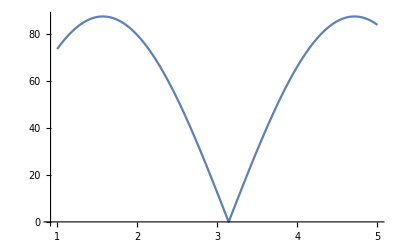

```mathematica
(* plot norms of 'g' *)
ListLinePlot[gNorm, DataRange->{t[[1]],t[[-1]]}]
```

```mathematica
(* function of finding vectors 'a' and 'b' at which the displacement vector 'g' is minimal *)
(* input: vector 'c' coordinates *)
findMinimumAB[c11_,c12_,c21_,c22_]:=FindMinimum[Norm[{c11-a1 b1,c12-a1 b2, c21-a2 b1,  c22-a2 b2},2],{a1, a2, b1, b2}];
```

```mathematica
(* calculating vectors 'a' and 'b' for which the displacement vector 'g' is minimal and writing them to an array 'ab' *)
ab={};
Do [AppendTo[ab, findMinimumAB[i[[1]], i[[2]],i[[3]],i[[4]]]], {i, c}];
```

```mathematica
(* print 'ab' matrix *)
ab // MatrixForm
```

(43.7436 | {a1→-12.8678,a2→5.73033,b1→1.69747,b2→2.63224}
43.6874 | {a1→-12.9602,a2→5.77658,b1→1.68639,b2→2.61695}
43.631 | {a1→-13.0545,a2→5.82373,b1→1.67522,b2→2.60148}
43.5746 | {a1→-13.1506,a2→5.87167,b1→1.664,b2→2.58589}
43.5181 | {a1→-13.2479,a2→5.92022,b1→1.65279,b2→2.57028}
43.4615 | {a1→-13.3478,a2→5.96993,b1→1.64143,b2→2.5544}
43.4047 | {a1→-13.4519,a2→6.02158,b1→1.62973,b2→2.53794}
43.3479 | {a1→-13.8031,a2→6.18395,b1→1.58925,b2→2.4766}
43.291 | {a1→-13.9188,a2→6.24091,b1→1.57703,b2→2.45923}
43.234 | {a1→-14.0353,a2→6.29834,b1→1.56491,b2→2.44197}
43.1769 | {a1→-14.1527,a2→6.35613,b1→1.55292,b2→2.42487}
43.1197 | {a1→-14.2707,a2→6.41432,b1→1.54104,b2→2.40791}
43.0624 | {a1→-14.3895,a2→6.47285,b1→1.52929,b2→2.39112}
43.005 | {a1→-14.5092,a2→6.53184,b1→1.51764,b2→2.37444}
42.9475 | {a1→-14.63,a2→6.59136,b1→1.50607,b2→2.35786}
42.8899 | {a1→-14.5773,a2→6.57269,b1→1.51248,b2→2.36941}
42.8322 | {a1→-14.7341,a2→6.64848,b1→1.49735,b2→2.34719}
42.7744 | {a1→-14.8916,a2→6.72465,b1→1.48247,b2→2.32532}
42.7165 | {a1→-14.8111,a2→6.69332,b1→1.49149,b2→2.34094}
42.6586 | {a1→-15.0014,a2→6.78436,b1→1.47353,b2→2.31417}
42.6005 | {a1→-15.2185,a2→6.88762,b1→1.45346,b2→2.28404}
42.5423 | {a1→-15.4567,a2→7.00057,b1→1.43199,b2→2.25167}
42.4841 | {a1→-15.7179,a2→7.124,b1→1.40912,b2→2.21704}
42.4257 | {a1→-16.0087,a2→7.26103,b1→1.38443,b2→2.17949}
42.3673 | {a1→-11.1919,a2→5.07991,b1→1.98156,b2→3.1214}
42.3087 | {a1→-11.2011,a2→5.08763,b1→1.98126,b2→3.12275}
42.2501 | {a1→-11.0484,a2→5.02178,b1→2.00997,b2→3.16984}
42.1913 | {a1→-11.0639,a2→5.03234,b1→2.00847,b2→3.16931}
42.1325 | {a1→-11.0785,a2→5.04241,b1→2.00717,b2→3.16907}
42.0736 | {a1→-11.0919,a2→5.05197,b1→2.00608,b2→3.16914}
42.0146 | {a1→-11.1042,a2→5.06097,b1→2.0052,b2→3.16953}
41.9555 | {a1→-11.1152,a2→5.06936,b1→2.00456,b2→3.17029}
41.8963 | {a1→-11.1249,a2→5.07714,b1→2.00416,b2→3.17141}
41.837 | {a1→-11.1331,a2→5.08424,b1→2.00402,b2→3.17293}
41.7776 | {a1→-11.1398,a2→5.09061,b1→2.00416,b2→3.17489}
41.7181 | {a1→-11.1449,a2→5.09622,b1→2.0046,b2→3.1773}
41.6585 | {a1→-11.1475,a2→5.10064,b1→2.0055,b2→3.18043}
41.5988 | {a1→-11.1467,a2→5.10352,b1→2.007,b2→3.1845}
41.5391 | {a1→-11.144,a2→5.10549,b1→2.00885,b2→3.18911}
41.4792 | {a1→-11.1393,a2→5.10651,b1→2.01107,b2→3.1943}
41.4192 | {a1→-11.1323,a2→5.10645,b1→2.0137,b2→3.20015}
41.3592 | {a1→-11.8254,a2→5.42773,b1→1.89696,b2→3.01618}
41.2991 | {a1→-11.8579,a2→5.44593,b1→1.89306,b2→3.01152}
41.2388 | {a1→-11.8906,a2→5.46424,b1→1.88915,b2→3.00681}
41.1785 | {a1→-11.9236,a2→5.48268,b1→1.88521,b2→3.00205}
41.1181 | {a1→-11.9569,a2→5.50123,b1→1.88125,b2→2.99725}
41.0576 | {a1→-11.9904,a2→5.5199,b1→1.87728,b2→2.9924}
40.997 | {a1→-12.0242,a2→5.53867,b1→1.8733,b2→2.98752}
40.9363 | {a1→-12.0582,a2→5.55755,b1→1.8693,b2→2.98259}
40.8755 | {a1→-12.0925,a2→5.57652,b1→1.86529,b2→2.97764}
40.8146 | {a1→-12.1269,a2→5.59558,b1→1.86128,b2→2.97266}
40.7536 | {a1→-12.1615,a2→5.6147,b1→1.85727,b2→2.96766}
40.6926 | {a1→-12.1962,a2→5.63388,b1→1.85326,b2→2.96266}
40.6314 | {a1→-12.231,a2→5.65307,b1→1.84927,b2→2.95767}
40.5702 | {a1→-12.2657,a2→5.67222,b1→1.84532,b2→2.95272}
40.5088 | {a1→-12.3,a2→5.6912,b1→1.84144,b2→2.94788}
40.4474 | {a1→-12.3336,a2→5.70983,b1→1.8377,b2→2.94324}
40.3859 | {a1→-12.3647,a2→5.72726,b1→1.83437,b2→2.93924}
40.3242 | {a1→-12.3956,a2→5.74465,b1→1.83106,b2→2.93526}
40.2625 | {a1→-12.4265,a2→5.76201,b1→1.82778,b2→2.93131}
40.2007 | {a1→-12.4574,a2→5.77933,b1→1.82452,b2→2.92739}
40.1389 | {a1→-12.4881,a2→5.79662,b1→1.82129,b2→2.92351}
40.0769 | {a1→-12.5189,a2→5.81387,b1→1.81809,b2→2.91965}
40.0148 | {a1→-12.5495,a2→5.83108,b1→1.81492,b2→2.91581}
39.9526 | {a1→-12.5801,a2→5.84824,b1→1.81177,b2→2.91202}
39.8904 | {a1→-12.6106,a2→5.86537,b1→1.80865,b2→2.90825}
39.8281 | {a1→-12.641,a2→5.88246,b1→1.80556,b2→2.90451}
39.7656 | {a1→-12.6714,a2→5.8995,b1→1.80249,b2→2.9008}
39.7031 | {a1→-12.6765,a2→5.90478,b1→1.80302,b2→2.90288}
39.6405 | {a1→-12.7075,a2→5.92213,b1→1.79988,b2→2.89902}
39.5778 | {a1→-12.7385,a2→5.93944,b1→1.79676,b2→2.89519}
39.515 | {a1→-12.7694,a2→5.9567,b1→1.79366,b2→2.89139}
39.4521 | {a1→-12.8002,a2→5.97393,b1→1.79059,b2→2.88762}
39.3891 | {a1→-12.831,a2→5.99111,b1→1.78755,b2→2.88388}
39.3261 | {a1→-12.8617,a2→6.00826,b1→1.78454,b2→2.88017}
39.2629 | {a1→-12.8923,a2→6.02536,b1→1.78155,b2→2.87649}
39.1997 | {a1→-12.9228,a2→6.04241,b1→1.77858,b2→2.87284}
39.1364 | {a1→-12.9532,a2→6.05942,b1→1.77565,b2→2.86923}
39.0729 | {a1→-12.9836,a2→6.07637,b1→1.77274,b2→2.86564}
39.0094 | {a1→-13.0138,a2→6.09327,b1→1.76986,b2→2.8621}
38.9458 | {a1→-13.044,a2→6.11012,b1→1.76701,b2→2.85858}
38.8822 | {a1→-13.074,a2→6.12691,b1→1.76418,b2→2.8551}
38.8184 | {a1→-13.1039,a2→6.14364,b1→1.76139,b2→2.85166}
38.7545 | {a1→-13.1337,a2→6.16031,b1→1.75862,b2→2.84825}
38.6906 | {a1→-13.1634,a2→6.17692,b1→1.75588,b2→2.84488}
38.6265 | {a1→-13.193,a2→6.19346,b1→1.75318,b2→2.84155}
38.5624 | {a1→-13.2224,a2→6.20994,b1→1.7505,b2→2.83826}
38.4982 | {a1→-13.2517,a2→6.22635,b1→1.74785,b2→2.835}
38.4339 | {a1→-13.2809,a2→6.24269,b1→1.74523,b2→2.83178}
38.3695 | {a1→-13.3099,a2→6.25895,b1→1.74264,b2→2.82861}
38.305 | {a1→-13.3388,a2→6.27513,b1→1.74009,b2→2.82547}
38.2405 | {a1→-13.3675,a2→6.29123,b1→1.73756,b2→2.82238}
38.1758 | {a1→-13.396,a2→6.30726,b1→1.73507,b2→2.81932}
38.1111 | {a1→-13.4244,a2→6.3232,b1→1.73261,b2→2.81631}
38.0462 | {a1→-13.4527,a2→6.33906,b1→1.73018,b2→2.81335}
37.9813 | {a1→-13.4807,a2→6.35483,b1→1.72778,b2→2.81042}
37.9163 | {a1→-13.5086,a2→6.37052,b1→1.72542,b2→2.80754}
37.8512 | {a1→-13.5364,a2→6.38612,b1→1.72308,b2→2.8047}
37.786 | {a1→-13.5639,a2→6.40163,b1→1.72078,b2→2.8019}
37.7208 | {a1→-13.5913,a2→6.41705,b1→1.71851,b2→2.79915}
37.6554 | {a1→-13.6185,a2→6.43237,b1→1.71627,b2→2.79644}
37.59 | {a1→-13.6455,a2→6.44761,b1→1.71407,b2→2.79378}
37.5245 | {a1→-13.6723,a2→6.46275,b1→1.71189,b2→2.79115}
37.4589 | {a1→-13.6989,a2→6.47778,b1→1.70975,b2→2.78858}
37.3932 | {a1→-13.7254,a2→6.49272,b1→1.70764,b2→2.78605}
37.3274 | {a1→-13.7516,a2→6.50755,b1→1.70557,b2→2.78357}
37.2615 | {a1→-13.7776,a2→6.52227,b1→1.70353,b2→2.78114}
37.1956 | {a1→-13.8034,a2→6.53689,b1→1.70153,b2→2.77876}
37.1295 | {a1→-13.8289,a2→6.55138,b1→1.69956,b2→2.77642}
37.0634 | {a1→-13.8543,a2→6.56578,b1→1.69762,b2→2.77413}
36.9972 | {a1→-13.8794,a2→6.58005,b1→1.69572,b2→2.77189}
36.9309 | {a1→-13.9043,a2→6.59422,b1→1.69385,b2→2.7697}
36.8645 | {a1→-13.929,a2→6.60827,b1→1.69202,b2→2.76756}
36.7981 | {a1→-13.9534,a2→6.6222,b1→1.69022,b2→2.76547}
36.7315 | {a1→-13.9776,a2→6.63601,b1→1.68846,b2→2.76343}
36.6649 | {a1→-14.0016,a2→6.64972,b1→1.68672,b2→2.76142}
36.5982 | {a1→-14.0254,a2→6.6633,b1→1.68503,b2→2.75948}
36.5314 | {a1→-14.0489,a2→6.67676,b1→1.68336,b2→2.75758}
36.4645 | {a1→-14.0721,a2→6.69009,b1→1.68174,b2→2.75573}
36.3975 | {a1→-14.0951,a2→6.7033,b1→1.68014,b2→2.75393}
36.3305 | {a1→-14.1179,a2→6.71639,b1→1.67858,b2→2.75218}
36.2633 | {a1→-14.1404,a2→6.72936,b1→1.67705,b2→2.75048}
36.1961 | {a1→-14.1627,a2→6.7422,b1→1.67556,b2→2.74882}
36.1288 | {a1→-14.1847,a2→6.7549,b1→1.6741,b2→2.74723}
36.0614 | {a1→-14.2065,a2→6.76749,b1→1.67268,b2→2.74567}
35.9939 | {a1→-14.228,a2→6.77995,b1→1.67128,b2→2.74417}
35.9264 | {a1→-14.2493,a2→6.79228,b1→1.66992,b2→2.74271}
35.8587 | {a1→-14.2703,a2→6.80448,b1→1.6686,b2→2.7413}
35.791 | {a1→-14.2911,a2→6.81654,b1→1.66731,b2→2.73995}
35.7232 | {a1→-14.3116,a2→6.82849,b1→1.66605,b2→2.73863}
35.6553 | {a1→-14.3318,a2→6.8403,b1→1.66482,b2→2.73737}
35.5874 | {a1→-14.3518,a2→6.85199,b1→1.66363,b2→2.73616}
35.5193 | {a1→-14.3715,a2→6.86353,b1→1.66247,b2→2.735}
35.4512 | {a1→-14.391,a2→6.87494,b1→1.66134,b2→2.73388}
35.3829 | {a1→-14.4103,a2→6.88626,b1→1.66024,b2→2.7328}
35.3146 | {a1→-14.4293,a2→6.89746,b1→1.65916,b2→2.73176}
35.2463 | {a1→-14.4482,a2→6.90855,b1→1.65812,b2→2.73075}
35.1778 | {a1→-14.4667,a2→6.91949,b1→1.6571,b2→2.72981}
35.1092 | {a1→-14.485,a2→6.93031,b1→1.65612,b2→2.7289}
35.0406 | {a1→-14.503,a2→6.94099,b1→1.65517,b2→2.72805}
34.9719 | {a1→-14.5208,a2→6.95156,b1→1.65425,b2→2.72723}
34.9031 | {a1→-14.5383,a2→6.96197,b1→1.65336,b2→2.72647}
34.8342 | {a1→-14.5556,a2→6.97226,b1→1.6525,b2→2.72575}
34.7653 | {a1→-13.0262,a2→6.24147,b1→1.84775,b2→3.04859}
34.6963 | {a1→-13.0401,a2→6.24995,b1→1.84701,b2→3.04812}
34.6271 | {a1→-13.054,a2→6.25839,b1→1.84627,b2→3.04767}
34.5579 | {a1→-13.0679,a2→6.26682,b1→1.84553,b2→3.04721}
34.4887 | {a1→-13.0817,a2→6.27521,b1→1.8448,b2→3.04676}
34.4193 | {a1→-13.0955,a2→6.28358,b1→1.84408,b2→3.04632}
34.3499 | {a1→-13.1093,a2→6.29193,b1→1.84336,b2→3.04588}
34.2804 | {a1→-13.1229,a2→6.30024,b1→1.84265,b2→3.04545}
34.2108 | {a1→-13.1366,a2→6.30853,b1→1.84195,b2→3.04502}
34.1411 | {a1→-13.1502,a2→6.31678,b1→1.84126,b2→3.0446}
34.0713 | {a1→-13.1637,a2→6.32499,b1→1.84057,b2→3.0442}
34.0015 | {a1→-13.1772,a2→6.33315,b1→1.8399,b2→3.04381}
33.9316 | {a1→-13.1906,a2→6.34128,b1→1.83924,b2→3.04343}
33.8616 | {a1→-13.2038,a2→6.34935,b1→1.83859,b2→3.04307}
33.7915 | {a1→-13.2169,a2→6.35734,b1→1.83796,b2→3.04275}
33.7213 | {a1→-13.23,a2→6.36526,b1→1.83735,b2→3.04244}
33.6511 | {a1→-13.2428,a2→6.37309,b1→1.83677,b2→3.04217}
33.5808 | {a1→-13.2554,a2→6.38082,b1→1.83621,b2→3.04195}
33.5104 | {a1→-13.2678,a2→6.38845,b1→1.83568,b2→3.04176}
33.4399 | {a1→-13.28,a2→6.39595,b1→1.83519,b2→3.04163}
33.3694 | {a1→-13.2919,a2→6.40331,b1→1.83473,b2→3.04155}
33.2988 | {a1→-13.3035,a2→6.41051,b1→1.83431,b2→3.04154}
33.228 | {a1→-13.3148,a2→6.41755,b1→1.83394,b2→3.0416}
33.1573 | {a1→-13.3256,a2→6.42439,b1→1.83362,b2→3.04174}
33.0864 | {a1→-13.3361,a2→6.43105,b1→1.83336,b2→3.04197}
33.0155 | {a1→-13.3461,a2→6.43747,b1→1.83315,b2→3.0423}
32.9445 | {a1→-13.3557,a2→6.44365,b1→1.83302,b2→3.04273}
32.8734 | {a1→-13.3647,a2→6.44956,b1→1.83295,b2→3.04328}
32.8022 | {a1→-13.3731,a2→6.4552,b1→1.83296,b2→3.04394}
32.7309 | {a1→-13.381,a2→6.46053,b1→1.83305,b2→3.04474}
32.6596 | {a1→-13.3882,a2→6.46556,b1→1.83323,b2→3.04568}
32.5882 | {a1→-13.3947,a2→6.47023,b1→1.8335,b2→3.04678}
32.5167 | {a1→-13.4005,a2→6.47456,b1→1.83387,b2→3.04802}
32.4452 | {a1→-13.4055,a2→6.4785,b1→1.83434,b2→3.04944}
32.3736 | {a1→-13.4133,a2→6.48381,b1→1.83442,b2→3.05021}
32.3018 | {a1→-13.4233,a2→6.49012,b1→1.83422,b2→3.0505}
32.2301 | {a1→-13.4324,a2→6.49603,b1→1.83412,b2→3.05096}
32.1582 | {a1→-13.4407,a2→6.50153,b1→1.83414,b2→3.05161}
32.0863 | {a1→-13.4482,a2→6.50662,b1→1.83427,b2→3.05244}
32.0143 | {a1→-13.4547,a2→6.51123,b1→1.83453,b2→3.05349}
31.9422 | {a1→-13.4602,a2→6.51539,b1→1.83491,b2→3.05474}
31.87 | {a1→-13.4648,a2→6.51905,b1→1.83543,b2→3.05621}
31.7978 | {a1→-13.4683,a2→6.5222,b1→1.83609,b2→3.05791}
31.7255 | {a1→-13.4707,a2→6.52483,b1→1.8369,b2→3.05985}
31.6531 | {a1→-13.4721,a2→6.5269,b1→1.83785,b2→3.06204}
31.5806 | {a1→-13.4722,a2→6.5284,b1→1.83896,b2→3.06448}
31.5081 | {a1→-13.4712,a2→6.5293,b1→1.84024,b2→3.06721}
31.4355 | {a1→-13.469,a2→6.52964,b1→1.84167,b2→3.07018}
31.3628 | {a1→-14.6404,a2→7.09908,b1→1.69535,b2→2.82679}
31.29 | {a1→-14.6636,a2→7.11185,b1→1.6937,b2→2.82458}
31.2172 | {a1→-14.6869,a2→7.12461,b1→1.69206,b2→2.82237}
31.1443 | {a1→-14.7102,a2→7.13742,b1→1.69041,b2→2.82014}
31.0713 | {a1→-14.7335,a2→7.15024,b1→1.68875,b2→2.81791}
30.9982 | {a1→-14.7569,a2→7.16311,b1→1.6871,b2→2.81566}
30.9251 | {a1→-14.7804,a2→7.17599,b1→1.68543,b2→2.81341}
30.8519 | {a1→-14.804,a2→7.1889,b1→1.68377,b2→2.81115}
30.7786 | {a1→-14.8276,a2→7.20185,b1→1.6821,b2→2.80887}
30.7053 | {a1→-14.8513,a2→7.21483,b1→1.68043,b2→2.80658}
30.6319 | {a1→-14.8751,a2→7.22784,b1→1.67875,b2→2.80428}
30.5584 | {a1→-14.899,a2→7.24088,b1→1.67706,b2→2.80197}
30.4848 | {a1→-14.9229,a2→7.25396,b1→1.67537,b2→2.79965}
30.4112 | {a1→-14.9469,a2→7.26708,b1→1.67368,b2→2.79731}
30.3374 | {a1→-14.971,a2→7.28023,b1→1.67198,b2→2.79496}
30.2637 | {a1→-14.9952,a2→7.29342,b1→1.67027,b2→2.7926}
30.1898 | {a1→-15.0195,a2→7.30666,b1→1.66856,b2→2.79022}
30.1159 | {a1→-15.0439,a2→7.31993,b1→1.66684,b2→2.78782}
30.0419 | {a1→-15.0683,a2→7.33325,b1→1.66512,b2→2.78542}
29.9678 | {a1→-15.0929,a2→7.34661,b1→1.66339,b2→2.783}
29.8937 | {a1→-15.1176,a2→7.36002,b1→1.66164,b2→2.78056}
29.8195 | {a1→-15.1423,a2→7.37346,b1→1.6599,b2→2.77811}
29.7452 | {a1→-15.1672,a2→7.38696,b1→1.65815,b2→2.77564}
29.6708 | {a1→-15.1922,a2→7.40052,b1→1.65638,b2→2.77315}
29.5964 | {a1→-15.2173,a2→7.41412,b1→1.65462,b2→2.77065}
29.5219 | {a1→-15.2425,a2→7.42776,b1→1.65284,b2→2.76814}
29.4473 | {a1→-15.2678,a2→7.44145,b1→1.65106,b2→2.7656}
29.3727 | {a1→-15.2932,a2→7.45521,b1→1.64926,b2→2.76305}
29.298 | {a1→-15.3187,a2→7.46901,b1→1.64746,b2→2.76049}
29.2232 | {a1→-15.3444,a2→7.48287,b1→1.64565,b2→2.7579}
29.1484 | {a1→-15.3702,a2→7.49678,b1→1.64384,b2→2.7553}
29.0735 | {a1→-15.396,a2→7.51074,b1→1.64201,b2→2.75268}
28.9985 | {a1→-15.4221,a2→7.52477,b1→1.64018,b2→2.75004}
28.9234 | {a1→-15.4482,a2→7.53884,b1→1.63834,b2→2.74739}
28.8483 | {a1→-15.4744,a2→7.55297,b1→1.63649,b2→2.74471}
28.7731 | {a1→-15.5008,a2→7.56717,b1→1.63463,b2→2.74202}
28.6978 | {a1→-15.5273,a2→7.58141,b1→1.63276,b2→2.73932}
28.6225 | {a1→-15.5539,a2→7.59572,b1→1.63088,b2→2.73659}
28.5471 | {a1→-15.5807,a2→7.61009,b1→1.629,b2→2.73385}
28.4716 | {a1→-15.6076,a2→7.62452,b1→1.62711,b2→2.73109}
28.3961 | {a1→-15.6346,a2→7.63901,b1→1.6252,b2→2.7283}
28.3205 | {a1→-15.6618,a2→7.65358,b1→1.62329,b2→2.7255}
28.2448 | {a1→-15.6891,a2→7.6682,b1→1.62136,b2→2.72268}
28.1691 | {a1→-15.7165,a2→7.6829,b1→1.61943,b2→2.71984}
28.0933 | {a1→-15.7443,a2→7.69775,b1→1.61747,b2→2.71695}
28.0174 | {a1→-15.9259,a2→7.78784,b1→1.5999,b2→2.68784}
27.9415 | {a1→-15.9652,a2→7.8083,b1→1.59685,b2→2.6831}
27.8655 | {a1→-16.0052,a2→7.82917,b1→1.59373,b2→2.67825}
27.7894 | {a1→-16.0462,a2→7.85047,b1→1.59053,b2→2.67326}
27.7132 | {a1→-16.0881,a2→7.87222,b1→1.58726,b2→2.66815}
27.637 | {a1→-16.1309,a2→7.89445,b1→1.5839,b2→2.66289}
27.5608 | {a1→-16.1748,a2→7.91719,b1→1.58046,b2→2.65749}
27.4844 | {a1→-16.2197,a2→7.94044,b1→1.57694,b2→2.65194}
27.408 | {a1→-16.2658,a2→7.96426,b1→1.57332,b2→2.64623}
27.3315 | {a1→-16.3131,a2→7.98866,b1→1.5696,b2→2.64035}
27.255 | {a1→-14.2726,a2→6.99047,b1→1.79498,b2→3.01989}
27.1784 | {a1→-14.2667,a2→6.98867,b1→1.79668,b2→3.02317}
27.1017 | {a1→-14.2606,a2→6.98673,b1→1.79841,b2→3.0265}
27.025 | {a1→-14.2539,a2→6.98453,b1→1.80021,b2→3.02995}
26.9482 | {a1→-14.2472,a2→6.98233,b1→1.80201,b2→3.03339}
26.8713 | {a1→-14.2349,a2→6.97735,b1→1.80453,b2→3.03804}
26.7944 | {a1→-14.2278,a2→6.97492,b1→1.80638,b2→3.04157}
26.7174 | {a1→-14.2205,a2→6.97234,b1→1.80827,b2→3.04516}
26.6404 | {a1→-14.2129,a2→6.96966,b1→1.81018,b2→3.04879}
26.5632 | {a1→-14.205,a2→6.96684,b1→1.81213,b2→3.05248}
26.4861 | {a1→-14.197,a2→6.96391,b1→1.81411,b2→3.05621}
26.4088 | {a1→-14.1887,a2→6.96089,b1→1.81611,b2→3.05998}
26.3315 | {a1→-14.1803,a2→6.95774,b1→1.81814,b2→3.0638}
26.2541 | {a1→-14.1716,a2→6.9545,b1→1.82019,b2→3.06765}
26.1767 | {a1→-14.1627,a2→6.95113,b1→1.82227,b2→3.07156}
26.0992 | {a1→-14.1537,a2→6.94766,b1→1.82438,b2→3.07551}
26.0216 | {a1→-14.1444,a2→6.9441,b1→1.82651,b2→3.0795}
25.944 | {a1→-14.1349,a2→6.94044,b1→1.82867,b2→3.08353}
25.8663 | {a1→-14.2143,a2→6.98038,b1→1.81939,b2→3.06827}
25.7885 | {a1→-14.2163,a2→6.98236,b1→1.82006,b2→3.06977}
25.7107 | {a1→-14.2183,a2→6.98427,b1→1.82073,b2→3.0713}
25.6328 | {a1→-14.2201,a2→6.98613,b1→1.82142,b2→3.07284}
25.5549 | {a1→-14.2218,a2→6.98794,b1→1.82212,b2→3.07439}
25.4769 | {a1→-14.2235,a2→6.98968,b1→1.82283,b2→3.07597}
25.3988 | {a1→-14.225,a2→6.99138,b1→1.82354,b2→3.07755}
25.3207 | {a1→-14.2264,a2→6.99301,b1→1.82428,b2→3.07916}
25.2425 | {a1→-14.2277,a2→6.9946,b1→1.82502,b2→3.08078}
25.1643 | {a1→-14.2289,a2→6.99612,b1→1.82577,b2→3.08242}
25.086 | {a1→-14.23,a2→6.99759,b1→1.82653,b2→3.08408}
25.0076 | {a1→-14.231,a2→6.999,b1→1.8273,b2→3.08575}
24.9292 | {a1→-14.2319,a2→7.00037,b1→1.82809,b2→3.08744}
24.8507 | {a1→-14.2327,a2→7.00167,b1→1.82888,b2→3.08914}
24.7721 | {a1→-14.2335,a2→7.00293,b1→1.82968,b2→3.09086}
24.6935 | {a1→-14.2341,a2→7.00413,b1→1.83049,b2→3.09259}
24.6149 | {a1→-14.2346,a2→7.00529,b1→1.83132,b2→3.09433}
24.5361 | {a1→-14.2351,a2→7.0064,b1→1.83214,b2→3.09609}
24.4573 | {a1→-14.2354,a2→7.00745,b1→1.83299,b2→3.09786}
24.3785 | {a1→-14.2357,a2→7.00848,b1→1.83383,b2→3.09964}
24.2996 | {a1→-14.2358,a2→7.00942,b1→1.83469,b2→3.10145}
24.2206 | {a1→-14.2359,a2→7.01032,b1→1.83556,b2→3.10327}
24.1416 | {a1→-14.2359,a2→7.01118,b1→1.83644,b2→3.1051}
24.0625 | {a1→-14.2358,a2→7.01198,b1→1.83733,b2→3.10695}
23.9834 | {a1→-14.2356,a2→7.01273,b1→1.83823,b2→3.10881}
23.9042 | {a1→-14.2353,a2→7.01344,b1→1.83913,b2→3.11068}
23.8249 | {a1→-14.2349,a2→7.01409,b1→1.84005,b2→3.11257}
23.7456 | {a1→-14.2344,a2→7.0147,b1→1.84097,b2→3.11447}
23.6662 | {a1→-14.2338,a2→7.01525,b1→1.84191,b2→3.11639}
23.5868 | {a1→-14.2332,a2→7.01576,b1→1.84285,b2→3.11832}
23.5073 | {a1→-14.2324,a2→7.01623,b1→1.8438,b2→3.12025}
23.4277 | {a1→-14.2316,a2→7.01664,b1→1.84476,b2→3.12221}
23.3481 | {a1→-14.2307,a2→7.017,b1→1.84573,b2→3.12419}
23.2685 | {a1→-14.2297,a2→7.01732,b1→1.84671,b2→3.12617}
23.1888 | {a1→-14.2286,a2→7.01758,b1→1.8477,b2→3.12817}
23.109 | {a1→-14.2274,a2→7.01781,b1→1.84869,b2→3.13018}
23.0292 | {a1→-14.2261,a2→7.01798,b1→1.8497,b2→3.13221}
22.9493 | {a1→-14.2248,a2→7.01811,b1→1.85071,b2→3.13425}
22.8693 | {a1→-14.2233,a2→7.01819,b1→1.85174,b2→3.1363}
22.7893 | {a1→-14.2218,a2→7.01823,b1→1.85277,b2→3.13836}
22.7093 | {a1→-14.2202,a2→7.0182,b1→1.85381,b2→3.14044}
22.6292 | {a1→-14.2185,a2→7.01814,b1→1.85486,b2→3.14254}
22.549 | {a1→-14.2167,a2→7.01804,b1→1.85591,b2→3.14464}
22.4688 | {a1→-14.2149,a2→7.01789,b1→1.85698,b2→3.14676}
22.3885 | {a1→-14.2129,a2→7.01769,b1→1.85806,b2→3.14889}
22.3082 | {a1→-14.2109,a2→7.01743,b1→1.85914,b2→3.15104}
22.2278 | {a1→-14.2088,a2→7.01715,b1→1.86023,b2→3.1532}
22.1474 | {a1→-14.2065,a2→7.0168,b1→1.86134,b2→3.15538}
22.0669 | {a1→-14.2043,a2→7.01643,b1→1.86245,b2→3.15756}
21.9863 | {a1→-14.2019,a2→7.01598,b1→1.86357,b2→3.15977}
21.9057 | {a1→-14.1994,a2→7.0155,b1→1.8647,b2→3.16198}
21.8251 | {a1→-14.1969,a2→7.01498,b1→1.86584,b2→3.16421}
21.7444 | {a1→-14.1949,a2→7.01471,b1→1.8669,b2→3.16632}
21.6636 | {a1→-14.1935,a2→7.01476,b1→1.86788,b2→3.16827}
21.5828 | {a1→-14.192,a2→7.01475,b1→1.86887,b2→3.17024}
21.502 | {a1→-14.1905,a2→7.01472,b1→1.86986,b2→3.17222}
21.421 | {a1→-14.1889,a2→7.01465,b1→1.87086,b2→3.17421}
21.3401 | {a1→-14.1873,a2→7.01453,b1→1.87187,b2→3.17621}
21.2591 | {a1→-14.1855,a2→7.01437,b1→1.87288,b2→3.17822}
21.178 | {a1→-14.1837,a2→7.01418,b1→1.8739,b2→3.18024}
21.0969 | {a1→-14.1818,a2→7.01393,b1→1.87494,b2→3.18228}
21.0157 | {a1→-14.1799,a2→7.01366,b1→1.87597,b2→3.18432}
20.9345 | {a1→-14.1778,a2→7.01334,b1→1.87701,b2→3.18637}
20.8532 | {a1→-14.1757,a2→7.01298,b1→1.87807,b2→3.18844}
20.7718 | {a1→-14.1736,a2→7.01258,b1→1.87912,b2→3.19052}
20.6905 | {a1→-14.1713,a2→7.01214,b1→1.88019,b2→3.1926}
20.609 | {a1→-14.169,a2→7.01165,b1→1.88127,b2→3.19471}
20.5275 | {a1→-14.1666,a2→7.01113,b1→1.88235,b2→3.19682}
20.446 | {a1→-14.1641,a2→7.01057,b1→1.88343,b2→3.19894}
20.3644 | {a1→-14.1616,a2→7.00997,b1→1.88453,b2→3.20107}
20.2828 | {a1→-14.1589,a2→7.00933,b1→1.88563,b2→3.20322}
20.2011 | {a1→-14.1563,a2→7.00865,b1→1.88674,b2→3.20537}
20.1194 | {a1→-14.1535,a2→7.00792,b1→1.88786,b2→3.20754}
20.0376 | {a1→-14.1507,a2→7.00717,b1→1.88898,b2→3.20971}
19.9558 | {a1→-14.1478,a2→7.00637,b1→1.89011,b2→3.2119}
19.8739 | {a1→-14.1448,a2→7.00554,b1→1.89125,b2→3.2141}
19.792 | {a1→-14.1418,a2→7.00467,b1→1.89239,b2→3.2163}
19.71 | {a1→-14.1387,a2→7.00376,b1→1.89354,b2→3.21852}
19.628 | {a1→-14.1355,a2→7.00282,b1→1.8947,b2→3.22074}
19.5459 | {a1→-14.1323,a2→7.00184,b1→1.89586,b2→3.22298}
19.4638 | {a1→-14.129,a2→7.00083,b1→1.89703,b2→3.22522}
19.3816 | {a1→-14.1257,a2→6.99979,b1→1.8982,b2→3.22747}
19.2994 | {a1→-14.1223,a2→6.99871,b1→1.89938,b2→3.22973}
19.2171 | {a1→-14.1189,a2→6.99762,b1→1.90056,b2→3.23199}
19.1348 | {a1→-14.1154,a2→6.99648,b1→1.90175,b2→3.23427}
19.0525 | {a1→-14.1118,a2→6.99532,b1→1.90294,b2→3.23654}
18.9701 | {a1→-14.1082,a2→6.99412,b1→1.90414,b2→3.23883}
18.8876 | {a1→-14.1046,a2→6.9929,b1→1.90534,b2→3.24112}
18.8051 | {a1→-14.1009,a2→6.99167,b1→1.90654,b2→3.24342}
18.7226 | {a1→-14.0972,a2→6.9904,b1→1.90775,b2→3.24572}
18.64 | {a1→-14.0934,a2→6.98912,b1→1.90896,b2→3.24801}
18.5573 | {a1→-14.0896,a2→6.98781,b1→1.91017,b2→3.25032}
18.4746 | {a1→-14.0858,a2→6.98648,b1→1.91138,b2→3.25263}
18.3919 | {a1→-14.082,a2→6.98514,b1→1.9126,b2→3.25494}
18.3091 | {a1→-14.0781,a2→6.98379,b1→1.91381,b2→3.25724}
18.2263 | {a1→-14.0742,a2→6.98241,b1→1.91503,b2→3.25955}
18.1435 | {a1→-14.0703,a2→6.98102,b1→1.91625,b2→3.26186}
18.0606 | {a1→-14.0664,a2→6.97963,b1→1.91747,b2→3.26417}
17.9776 | {a1→-14.0624,a2→6.97822,b1→1.91868,b2→3.26647}
17.8946 | {a1→-14.0585,a2→6.97681,b1→1.9199,b2→3.26877}
17.8116 | {a1→-14.0545,a2→6.97539,b1→1.92111,b2→3.27107}
17.7285 | {a1→-14.0506,a2→6.97397,b1→1.92232,b2→3.27336}
17.6454 | {a1→-14.0466,a2→6.97255,b1→1.92353,b2→3.27565}
17.5622 | {a1→-14.0427,a2→6.97112,b1→1.92473,b2→3.27792}
17.479 | {a1→-14.0388,a2→6.9697,b1→1.92593,b2→3.2802}
17.3957 | {a1→-14.0348,a2→6.96827,b1→1.92713,b2→3.28246}
17.3124 | {a1→-14.031,a2→6.96686,b1→1.92832,b2→3.28472}
17.2291 | {a1→-14.0271,a2→6.96545,b1→1.92951,b2→3.28696}
17.1457 | {a1→-14.0232,a2→6.96405,b1→1.93069,b2→3.28919}
17.0623 | {a1→-14.0194,a2→6.96267,b1→1.93186,b2→3.29141}
16.9788 | {a1→-14.0156,a2→6.9613,b1→1.93303,b2→3.29362}
16.8953 | {a1→-14.0119,a2→6.95994,b1→1.93419,b2→3.29581}
16.8117 | {a1→-14.0082,a2→6.9586,b1→1.93534,b2→3.29799}
16.7281 | {a1→-14.0045,a2→6.95729,b1→1.93648,b2→3.30015}
16.6445 | {a1→-14.0009,a2→6.95599,b1→1.93762,b2→3.30229}
16.5608 | {a1→-13.9974,a2→6.95473,b1→1.93874,b2→3.30441}
16.4771 | {a1→-13.9939,a2→6.95349,b1→1.93985,b2→3.30652}
16.3933 | {a1→-13.9905,a2→6.95228,b1→1.94095,b2→3.3086}
16.3095 | {a1→-13.9872,a2→6.95111,b1→1.94203,b2→3.31065}
16.2257 | {a1→-13.984,a2→6.94997,b1→1.9431,b2→3.31269}
16.1418 | {a1→-13.9808,a2→6.94888,b1→1.94416,b2→3.31469}
16.0579 | {a1→-13.9778,a2→6.94783,b1→1.94519,b2→3.31667}
15.9739 | {a1→-13.9748,a2→6.94683,b1→1.94622,b2→3.31862}
15.8899 | {a1→-13.972,a2→6.94588,b1→1.94722,b2→3.32053}
15.8059 | {a1→-13.9692,a2→6.94497,b1→1.94821,b2→3.32242}
15.7218 | {a1→-13.9666,a2→6.94413,b1→1.94918,b2→3.32427}
15.6377 | {a1→-13.9641,a2→6.94335,b1→1.95012,b2→3.32608}
15.5535 | {a1→-13.9618,a2→6.94263,b1→1.95105,b2→3.32786}
15.4693 | {a1→-13.9596,a2→6.94198,b1→1.95195,b2→3.32959}
15.3851 | {a1→-13.9575,a2→6.9414,b1→1.95283,b2→3.33128}
15.3008 | {a1→-13.9556,a2→6.94089,b1→1.95368,b2→3.33294}
15.2165 | {a1→-13.9539,a2→6.94046,b1→1.95451,b2→3.33454}
15.1322 | {a1→-13.9523,a2→6.94013,b1→1.95531,b2→3.3361}
15.0478 | {a1→-13.9509,a2→6.93986,b1→1.95609,b2→3.33761}
14.9634 | {a1→-13.9497,a2→6.9397,b1→1.95683,b2→3.33906}
14.8789 | {a1→-13.9487,a2→6.93963,b1→1.95754,b2→3.34047}
14.7944 | {a1→-13.9497,a2→6.94052,b1→1.95798,b2→3.3414}
14.7099 | {a1→-13.9491,a2→6.94066,b1→1.95863,b2→3.34269}
14.6253 | {a1→-13.9488,a2→6.94092,b1→1.95923,b2→3.34391}
14.5407 | {a1→-13.9487,a2→6.94129,b1→1.95981,b2→3.34507}
14.4561 | {a1→-13.9488,a2→6.94178,b1→1.96034,b2→3.34616}
14.3714 | {a1→-13.9493,a2→6.9424,b1→1.96084,b2→3.34719}
14.2867 | {a1→-13.8949,a2→6.91576,b1→1.96905,b2→3.3614}
14.202 | {a1→-13.8968,a2→6.91711,b1→1.96934,b2→3.36205}
14.1172 | {a1→-13.8991,a2→6.91862,b1→1.96956,b2→3.36262}
14.0324 | {a1→-13.9017,a2→6.92032,b1→1.96974,b2→3.36309}
13.9475 | {a1→-13.9047,a2→6.9222,b1→1.96985,b2→3.36346}
13.8626 | {a1→-13.9081,a2→6.92428,b1→1.96991,b2→3.36373}
13.7777 | {a1→-13.9119,a2→6.92656,b1→1.9699,b2→3.3639}
13.6927 | {a1→-13.9161,a2→6.92905,b1→1.96983,b2→3.36395}
13.6077 | {a1→-13.9208,a2→6.93178,b1→1.96969,b2→3.36388}
13.5227 | {a1→-13.926,a2→6.93476,b1→1.96948,b2→3.36368}
13.4377 | {a1→-13.9318,a2→6.93799,b1→1.96919,b2→3.36335}
13.3526 | {a1→-13.938,a2→6.94148,b1→1.96882,b2→3.36289}
13.2675 | {a1→-13.9449,a2→6.94525,b1→1.96837,b2→3.36228}
13.1823 | {a1→-13.9523,a2→6.94931,b1→1.96783,b2→3.36153}
13.0971 | {a1→-13.9603,a2→6.95367,b1→1.96721,b2→3.36062}
13.0119 | {a1→-13.9689,a2→6.95833,b1→1.9665,b2→3.35957}
12.9266 | {a1→-13.9781,a2→6.96328,b1→1.9657,b2→3.35836}
12.8413 | {a1→-13.9879,a2→6.96852,b1→1.96482,b2→3.35701}
12.756 | {a1→-13.9251,a2→6.93758,b1→1.97417,b2→3.37316}
12.6707 | {a1→-13.9276,a2→6.93915,b1→1.97432,b2→3.37357}
12.5853 | {a1→-13.93,a2→6.94072,b1→1.97446,b2→3.37396}
12.4999 | {a1→-13.9324,a2→6.94228,b1→1.9746,b2→3.37435}
12.4144 | {a1→-13.9349,a2→6.94383,b1→1.97474,b2→3.37474}
12.329 | {a1→-13.9372,a2→6.94533,b1→1.97488,b2→3.37514}
12.2435 | {a1→-13.9395,a2→6.94681,b1→1.97504,b2→3.37555}
12.1579 | {a1→-13.9417,a2→6.94823,b1→1.9752,b2→3.37598}
12.0724 | {a1→-13.9437,a2→6.94957,b1→1.97538,b2→3.37644}
11.9868 | {a1→-13.9474,a2→6.95174,b1→1.97532,b2→3.37649}
11.9011 | {a1→-13.9484,a2→6.95256,b1→1.97564,b2→3.37718}
11.8155 | {a1→-13.9492,a2→6.95329,b1→1.97599,b2→3.37791}
11.7298 | {a1→-13.9498,a2→6.95392,b1→1.97635,b2→3.37869}
11.6441 | {a1→-13.9502,a2→6.95444,b1→1.97675,b2→3.3795}
11.5583 | {a1→-13.9505,a2→6.9549,b1→1.97716,b2→3.38034}
11.4726 | {a1→-13.9518,a2→6.95586,b1→1.97742,b2→3.38093}
11.3868 | {a1→-13.9578,a2→6.95917,b1→1.97701,b2→3.38036}
11.3009 | {a1→-13.9729,a2→6.96702,b1→1.9753,b2→3.37759}
11.2151 | {a1→-13.9776,a2→6.96965,b1→1.97508,b2→3.37734}
11.1292 | {a1→-13.9657,a2→6.96403,b1→1.97719,b2→3.38109}
11.0433 | {a1→-13.9646,a2→6.96379,b1→1.97778,b2→3.38222}
10.9573 | {a1→-13.9626,a2→6.96306,b1→1.97849,b2→3.38358}
10.8714 | {a1→-13.9748,a2→6.96946,b1→1.97718,b2→3.38147}
10.7854 | {a1→-13.9773,a2→6.97098,b1→1.97725,b2→3.38172}
10.6994 | {a1→-13.9784,a2→6.97183,b1→1.97751,b2→3.38229}
10.6133 | {a1→-13.9796,a2→6.97273,b1→1.97775,b2→3.38283}
10.5272 | {a1→-13.9811,a2→6.97376,b1→1.97795,b2→3.38329}
10.4411 | {a1→-13.9828,a2→6.97489,b1→1.97811,b2→3.3837}
10.355 | {a1→-13.9845,a2→6.97604,b1→1.97827,b2→3.38409}
10.2689 | {a1→-13.9862,a2→6.97716,b1→1.97843,b2→3.38449}
10.1827 | {a1→-13.9876,a2→6.97813,b1→1.97862,b2→3.38495}
10.0965 | {a1→-13.9886,a2→6.97889,b1→1.97888,b2→3.38551}
10.0103 | {a1→-13.9889,a2→6.97932,b1→1.97922,b2→3.38621}
9.924 | {a1→-13.9885,a2→6.97941,b1→1.97966,b2→3.38708}
9.83772 | {a1→-13.9876,a2→6.97919,b1→1.98018,b2→3.38809}
9.75142 | {a1→-13.9865,a2→6.97894,b1→1.9807,b2→3.3891}
9.66509 | {a1→-13.9865,a2→6.97919,b1→1.98108,b2→3.38987}
9.57874 | {a1→-13.9888,a2→6.9806,b1→1.98113,b2→3.39006}
9.49237 | {a1→-13.9943,a2→6.9836,b1→1.98072,b2→3.38947}
9.40597 | {a1→-14.002,a2→6.98768,b1→1.98,b2→3.38835}
9.31955 | {a1→-14.0659,a2→7.0198,b1→1.97137,b2→3.3737}
9.2331 | {a1→-14.0724,a2→7.02331,b1→1.97081,b2→3.37285}
9.14663 | {a1→-14.0769,a2→7.02583,b1→1.97053,b2→3.37247}
9.06014 | {a1→-14.0812,a2→7.02821,b1→1.97028,b2→3.37216}
8.97363 | {a1→-14.0848,a2→7.03024,b1→1.97012,b2→3.372}
8.88709 | {a1→-14.0862,a2→7.0312,b1→1.97026,b2→3.37235}
8.80053 | {a1→-14.0879,a2→7.03224,b1→1.97038,b2→3.37265}
8.71395 | {a1→-14.0922,a2→7.03463,b1→1.97011,b2→3.37229}
8.62735 | {a1→-14.0998,a2→7.03867,b1→1.96938,b2→3.37114}
8.54073 | {a1→-14.1097,a2→7.04386,b1→1.96832,b2→3.36943}
8.45408 | {a1→-14.1206,a2→7.04951,b1→1.96713,b2→3.3675}
8.36741 | {a1→-14.1312,a2→7.05505,b1→1.96598,b2→3.36561}
8.28073 | {a1→-14.141,a2→7.06014,b1→1.96494,b2→3.36393}
8.19402 | {a1→-14.1497,a2→7.06469,b1→1.96405,b2→3.36251}
8.10729 | {a1→-14.1372,a2→7.0587,b1→1.96609,b2→3.3661}
8.02054 | {a1→-14.1424,a2→7.06148,b1→1.96569,b2→3.3655}
7.93377 | {a1→-14.1466,a2→7.0638,b1→1.96541,b2→3.36511}
7.84699 | {a1→-14.1503,a2→7.06586,b1→1.96519,b2→3.36484}
7.76018 | {a1→-14.1537,a2→7.06777,b1→1.96502,b2→3.36464}
7.67335 | {a1→-14.157,a2→7.06963,b1→1.96486,b2→3.36445}
7.5865 | {a1→-14.1603,a2→7.07148,b1→1.96469,b2→3.36425}
7.49964 | {a1→-14.1636,a2→7.07335,b1→1.96452,b2→3.36404}
7.41275 | {a1→-14.1671,a2→7.07529,b1→1.96432,b2→3.36379}
7.32585 | {a1→-14.1707,a2→7.07729,b1→1.9641,b2→3.3635}
7.23893 | {a1→-14.1745,a2→7.07938,b1→1.96385,b2→3.36316}
7.15199 | {a1→-14.1785,a2→7.08155,b1→1.96358,b2→3.36278}
7.06504 | {a1→-14.1826,a2→7.08379,b1→1.96328,b2→3.36235}
6.97806 | {a1→-14.1869,a2→7.08613,b1→1.96296,b2→3.36187}
6.89107 | {a1→-14.1914,a2→7.08854,b1→1.9626,b2→3.36135}
6.80406 | {a1→-14.196,a2→7.09103,b1→1.96223,b2→3.36078}
6.71703 | {a1→-14.2008,a2→7.0936,b1→1.96183,b2→3.36018}
6.62999 | {a1→-14.2057,a2→7.09623,b1→1.9614,b2→3.35953}
6.54293 | {a1→-14.2108,a2→7.09894,b1→1.96095,b2→3.35883}
6.45585 | {a1→-14.216,a2→7.10171,b1→1.96049,b2→3.35811}
6.36876 | {a1→-14.2213,a2→7.10455,b1→1.95999,b2→3.35734}
6.28165 | {a1→-14.2268,a2→7.10744,b1→1.95948,b2→3.35654}
6.19453 | {a1→-14.2324,a2→7.11041,b1→1.95895,b2→3.3557}
6.10739 | {a1→-14.2381,a2→7.11342,b1→1.9584,b2→3.35483}
6.02024 | {a1→-14.2439,a2→7.11648,b1→1.95783,b2→3.35392}
5.93307 | {a1→-14.2498,a2→7.11962,b1→1.95724,b2→3.35298}
5.84588 | {a1→-14.2559,a2→7.12278,b1→1.95664,b2→3.35202}
5.75868 | {a1→-14.262,a2→7.126,b1→1.95602,b2→3.35102}
5.67147 | {a1→-14.2682,a2→7.12926,b1→1.95539,b2→3.35}
5.58424 | {a1→-14.2745,a2→7.13256,b1→1.95474,b2→3.34895}
5.497 | {a1→-14.2809,a2→7.13589,b1→1.95408,b2→3.34788}
5.40974 | {a1→-14.2873,a2→7.13925,b1→1.9534,b2→3.34679}
5.32247 | {a1→-14.2938,a2→7.14262,b1→1.95273,b2→3.34569}
5.23519 | {a1→-14.3003,a2→7.14601,b1→1.95204,b2→3.34458}
5.1479 | {a1→-14.3068,a2→7.1494,b1→1.95135,b2→3.34345}
5.06059 | {a1→-14.3133,a2→7.1528,b1→1.95065,b2→3.34232}
4.97327 | {a1→-14.3198,a2→7.15617,b1→1.94996,b2→3.34119}
4.88593 | {a1→-14.3263,a2→7.15953,b1→1.94927,b2→3.34006}
4.79859 | {a1→-14.3327,a2→7.16286,b1→1.94858,b2→3.33894}
4.71123 | {a1→-14.339,a2→7.16615,b1→1.9479,b2→3.33782}
4.62386 | {a1→-14.3452,a2→7.16939,b1→1.94723,b2→3.33673}
4.53648 | {a1→-14.3513,a2→7.17256,b1→1.94658,b2→3.33566}
4.44909 | {a1→-14.3573,a2→7.17567,b1→1.94594,b2→3.33461}
4.36168 | {a1→-14.297,a2→7.14566,b1→1.95431,b2→3.34901}
4.27427 | {a1→-14.3048,a2→7.14966,b1→1.95341,b2→3.34752}
4.18684 | {a1→-14.3128,a2→7.15377,b1→1.95248,b2→3.34597}
4.09941 | {a1→-14.3211,a2→7.15801,b1→1.95151,b2→3.34436}
4.01196 | {a1→-14.3296,a2→7.16238,b1→1.9505,b2→3.34268}
3.92451 | {a1→-14.3384,a2→7.16687,b1→1.94946,b2→3.34094}
3.83704 | {a1→-14.3474,a2→7.17149,b1→1.94838,b2→3.33913}
3.74957 | {a1→-14.3567,a2→7.17622,b1→1.94727,b2→3.33727}
3.66208 | {a1→-14.3662,a2→7.18107,b1→1.94612,b2→3.33534}
3.57459 | {a1→-14.3759,a2→7.18603,b1→1.94494,b2→3.33336}
3.48708 | {a1→-14.3859,a2→7.1911,b1→1.94372,b2→3.33132}
3.39957 | {a1→-14.396,a2→7.19627,b1→1.94248,b2→3.32923}
3.31205 | {a1→-14.4064,a2→7.20153,b1→1.94122,b2→3.3271}
3.22452 | {a1→-14.4177,a2→7.20729,b1→1.93981,b2→3.32472}
3.13699 | {a1→-14.4308,a2→7.2139,b1→1.93818,b2→3.32196}
3.04944 | {a1→-14.4442,a2→7.22068,b1→1.9365,b2→3.31911}
2.96189 | {a1→-14.4579,a2→7.22763,b1→1.93477,b2→3.31618}
2.87433 | {a1→-14.472,a2→7.23474,b1→1.933,b2→3.31318}
2.78676 | {a1→-14.4864,a2→7.242,b1→1.93119,b2→3.31011}
2.69919 | {a1→-14.5009,a2→7.24936,b1→1.92935,b2→3.30699}
2.61161 | {a1→-14.5157,a2→7.25683,b1→1.92748,b2→3.30382}
2.52402 | {a1→-14.5307,a2→7.26437,b1→1.92559,b2→3.30061}
2.43643 | {a1→-14.5457,a2→7.27195,b1→1.9237,b2→3.29739}
2.34883 | {a1→-14.5608,a2→7.27955,b1→1.9218,b2→3.29416}
2.26123 | {a1→-14.5758,a2→7.28711,b1→1.9199,b2→3.29094}
2.17361 | {a1→-14.5907,a2→7.29464,b1→1.91802,b2→3.28774}
2.086 | {a1→-14.6054,a2→7.30206,b1→1.91617,b2→3.28458}
1.99838 | {a1→-14.6199,a2→7.30933,b1→1.91435,b2→3.28149}
1.91075 | {a1→-14.634,a2→7.31646,b1→1.91257,b2→3.27846}
1.82312 | {a1→-14.6477,a2→7.32336,b1→1.91085,b2→3.27554}
1.73548 | {a1→-14.6609,a2→7.33,b1→1.9092,b2→3.27273}
1.64784 | {a1→-14.6735,a2→7.33636,b1→1.90762,b2→3.27004}
1.5602 | {a1→-14.6855,a2→7.3424,b1→1.90612,b2→3.26749}
1.47255 | {a1→-14.6967,a2→7.34803,b1→1.90473,b2→3.26511}
1.3849 | {a1→-14.719,a2→7.35922,b1→1.90189,b2→3.26027}
1.29724 | {a1→-14.7293,a2→7.3644,b1→1.90061,b2→3.25809}
1.20958 | {a1→-14.7392,a2→7.36938,b1→1.89939,b2→3.256}
1.12192 | {a1→-14.7484,a2→7.37398,b1→1.89825,b2→3.25407}
1.03426 | {a1→-14.7567,a2→7.37816,b1→1.89722,b2→3.25232}
0.946589 | {a1→-14.7641,a2→7.3819,b1→1.89631,b2→3.25075}
0.85892 | {a1→-14.7706,a2→7.38518,b1→1.8955,b2→3.24939}
0.771248 | {a1→-14.7762,a2→7.38798,b1→1.89482,b2→3.24823}
0.683574 | {a1→-14.7808,a2→7.39033,b1→1.89425,b2→3.24726}
0.595899 | {a1→-14.7847,a2→7.3923,b1→1.89377,b2→3.24645}
0.508222 | {a1→-14.7877,a2→7.39382,b1→1.89341,b2→3.24583}
0.420544 | {a1→-14.6902,a2→7.34505,b1→1.906,b2→3.26742}
0.332865 | {a1→-14.6916,a2→7.3458,b1→1.90582,b2→3.26712}
0.245185 | {a1→-14.6929,a2→7.34644,b1→1.90567,b2→3.26686}
0.157504 | {a1→-14.6945,a2→7.34724,b1→1.90547,b2→3.26652}
0.0698229 | {a1→-14.693,a2→7.34648,b1→1.90567,b2→3.26687}
0.0178583 | {a1→-14.6922,a2→7.34611,b1→1.90577,b2→3.26704}
0.105539 | {a1→-14.6942,a2→7.3471,b1→1.90551,b2→3.26659}
0.19322 | {a1→-14.6941,a2→7.34702,b1→1.90552,b2→3.26661}
0.280901 | {a1→-14.6923,a2→7.34615,b1→1.90574,b2→3.26698}
0.368581 | {a1→-14.6903,a2→7.34514,b1→1.90599,b2→3.2674}
0.456259 | {a1→-14.6897,a2→7.34481,b1→1.90606,b2→3.26751}
0.543937 | {a1→-14.7868,a2→7.39334,b1→1.89352,b2→3.24602}
0.631613 | {a1→-14.7832,a2→7.39154,b1→1.89396,b2→3.24676}
0.719288 | {a1→-14.779,a2→7.3894,b1→1.89448,b2→3.24764}
0.806961 | {a1→-14.774,a2→7.38689,b1→1.89509,b2→3.24868}
0.894632 | {a1→-14.768,a2→7.38389,b1→1.89582,b2→3.24993}
0.9823 | {a1→-14.7612,a2→7.38044,b1→1.89667,b2→3.25137}
1.06997 | {a1→-14.7534,a2→7.37652,b1→1.89763,b2→3.253}
1.15763 | {a1→-14.7448,a2→7.37217,b1→1.8987,b2→3.25483}
1.24529 | {a1→-14.7353,a2→7.36742,b1→1.89987,b2→3.25682}
1.33295 | {a1→-14.7251,a2→7.36229,b1→1.90114,b2→3.25898}
1.4206 | {a1→-14.7146,a2→7.35699,b1→1.90244,b2→3.26121}
1.50825 | {a1→-14.6923,a2→7.3458,b1→1.90528,b2→3.26605}
1.5959 | {a1→-14.6807,a2→7.33997,b1→1.90672,b2→3.26851}
1.68354 | {a1→-14.6685,a2→7.3338,b1→1.90825,b2→3.27112}
1.77118 | {a1→-14.6556,a2→7.32731,b1→1.90987,b2→3.27386}
1.85882 | {a1→-14.6422,a2→7.32055,b1→1.91155,b2→3.27673}
1.94644 | {a1→-14.6283,a2→7.31357,b1→1.91329,b2→3.27969}
2.03407 | {a1→-14.614,a2→7.30638,b1→1.91509,b2→3.28274}
2.12169 | {a1→-14.5995,a2→7.29904,b1→1.91692,b2→3.28587}
2.2093 | {a1→-14.5847,a2→7.29159,b1→1.91878,b2→3.28903}
2.29691 | {a1→-14.5697,a2→7.28404,b1→1.92067,b2→3.29225}
2.38451 | {a1→-14.5546,a2→7.27646,b1→1.92257,b2→3.29547}
2.47211 | {a1→-14.5396,a2→7.26887,b1→1.92447,b2→3.2987}
2.5597 | {a1→-14.5246,a2→7.26129,b1→1.92637,b2→3.30192}
2.64729 | {a1→-14.5097,a2→7.25378,b1→1.92824,b2→3.30512}
2.73486 | {a1→-14.495,a2→7.24636,b1→1.9301,b2→3.30826}
2.82244 | {a1→-14.4805,a2→7.23903,b1→1.93193,b2→3.31137}
2.91 | {a1→-14.4662,a2→7.23182,b1→1.93372,b2→3.31442}
2.99756 | {a1→-14.4523,a2→7.22478,b1→1.93548,b2→3.31739}
3.0851 | {a1→-14.4387,a2→7.2179,b1→1.93719,b2→3.32028}
3.17265 | {a1→-14.4254,a2→7.21119,b1→1.93885,b2→3.32309}
3.26018 | {a1→-14.4126,a2→7.20469,b1→1.94045,b2→3.32581}
3.3477 | {a1→-14.4021,a2→7.19937,b1→1.94174,b2→3.32797}
3.43522 | {a1→-14.3919,a2→7.19415,b1→1.94299,b2→3.33009}
3.52273 | {a1→-14.3818,a2→7.18902,b1→1.94422,b2→3.33216}
3.61023 | {a1→-14.3719,a2→7.18399,b1→1.94542,b2→3.33417}
3.69772 | {a1→-14.3623,a2→7.17908,b1→1.94659,b2→3.33613}
3.7852 | {a1→-14.3529,a2→7.17428,b1→1.94772,b2→3.33803}
3.87267 | {a1→-14.3437,a2→7.16959,b1→1.94882,b2→3.33987}
3.96013 | {a1→-14.3348,a2→7.16503,b1→1.94989,b2→3.34165}
4.04758 | {a1→-14.3261,a2→7.16059,b1→1.95092,b2→3.34337}
4.13503 | {a1→-14.3177,a2→7.15627,b1→1.95191,b2→3.34502}
4.22246 | {a1→-14.3095,a2→7.15207,b1→1.95286,b2→3.34661}
4.30988 | {a1→-14.3016,a2→7.14801,b1→1.95378,b2→3.34814}
4.39729 | {a1→-14.3608,a2→7.17747,b1→1.94557,b2→3.33401}
4.48469 | {a1→-14.3549,a2→7.17442,b1→1.94619,b2→3.33503}
4.57208 | {a1→-14.3489,a2→7.17128,b1→1.94684,b2→3.33609}
4.65945 | {a1→-14.3427,a2→7.16807,b1→1.9475,b2→3.33718}
4.74682 | {a1→-14.3364,a2→7.16481,b1→1.94818,b2→3.33828}
4.83417 | {a1→-14.3301,a2→7.16151,b1→1.94886,b2→3.33939}
4.92151 | {a1→-14.3236,a2→7.15817,b1→1.94955,b2→3.34051}
5.00884 | {a1→-14.3172,a2→7.1548,b1→1.95024,b2→3.34165}
5.09615 | {a1→-14.3107,a2→7.15141,b1→1.95094,b2→3.34278}
5.18346 | {a1→-14.3041,a2→7.14802,b1→1.95163,b2→3.34391}
5.27075 | {a1→-14.2976,a2→7.14463,b1→1.95232,b2→3.34503}
5.35802 | {a1→-14.2911,a2→7.14124,b1→1.953,b2→3.34614}
5.44529 | {a1→-14.2847,a2→7.13788,b1→1.95368,b2→3.34724}
5.53254 | {a1→-14.2783,a2→7.13454,b1→1.95435,b2→3.34832}
5.61977 | {a1→-14.2719,a2→7.13122,b1→1.955,b2→3.34938}
5.707 | {a1→-14.2657,a2→7.12793,b1→1.95565,b2→3.35042}
5.7942 | {a1→-14.2595,a2→7.12468,b1→1.95628,b2→3.35143}
5.8814 | {a1→-14.2534,a2→7.12149,b1→1.95689,b2→3.35241}
5.96858 | {a1→-14.2474,a2→7.11833,b1→1.95749,b2→3.35337}
6.05574 | {a1→-14.2415,a2→7.11523,b1→1.95807,b2→3.35429}
6.14289 | {a1→-14.2357,a2→7.11219,b1→1.95863,b2→3.35519}
6.23002 | {a1→-14.2301,a2→7.10919,b1→1.95917,b2→3.35604}
6.31714 | {a1→-14.2245,a2→7.10626,b1→1.95969,b2→3.35687}
6.40424 | {a1→-14.2191,a2→7.10338,b1→1.9602,b2→3.35766}
6.49133 | {a1→-14.2138,a2→7.10057,b1→1.96068,b2→3.35841}
6.5784 | {a1→-14.2087,a2→7.09783,b1→1.96114,b2→3.35912}
6.66545 | {a1→-14.2037,a2→7.09515,b1→1.96158,b2→3.35979}
6.75248 | {a1→-14.1988,a2→7.09255,b1→1.96199,b2→3.36043}
6.8395 | {a1→-14.1941,a2→7.09001,b1→1.96238,b2→3.36102}
6.92651 | {a1→-14.1895,a2→7.08755,b1→1.96275,b2→3.36157}
7.01349 | {a1→-14.1852,a2→7.08518,b1→1.96309,b2→3.36207}
7.10046 | {a1→-14.1809,a2→7.08288,b1→1.96341,b2→3.36253}
7.18741 | {a1→-14.1769,a2→7.08065,b1→1.9637,b2→3.36294}
7.27434 | {a1→-14.173,a2→7.07852,b1→1.96396,b2→3.36331}
7.36125 | {a1→-14.1692,a2→7.07646,b1→1.96419,b2→3.36363}
7.44815 | {a1→-14.1657,a2→7.07449,b1→1.9644,b2→3.3639}
7.53503 | {a1→-14.1623,a2→7.07258,b1→1.96459,b2→3.36413}
7.62188 | {a1→-14.1589,a2→7.07071,b1→1.96476,b2→3.36434}
7.70872 | {a1→-14.1557,a2→7.06888,b1→1.96492,b2→3.36452}
7.79554 | {a1→-14.1523,a2→7.067,b1→1.96509,b2→3.36472}
7.88234 | {a1→-14.1488,a2→7.06504,b1→1.96527,b2→3.36494}
7.96912 | {a1→-14.1449,a2→7.06289,b1→1.96551,b2→3.36526}
8.05588 | {a1→-14.1403,a2→7.06035,b1→1.96585,b2→3.36575}
8.14262 | {a1→-14.1543,a2→7.06712,b1→1.9636,b2→3.36179}
8.22934 | {a1→-14.1463,a2→7.0629,b1→1.9644,b2→3.36306}
8.31604 | {a1→-14.1372,a2→7.05813,b1→1.96534,b2→3.36459}
8.40272 | {a1→-14.127,a2→7.05284,b1→1.96644,b2→3.36636}
8.48938 | {a1→-14.1161,a2→7.04719,b1→1.96762,b2→3.36829}
8.57601 | {a1→-14.1055,a2→7.04165,b1→1.96878,b2→3.37017}
8.66263 | {a1→-14.0963,a2→7.03685,b1→1.96973,b2→3.3717}
8.74922 | {a1→-14.09,a2→7.03345,b1→1.97028,b2→3.37254}
8.83579 | {a1→-14.087,a2→7.0317,b1→1.97037,b2→3.37258}
8.92234 | {a1→-14.0858,a2→7.03089,b1→1.97018,b2→3.37217}
9.00887 | {a1→-14.0836,a2→7.02955,b1→1.97015,b2→3.372}
9.09537 | {a1→-14.0794,a2→7.02721,b1→1.97039,b2→3.3723}
9.18186 | {a1→-14.0753,a2→7.02489,b1→1.97062,b2→3.37258}
9.26832 | {a1→-14.0699,a2→7.02198,b1→1.97101,b2→3.37315}
9.35475 | {a1→-14.063,a2→7.01827,b1→1.97162,b2→3.37408}
9.44116 | {a1→-13.9988,a2→6.98597,b1→1.9803,b2→3.38883}
9.52755 | {a1→-13.9917,a2→6.98218,b1→1.98094,b2→3.3898}
9.61392 | {a1→-13.9875,a2→6.97984,b1→1.98116,b2→3.39007}
9.70026 | {a1→-13.9863,a2→6.97899,b1→1.98096,b2→3.3896}
9.78658 | {a1→-13.9869,a2→6.97901,b1→1.9805,b2→3.3887}
9.87287 | {a1→-13.988,a2→6.9793,b1→1.97996,b2→3.38767}
9.95914 | {a1→-13.9888,a2→6.97941,b1→1.97947,b2→3.38671}
10.0454 | {a1→-13.9888,a2→6.97919,b1→1.97907,b2→3.38591}
10.1316 | {a1→-13.9882,a2→6.97861,b1→1.97877,b2→3.38527}
10.2178 | {a1→-13.9871,a2→6.97775,b1→1.97854,b2→3.38475}
10.304 | {a1→-13.9855,a2→6.97671,b1→1.97836,b2→3.38432}
10.3901 | {a1→-13.9838,a2→6.97557,b1→1.9782,b2→3.38393}
10.4762 | {a1→-13.9821,a2→6.97442,b1→1.97805,b2→3.38354}
10.5623 | {a1→-13.9804,a2→6.97333,b1→1.97787,b2→3.38311}
10.6484 | {a1→-13.9791,a2→6.97235,b1→1.97766,b2→3.38262}
10.7344 | {a1→-13.9779,a2→6.9715,b1→1.9774,b2→3.38205}
10.8204 | {a1→-13.9766,a2→6.97053,b1→1.97718,b2→3.38154}
10.9064 | {a1→-13.9724,a2→6.96816,b1→1.97735,b2→3.3817}
10.9924 | {a1→-13.9629,a2→6.96314,b1→1.97826,b2→3.38314}
11.0783 | {a1→-13.9648,a2→6.96376,b1→1.97758,b2→3.38183}
11.1642 | {a1→-13.9662,a2→6.96418,b1→1.97694,b2→3.3806}
11.2501 | {a1→-13.9803,a2→6.97091,b1→1.97451,b2→3.37632}
11.3359 | {a1→-13.9658,a2→6.96333,b1→1.97614,b2→3.37896}
11.4217 | {a1→-13.9544,a2→6.95736,b1→1.97731,b2→3.38082}
11.5075 | {a1→-13.951,a2→6.95533,b1→1.97735,b2→3.38076}
11.5933 | {a1→-13.9503,a2→6.9547,b1→1.97699,b2→3.38}
11.679 | {a1→-13.9501,a2→6.95424,b1→1.97658,b2→3.37916}
11.7647 | {a1→-13.9496,a2→6.95368,b1→1.9762,b2→3.37837}
11.8504 | {a1→-13.9489,a2→6.953,b1→1.97584,b2→3.37761}
11.936 | {a1→-13.948,a2→6.95225,b1→1.97551,b2→3.37689}
12.0216 | {a1→-13.9469,a2→6.95138,b1→1.9752,b2→3.37622}
12.1072 | {a1→-13.9429,a2→6.94903,b1→1.9753,b2→3.37625}
12.1928 | {a1→-13.9408,a2→6.94766,b1→1.97513,b2→3.37581}
12.2783 | {a1→-13.9386,a2→6.94622,b1→1.97497,b2→3.37538}
12.3638 | {a1→-13.9363,a2→6.94473,b1→1.97482,b2→3.37498}
12.4492 | {a1→-13.9339,a2→6.94319,b1→1.97468,b2→3.37459}
12.5347 | {a1→-13.9315,a2→6.94165,b1→1.97454,b2→3.37419}
12.6201 | {a1→-13.929,a2→6.94008,b1→1.9744,b2→3.3738}
12.7054 | {a1→-13.9266,a2→6.93851,b1→1.97426,b2→3.3734}
12.7908 | {a1→-13.9241,a2→6.93694,b1→1.97411,b2→3.373}
12.8761 | {a1→-13.9839,a2→6.96635,b1→1.96519,b2→3.35758}
12.9614 | {a1→-13.9743,a2→6.96123,b1→1.96603,b2→3.35887}
13.0466 | {a1→-13.9653,a2→6.9564,b1→1.96679,b2→3.36001}
13.1318 | {a1→-13.9569,a2→6.95186,b1→1.96747,b2→3.36101}
13.217 | {a1→-13.9492,a2→6.94763,b1→1.96806,b2→3.36185}
13.3021 | {a1→-13.942,a2→6.94368,b1→1.96856,b2→3.36254}
13.3872 | {a1→-13.9354,a2→6.94003,b1→1.96898,b2→3.36309}
13.4723 | {a1→-13.9294,a2→6.93664,b1→1.96932,b2→3.3635}
13.5574 | {a1→-13.9239,a2→6.93352,b1→1.96957,b2→3.36377}
13.6424 | {a1→-13.9189,a2→6.93065,b1→1.96976,b2→3.36392}
13.7273 | {a1→-13.9143,a2→6.92801,b1→1.96987,b2→3.36394}
13.8123 | {a1→-13.9103,a2→6.9256,b1→1.96991,b2→3.36384}
13.8972 | {a1→-13.9066,a2→6.9234,b1→1.96989,b2→3.36364}
13.9821 | {a1→-13.9034,a2→6.92141,b1→1.96981,b2→3.36333}
14.0669 | {a1→-13.9006,a2→6.91961,b1→1.96967,b2→3.36291}
14.1517 | {a1→-13.8981,a2→6.91798,b1→1.96948,b2→3.3624}
14.2365 | {a1→-13.896,a2→6.91654,b1→1.96923,b2→3.36179}
14.3212 | {a1→-13.8943,a2→6.91526,b1→1.96893,b2→3.3611}
14.4059 | {a1→-13.9491,a2→6.94213,b1→1.96064,b2→3.34678}
14.4906 | {a1→-13.9487,a2→6.94156,b1→1.96013,b2→3.34573}
14.5752 | {a1→-13.9487,a2→6.94113,b1→1.95958,b2→3.3446}
14.6598 | {a1→-13.9489,a2→6.9408,b1→1.95899,b2→3.34342}
14.7443 | {a1→-13.9493,a2→6.9406,b1→1.95836,b2→3.34217}
14.8289 | {a1→-13.9499,a2→6.9405,b1→1.95771,b2→3.34086}
14.9133 | {a1→-13.9491,a2→6.93965,b1→1.95726,b2→3.3399}
14.9978 | {a1→-13.9502,a2→6.93976,b1→1.95653,b2→3.33848}
15.0822 | {a1→-13.9514,a2→6.93996,b1→1.95578,b2→3.337}
15.1665 | {a1→-13.9529,a2→6.94025,b1→1.95499,b2→3.33547}
15.2509 | {a1→-13.9546,a2→6.94063,b1→1.95418,b2→3.33389}
15.3352 | {a1→-13.9564,a2→6.94109,b1→1.95334,b2→3.33227}
15.4194 | {a1→-13.9583,a2→6.94163,b1→1.95247,b2→3.3306}
15.5036 | {a1→-13.9604,a2→6.94224,b1→1.95159,b2→3.32889}
15.5878 | {a1→-13.9627,a2→6.94292,b1→1.95067,b2→3.32714}
15.672 | {a1→-13.9651,a2→6.94366,b1→1.94974,b2→3.32535}
15.7561 | {a1→-13.9676,a2→6.94446,b1→1.94879,b2→3.32352}
15.8401 | {a1→-13.9703,a2→6.94533,b1→1.94781,b2→3.32166}
15.9242 | {a1→-13.9731,a2→6.94625,b1→1.94682,b2→3.31976}
16.0081 | {a1→-13.976,a2→6.94723,b1→1.9458,b2→3.31783}
16.0921 | {a1→-13.979,a2→6.94826,b1→1.94477,b2→3.31586}
16.176 | {a1→-13.9821,a2→6.94931,b1→1.94373,b2→3.31388}
16.2598 | {a1→-13.9853,a2→6.95043,b1→1.94267,b2→3.31186}
16.3437 | {a1→-13.9886,a2→6.95158,b1→1.94159,b2→3.30982}
16.4275 | {a1→-13.9919,a2→6.95276,b1→1.9405,b2→3.30776}
16.5112 | {a1→-13.9953,a2→6.95398,b1→1.9394,b2→3.30567}
16.5949 | {a1→-13.9988,a2→6.95523,b1→1.93828,b2→3.30356}
16.6786 | {a1→-14.0024,a2→6.95652,b1→1.93716,b2→3.30142}
16.7622 | {a1→-14.006,a2→6.95782,b1→1.93602,b2→3.29927}
16.8458 | {a1→-14.0097,a2→6.95914,b1→1.93488,b2→3.29711}
16.9293 | {a1→-14.0134,a2→6.96049,b1→1.93372,b2→3.29492}
17.0128 | {a1→-14.0172,a2→6.96186,b1→1.93256,b2→3.29272}
17.0962 | {a1→-14.021,a2→6.96323,b1→1.93139,b2→3.29051}
17.1797 | {a1→-14.0248,a2→6.96462,b1→1.93021,b2→3.28829}
17.263 | {a1→-14.0286,a2→6.96602,b1→1.92903,b2→3.28605}
17.3464 | {a1→-14.0326,a2→6.96745,b1→1.92784,b2→3.28379}
17.4296 | {a1→-14.0364,a2→6.96885,b1→1.92664,b2→3.28154}
17.5129 | {a1→-14.0404,a2→6.97028,b1→1.92544,b2→3.27927}
17.5961 | {a1→-14.0443,a2→6.9717,b1→1.92424,b2→3.277}
17.6792 | {a1→-14.0482,a2→6.97312,b1→1.92304,b2→3.27472}
17.7623 | {a1→-14.0522,a2→6.97455,b1→1.92183,b2→3.27242}
17.8454 | {a1→-14.0561,a2→6.97597,b1→1.92062,b2→3.27013}
17.9284 | {a1→-14.0601,a2→6.97739,b1→1.9194,b2→3.26783}
18.0114 | {a1→-14.064,a2→6.9788,b1→1.91819,b2→3.26553}
18.0943 | {a1→-14.068,a2→6.9802,b1→1.91697,b2→3.26323}
18.1772 | {a1→-14.0719,a2→6.98159,b1→1.91575,b2→3.26092}
18.2601 | {a1→-14.0758,a2→6.98298,b1→1.91453,b2→3.25861}
18.3429 | {a1→-14.0797,a2→6.98434,b1→1.91332,b2→3.2563}
18.4256 | {a1→-14.0835,a2→6.98569,b1→1.9121,b2→3.25399}
18.5083 | {a1→-14.0874,a2→6.98702,b1→1.91089,b2→3.25169}
18.591 | {a1→-14.0912,a2→6.98836,b1→1.90967,b2→3.24937}
18.6736 | {a1→-14.095,a2→6.98964,b1→1.90846,b2→3.24708}
18.7562 | {a1→-14.0987,a2→6.99092,b1→1.90726,b2→3.24478}
18.8387 | {a1→-14.1024,a2→6.99216,b1→1.90605,b2→3.24249}
18.9212 | {a1→-14.1061,a2→6.9934,b1→1.90485,b2→3.24019}
19.0036 | {a1→-14.1097,a2→6.99461,b1→1.90365,b2→3.2379}
19.086 | {a1→-14.1132,a2→6.99578,b1→1.90246,b2→3.23562}
19.1684 | {a1→-14.1168,a2→6.99694,b1→1.90127,b2→3.23334}
19.2506 | {a1→-14.1203,a2→6.99806,b1→1.90008,b2→3.23107}
19.3329 | {a1→-14.1237,a2→6.99916,b1→1.8989,b2→3.22881}
19.4151 | {a1→-14.1271,a2→7.00022,b1→1.89772,b2→3.22655}
19.4972 | {a1→-14.1304,a2→7.00125,b1→1.89655,b2→3.2243}
19.5793 | {a1→-14.1336,a2→7.00224,b1→1.89538,b2→3.22207}
19.6614 | {a1→-14.1368,a2→7.00321,b1→1.89422,b2→3.21983}
19.7434 | {a1→-14.1399,a2→7.00413,b1→1.89307,b2→3.21762}
19.8254 | {a1→-14.143,a2→7.00502,b1→1.89193,b2→3.2154}
19.9073 | {a1→-14.146,a2→7.00588,b1→1.89078,b2→3.2132}
19.9891 | {a1→-14.149,a2→7.0067,b1→1.88965,b2→3.21101}
20.0709 | {a1→-14.1518,a2→7.00747,b1→1.88852,b2→3.20883}
20.1527 | {a1→-14.1546,a2→7.00823,b1→1.8874,b2→3.20665}
20.2344 | {a1→-14.1574,a2→7.00893,b1→1.88629,b2→3.20449}
20.3161 | {a1→-14.16,a2→7.0096,b1→1.88518,b2→3.20234}
20.3977 | {a1→-14.1626,a2→7.01022,b1→1.88408,b2→3.2002}
20.4792 | {a1→-14.1651,a2→7.0108,b1→1.88299,b2→3.19808}
20.5607 | {a1→-14.1676,a2→7.01136,b1→1.8819,b2→3.19595}
20.6422 | {a1→-14.1699,a2→7.01185,b1→1.88083,b2→3.19385}
20.7236 | {a1→-14.1722,a2→7.01232,b1→1.87976,b2→3.19175}
20.805 | {a1→-14.1745,a2→7.01275,b1→1.87869,b2→3.18967}
20.8863 | {a1→-14.1766,a2→7.01313,b1→1.87764,b2→3.1876}
20.9675 | {a1→-14.1787,a2→7.01348,b1→1.87659,b2→3.18553}
21.0488 | {a1→-14.1807,a2→7.01377,b1→1.87555,b2→3.18349}
21.1299 | {a1→-14.1826,a2→7.01403,b1→1.87452,b2→3.18145}
21.211 | {a1→-14.1845,a2→7.01426,b1→1.87349,b2→3.17942}
21.2921 | {a1→-14.1862,a2→7.01444,b1→1.87247,b2→3.1774}
21.3731 | {a1→-14.1879,a2→7.01458,b1→1.87146,b2→3.17539}
21.454 | {a1→-14.1896,a2→7.01469,b1→1.87045,b2→3.1734}
21.5349 | {a1→-14.1912,a2→7.01475,b1→1.86945,b2→3.17141}
21.6157 | {a1→-14.1926,a2→7.01477,b1→1.86846,b2→3.16944}
21.6965 | {a1→-14.1941,a2→7.01475,b1→1.86748,b2→3.16747}
21.7773 | {a1→-14.1954,a2→7.01469,b1→1.8665,b2→3.16552}
21.858 | {a1→-14.1979,a2→7.0152,b1→1.86537,b2→3.1633}
21.9386 | {a1→-14.2004,a2→7.0157,b1→1.86424,b2→3.16108}
22.0192 | {a1→-14.2029,a2→7.01616,b1→1.86311,b2→3.15887}
22.0997 | {a1→-14.2052,a2→7.01658,b1→1.862,b2→3.15667}
22.1802 | {a1→-14.2075,a2→7.01695,b1→1.86089,b2→3.15449}
22.2606 | {a1→-14.2096,a2→7.01728,b1→1.85979,b2→3.15232}
22.3409 | {a1→-14.2117,a2→7.01755,b1→1.8587,b2→3.15016}
22.4212 | {a1→-14.2137,a2→7.01777,b1→1.85762,b2→3.14803}
22.5015 | {a1→-14.2156,a2→7.01795,b1→1.85655,b2→3.1459}
22.5817 | {a1→-14.2175,a2→7.01809,b1→1.85548,b2→3.14378}
22.6618 | {a1→-14.2192,a2→7.01818,b1→1.85443,b2→3.14168}
22.7419 | {a1→-14.2209,a2→7.01822,b1→1.85338,b2→3.13959}
22.8219 | {a1→-14.2225,a2→7.01822,b1→1.85234,b2→3.13752}
22.9019 | {a1→-14.2239,a2→7.01817,b1→1.85132,b2→3.13546}
22.9818 | {a1→-14.2254,a2→7.01807,b1→1.8503,b2→3.13341}
23.0617 | {a1→-14.2267,a2→7.01792,b1→1.84929,b2→3.13138}
23.1415 | {a1→-14.2279,a2→7.01772,b1→1.84829,b2→3.12936}
23.2212 | {a1→-14.229,a2→7.01749,b1→1.84729,b2→3.12735}
23.3009 | {a1→-14.2301,a2→7.0172,b1→1.84631,b2→3.12536}
23.3806 | {a1→-14.2311,a2→7.01686,b1→1.84533,b2→3.12338}
23.4602 | {a1→-14.232,a2→7.01648,b1→1.84437,b2→3.12141}
23.5397 | {a1→-14.2327,a2→7.01605,b1→1.84341,b2→3.11946}
23.6191 | {a1→-14.2335,a2→7.01557,b1→1.84246,b2→3.11752}
23.6986 | {a1→-14.2341,a2→7.01503,b1→1.84152,b2→3.11561}
23.7779 | {a1→-14.2346,a2→7.01446,b1→1.84059,b2→3.11369}
23.8572 | {a1→-14.235,a2→7.01382,b1→1.83967,b2→3.1118}
23.9364 | {a1→-14.2354,a2→7.01316,b1→1.83876,b2→3.10991}
24.0156 | {a1→-14.2357,a2→7.01244,b1→1.83786,b2→3.10804}
24.0947 | {a1→-14.2358,a2→7.01166,b1→1.83696,b2→3.10619}
24.1738 | {a1→-14.2359,a2→7.01084,b1→1.83608,b2→3.10435}
24.2528 | {a1→-14.2359,a2→7.00996,b1→1.83521,b2→3.10253}
24.3317 | {a1→-14.2358,a2→7.00904,b1→1.83434,b2→3.10071}
24.4106 | {a1→-14.2356,a2→7.00807,b1→1.83348,b2→3.09892}
24.4894 | {a1→-14.2353,a2→7.00704,b1→1.83264,b2→3.09714}
24.5682 | {a1→-14.2349,a2→7.00597,b1→1.8318,b2→3.09537}
24.6469 | {a1→-14.2344,a2→7.00482,b1→1.83098,b2→3.09362}
24.7256 | {a1→-14.2338,a2→7.00364,b1→1.83016,b2→3.09188}
24.8041 | {a1→-14.2332,a2→7.00243,b1→1.82935,b2→3.09015}
24.8827 | {a1→-14.2324,a2→7.00115,b1→1.82855,b2→3.08844}
24.9611 | {a1→-14.2316,a2→6.99981,b1→1.82777,b2→3.08675}
25.0395 | {a1→-14.2306,a2→6.99843,b1→1.82699,b2→3.08507}
25.1179 | {a1→-14.2296,a2→6.997,b1→1.82622,b2→3.0834}
25.1962 | {a1→-14.2284,a2→6.9955,b1→1.82546,b2→3.08175}
25.2744 | {a1→-14.2272,a2→6.99396,b1→1.82471,b2→3.08012}
25.3525 | {a1→-14.2258,a2→6.99235,b1→1.82398,b2→3.07851}
25.4306 | {a1→-14.2244,a2→6.99069,b1→1.82325,b2→3.07691}
25.5087 | {a1→-14.2228,a2→6.98898,b1→1.82253,b2→3.07532}
25.5867 | {a1→-14.2211,a2→6.98721,b1→1.82183,b2→3.07376}
25.6646 | {a1→-14.2194,a2→6.98539,b1→1.82114,b2→3.0722}
25.7424 | {a1→-14.2175,a2→6.9835,b1→1.82046,b2→3.07067}
25.8202 | {a1→-14.2155,a2→6.98155,b1→1.81979,b2→3.06916}
25.8979 | {a1→-14.1293,a2→6.93823,b1→1.82996,b2→3.08593}
25.9756 | {a1→-14.1388,a2→6.94194,b1→1.82779,b2→3.08188}
26.0532 | {a1→-14.1482,a2→6.94557,b1→1.82564,b2→3.07787}
26.1308 | {a1→-14.1574,a2→6.94908,b1→1.82352,b2→3.0739}
26.2082 | {a1→-14.1664,a2→6.95252,b1→1.82142,b2→3.06996}
26.2856 | {a1→-14.1752,a2→6.95583,b1→1.81935,b2→3.06608}
26.363 | {a1→-14.1837,a2→6.95903,b1→1.81731,b2→3.06224}
26.4403 | {a1→-14.1921,a2→6.96213,b1→1.81529,b2→3.05844}
26.5175 | {a1→-14.2003,a2→6.96512,b1→1.8133,b2→3.05468}
26.5947 | {a1→-14.2082,a2→6.968,b1→1.81134,b2→3.05097}
26.6718 | {a1→-14.216,a2→6.97076,b1→1.8094,b2→3.04731}
26.7488 | {a1→-14.2234,a2→6.97339,b1→1.8075,b2→3.0437}
26.8258 | {a1→-14.2307,a2→6.97592,b1→1.80562,b2→3.04013}
26.9027 | {a1→-14.2432,a2→6.98098,b1→1.80309,b2→3.03545}
26.9795 | {a1→-14.25,a2→6.98324,b1→1.80127,b2→3.03198}
27.0563 | {a1→-14.2565,a2→6.98538,b1→1.79949,b2→3.02857}
27.133 | {a1→-14.2631,a2→6.98754,b1→1.7977,b2→3.02514}
27.2096 | {a1→-14.2691,a2→6.98942,b1→1.79598,b2→3.02182}
27.2862 | {a1→-16.3418,a2→8.00342,b1→1.56735,b2→2.63678}
27.3627 | {a1→-16.2937,a2→7.97865,b1→1.57113,b2→2.64276}
27.4392 | {a1→-16.2469,a2→7.95449,b1→1.5748,b2→2.64857}
27.5155 | {a1→-16.2013,a2→7.9309,b1→1.57839,b2→2.65422}
27.5918 | {a1→-16.1568,a2→7.90786,b1→1.58188,b2→2.65971}
27.6681 | {a1→-16.1133,a2→7.88534,b1→1.58528,b2→2.66505}
27.7443 | {a1→-16.0709,a2→7.86331,b1→1.5886,b2→2.67025}
27.8204 | {a1→-16.0294,a2→7.84174,b1→1.59184,b2→2.67531}
27.8964 | {a1→-15.9888,a2→7.82062,b1→1.59501,b2→2.68024}
27.9724 | {a1→-15.9491,a2→7.79992,b1→1.5981,b2→2.68505}
28.0483 | {a1→-15.9102,a2→7.77962,b1→1.60113,b2→2.68973}
28.1242 | {a1→-15.7329,a2→7.69168,b1→1.61827,b2→2.71813}
28.2 | {a1→-15.7053,a2→7.67691,b1→1.62022,b2→2.721}
28.2757 | {a1→-15.6779,a2→7.66224,b1→1.62215,b2→2.72383}
28.3513 | {a1→-15.6507,a2→7.64764,b1→1.62407,b2→2.72664}
28.4269 | {a1→-15.6236,a2→7.6331,b1→1.62598,b2→2.72944}
28.5024 | {a1→-15.5966,a2→7.61864,b1→1.62788,b2→2.73221}
28.5778 | {a1→-15.5698,a2→7.60423,b1→1.62977,b2→2.73497}
28.6532 | {a1→-15.5431,a2→7.58989,b1→1.63165,b2→2.7377}
28.7285 | {a1→-15.5165,a2→7.5756,b1→1.63352,b2→2.74042}
28.8037 | {a1→-15.49,a2→7.56137,b1→1.63539,b2→2.74312}
28.8789 | {a1→-15.4637,a2→7.5472,b1→1.63724,b2→2.74581}
28.954 | {a1→-15.4375,a2→7.5331,b1→1.63909,b2→2.74847}
29.029 | {a1→-15.4114,a2→7.51904,b1→1.64093,b2→2.75112}
29.104 | {a1→-15.3855,a2→7.50505,b1→1.64276,b2→2.75375}
29.1789 | {a1→-15.3596,a2→7.49111,b1→1.64458,b2→2.75636}
29.2537 | {a1→-15.3339,a2→7.47721,b1→1.64639,b2→2.75896}
29.3284 | {a1→-15.3083,a2→7.46338,b1→1.6482,b2→2.76153}
29.4031 | {a1→-15.2828,a2→7.4496,b1→1.65,b2→2.76409}
29.4777 | {a1→-15.2575,a2→7.43587,b1→1.65178,b2→2.76664}
29.5523 | {a1→-15.2322,a2→7.4222,b1→1.65356,b2→2.76916}
29.6267 | {a1→-15.207,a2→7.40857,b1→1.65534,b2→2.77168}
29.7011 | {a1→-15.182,a2→7.39499,b1→1.6571,b2→2.77417}
29.7754 | {a1→-15.1571,a2→7.38146,b1→1.65886,b2→2.77665}
29.8497 | {a1→-15.1322,a2→7.36798,b1→1.66061,b2→2.77911}
29.9239 | {a1→-15.1075,a2→7.35455,b1→1.66236,b2→2.78156}
29.998 | {a1→-15.0829,a2→7.34116,b1→1.66409,b2→2.78399}
30.072 | {a1→-15.0584,a2→7.32782,b1→1.66582,b2→2.7864}
30.146 | {a1→-15.0339,a2→7.31452,b1→1.66754,b2→2.7888}
30.2199 | {a1→-15.0096,a2→7.30126,b1→1.66926,b2→2.79119}
30.2937 | {a1→-14.9853,a2→7.28804,b1→1.67097,b2→2.79356}
30.3675 | {a1→-14.9612,a2→7.27487,b1→1.67267,b2→2.79592}
30.4412 | {a1→-14.9371,a2→7.26173,b1→1.67437,b2→2.79826}
30.5148 | {a1→-14.9131,a2→7.24863,b1→1.67606,b2→2.80059}
30.5883 | {a1→-14.8892,a2→7.23556,b1→1.67775,b2→2.80291}
30.6618 | {a1→-14.8654,a2→7.22253,b1→1.67943,b2→2.80522}
30.7352 | {a1→-14.8417,a2→7.20954,b1→1.68111,b2→2.80752}
30.8085 | {a1→-14.818,a2→7.19657,b1→1.68278,b2→2.8098}
30.8817 | {a1→-14.7944,a2→7.18363,b1→1.68445,b2→2.81207}
30.9549 | {a1→-14.7709,a2→7.17074,b1→1.68611,b2→2.81433}
31.028 | {a1→-14.7474,a2→7.15787,b1→1.68777,b2→2.81658}
31.101 | {a1→-14.724,a2→7.14502,b1→1.68943,b2→2.81882}
31.174 | {a1→-14.7007,a2→7.13221,b1→1.69108,b2→2.82105}
31.2469 | {a1→-14.6774,a2→7.11941,b1→1.69273,b2→2.82327}
31.3197 | {a1→-14.6542,a2→7.10664,b1→1.69437,b2→2.82548}
31.3924 | {a1→-13.467,a2→6.52954,b1→1.84261,b2→3.07209}
31.465 | {a1→-13.47,a2→6.52958,b1→1.84107,b2→3.06893}
31.5376 | {a1→-13.4718,a2→6.52901,b1→1.8397,b2→3.06606}
31.6101 | {a1→-13.4723,a2→6.52787,b1→1.83849,b2→3.06345}
31.6826 | {a1→-13.4717,a2→6.52613,b1→1.83744,b2→3.06112}
31.7549 | {a1→-13.4699,a2→6.52383,b1→1.83655,b2→3.05903}
31.8272 | {a1→-13.467,a2→6.52098,b1→1.8358,b2→3.05719}
31.8994 | {a1→-13.463,a2→6.51762,b1→1.8352,b2→3.05558}
31.9715 | {a1→-13.4581,a2→6.51376,b1→1.83474,b2→3.0542}
32.0436 | {a1→-13.4521,a2→6.50941,b1→1.83441,b2→3.05304}
32.1156 | {a1→-13.4452,a2→6.5046,b1→1.8342,b2→3.05208}
32.1875 | {a1→-13.4374,a2→6.49935,b1→1.83412,b2→3.05132}
32.2593 | {a1→-13.4288,a2→6.49367,b1→1.83415,b2→3.05075}
32.3311 | {a1→-13.4193,a2→6.48758,b1→1.83429,b2→3.05036}
32.4027 | {a1→-13.4091,a2→6.48113,b1→1.83454,b2→3.05014}
32.4743 | {a1→-13.4036,a2→6.47696,b1→1.83413,b2→3.04884}
32.5459 | {a1→-13.3982,a2→6.47285,b1→1.8337,b2→3.04749}
32.6173 | {a1→-13.3921,a2→6.46838,b1→1.83338,b2→3.04631}
32.6887 | {a1→-13.3853,a2→6.46355,b1→1.83315,b2→3.04528}
32.76 | {a1→-13.3779,a2→6.4584,b1→1.833,b2→3.0444}
32.8312 | {a1→-13.3698,a2→6.45294,b1→1.83295,b2→3.04365}
32.9023 | {a1→-13.3611,a2→6.44718,b1→1.83297,b2→3.04304}
32.9734 | {a1→-13.3519,a2→6.44116,b1→1.83306,b2→3.04254}
33.0444 | {a1→-13.3421,a2→6.43487,b1→1.83323,b2→3.04215}
33.1153 | {a1→-13.3319,a2→6.42835,b1→1.83346,b2→3.04187}
33.1861 | {a1→-13.3213,a2→6.42163,b1→1.83374,b2→3.04167}
33.2569 | {a1→-13.3102,a2→6.41471,b1→1.83408,b2→3.04156}
33.3275 | {a1→-13.2988,a2→6.4076,b1→1.83448,b2→3.04153}
33.3981 | {a1→-13.2871,a2→6.40032,b1→1.83491,b2→3.04157}
33.4686 | {a1→-13.2751,a2→6.39291,b1→1.83538,b2→3.04167}
33.5391 | {a1→-13.2628,a2→6.38536,b1→1.83589,b2→3.04183}
33.6094 | {a1→-13.2503,a2→6.37769,b1→1.83643,b2→3.04203}
33.6797 | {a1→-13.2376,a2→6.36992,b1→1.837,b2→3.04228}
33.7499 | {a1→-13.2247,a2→6.36204,b1→1.8376,b2→3.04256}
33.82 | {a1→-13.2116,a2→6.3541,b1→1.83821,b2→3.04287}
33.8901 | {a1→-13.1984,a2→6.34606,b1→1.83885,b2→3.04322}
33.9601 | {a1→-13.1851,a2→6.33798,b1→1.83951,b2→3.04358}
34.0299 | {a1→-13.1717,a2→6.32985,b1→1.84017,b2→3.04396}
34.0997 | {a1→-13.1582,a2→6.32166,b1→1.84085,b2→3.04436}
34.1695 | {a1→-13.1447,a2→6.31342,b1→1.84154,b2→3.04477}
34.2391 | {a1→-13.1311,a2→6.30517,b1→1.84223,b2→3.04519}
34.3087 | {a1→-13.1174,a2→6.29686,b1→1.84294,b2→3.04562}
34.3782 | {a1→-13.1036,a2→6.28853,b1→1.84365,b2→3.04606}
34.4476 | {a1→-13.0899,a2→6.28017,b1→1.84437,b2→3.0465}
34.5169 | {a1→-13.0761,a2→6.2718,b1→1.8451,b2→3.04694}
34.5861 | {a1→-13.0622,a2→6.26339,b1→1.84583,b2→3.04739}
34.6553 | {a1→-13.0483,a2→6.25495,b1→1.84657,b2→3.04785}
34.7244 | {a1→-13.0345,a2→6.2465,b1→1.84731,b2→3.04831}
34.7934 | {a1→-14.5657,a2→6.9783,b1→1.65201,b2→2.72535}
34.8623 | {a1→-14.5486,a2→6.96809,b1→1.65285,b2→2.72604}
34.9311 | {a1→-14.5312,a2→6.95774,b1→1.65372,b2→2.72678}
34.9999 | {a1→-14.5136,a2→6.94726,b1→1.65462,b2→2.72756}
35.0686 | {a1→-14.4957,a2→6.93667,b1→1.65555,b2→2.72839}
35.1372 | {a1→-14.4776,a2→6.92592,b1→1.65652,b2→2.72927}
35.2057 | {a1→-14.4592,a2→6.91506,b1→1.65751,b2→2.73019}
35.2741 | {a1→-14.4405,a2→6.90405,b1→1.65854,b2→2.73116}
35.3425 | {a1→-14.4216,a2→6.89293,b1→1.65959,b2→2.73217}
35.4107 | {a1→-14.4024,a2→6.88166,b1→1.66069,b2→2.73324}
35.4789 | {a1→-14.3831,a2→6.87031,b1→1.6618,b2→2.73433}
35.547 | {a1→-14.3635,a2→6.85884,b1→1.66294,b2→2.73546}
35.615 | {a1→-14.3437,a2→6.84723,b1→1.66411,b2→2.73665}
35.683 | {a1→-14.3236,a2→6.8355,b1→1.66532,b2→2.73788}
35.7508 | {a1→-14.3033,a2→6.82364,b1→1.66656,b2→2.73916}
35.8186 | {a1→-14.2826,a2→6.81164,b1→1.66783,b2→2.74049}
35.8863 | {a1→-14.2618,a2→6.79952,b1→1.66914,b2→2.74187}
35.9539 | {a1→-14.2406,a2→6.78726,b1→1.67048,b2→2.7433}
36.0214 | {a1→-14.2193,a2→6.77489,b1→1.67185,b2→2.74477}
36.0889 | {a1→-14.1977,a2→6.76238,b1→1.67325,b2→2.7463}
36.1562 | {a1→-14.1758,a2→6.74975,b1→1.67469,b2→2.74787}
36.2235 | {a1→-14.1537,a2→6.73698,b1→1.67616,b2→2.7495}
36.2907 | {a1→-14.1313,a2→6.72409,b1→1.67767,b2→2.75117}
36.3578 | {a1→-14.1087,a2→6.71107,b1→1.67921,b2→2.75289}
36.4248 | {a1→-14.0858,a2→6.69794,b1→1.68079,b2→2.75466}
36.4917 | {a1→-14.0627,a2→6.68466,b1→1.6824,b2→2.75648}
36.5586 | {a1→-14.0393,a2→6.67129,b1→1.68404,b2→2.75835}
36.6254 | {a1→-14.0157,a2→6.65779,b1→1.68571,b2→2.76026}
36.6921 | {a1→-13.9919,a2→6.64415,b1→1.68742,b2→2.76223}
36.7586 | {a1→-13.9678,a2→6.6304,b1→1.68917,b2→2.76425}
36.8252 | {a1→-13.9435,a2→6.61654,b1→1.69095,b2→2.76631}
36.8916 | {a1→-13.919,a2→6.60256,b1→1.69276,b2→2.76843}
36.9579 | {a1→-13.8942,a2→6.58847,b1→1.69461,b2→2.77059}
37.0242 | {a1→-13.8692,a2→6.57425,b1→1.69649,b2→2.7728}
37.0904 | {a1→-13.844,a2→6.55992,b1→1.69841,b2→2.77506}
37.1565 | {a1→-13.8185,a2→6.54549,b1→1.70036,b2→2.77737}
37.2225 | {a1→-13.7929,a2→6.53093,b1→1.70234,b2→2.77973}
37.2884 | {a1→-13.767,a2→6.51629,b1→1.70436,b2→2.78213}
37.3542 | {a1→-13.7409,a2→6.50152,b1→1.70641,b2→2.78458}
37.4199 | {a1→-13.7146,a2→6.48665,b1→1.7085,b2→2.78708}
37.4856 | {a1→-13.6881,a2→6.47167,b1→1.71062,b2→2.78962}
37.5512 | {a1→-13.6614,a2→6.4566,b1→1.71277,b2→2.79222}
37.6167 | {a1→-13.6345,a2→6.44142,b1→1.71496,b2→2.79485}
37.6821 | {a1→-13.6074,a2→6.42614,b1→1.71718,b2→2.79754}
37.7474 | {a1→-13.5802,a2→6.41078,b1→1.71943,b2→2.80026}
37.8126 | {a1→-13.5527,a2→6.39532,b1→1.72171,b2→2.80304}
37.8777 | {a1→-13.5251,a2→6.37978,b1→1.72403,b2→2.80585}
37.9428 | {a1→-13.4973,a2→6.36415,b1→1.72637,b2→2.8087}
38.0078 | {a1→-13.4693,a2→6.34842,b1→1.72875,b2→2.8116}
38.0726 | {a1→-13.4412,a2→6.33261,b1→1.73116,b2→2.81455}
38.1374 | {a1→-13.4129,a2→6.31672,b1→1.73361,b2→2.81753}
38.2021 | {a1→-13.3844,a2→6.30074,b1→1.73608,b2→2.82056}
38.2668 | {a1→-13.3558,a2→6.28469,b1→1.73859,b2→2.82363}
38.3313 | {a1→-13.327,a2→6.26854,b1→1.74113,b2→2.82674}
38.3957 | {a1→-13.2981,a2→6.25233,b1→1.74369,b2→2.8299}
38.4601 | {a1→-13.269,a2→6.23603,b1→1.74629,b2→2.83309}
38.5244 | {a1→-13.2398,a2→6.21967,b1→1.74892,b2→2.83632}
38.5885 | {a1→-13.2104,a2→6.20323,b1→1.75159,b2→2.83959}
38.6526 | {a1→-13.1809,a2→6.18673,b1→1.75427,b2→2.8429}
38.7166 | {a1→-13.1513,a2→6.17016,b1→1.757,b2→2.84625}
38.7805 | {a1→-13.1216,a2→6.15353,b1→1.75974,b2→2.84964}
38.8444 | {a1→-13.0917,a2→6.13683,b1→1.76252,b2→2.85306}
38.9081 | {a1→-13.0618,a2→6.12008,b1→1.76533,b2→2.85652}
38.9718 | {a1→-13.0317,a2→6.10327,b1→1.76816,b2→2.86001}
39.0353 | {a1→-13.0015,a2→6.0864,b1→1.77103,b2→2.86354}
39.0988 | {a1→-12.9712,a2→6.06947,b1→1.77392,b2→2.8671}
39.1622 | {a1→-12.9409,a2→6.0525,b1→1.77684,b2→2.87069}
39.2255 | {a1→-12.9104,a2→6.03547,b1→1.77979,b2→2.87432}
39.2887 | {a1→-12.8798,a2→6.0184,b1→1.78276,b2→2.87798}
39.3518 | {a1→-12.8492,a2→6.00128,b1→1.78576,b2→2.88167}
39.4148 | {a1→-12.8185,a2→5.98412,b1→1.78879,b2→2.8854}
39.4777 | {a1→-12.7877,a2→5.96692,b1→1.79184,b2→2.88915}
39.5406 | {a1→-12.7568,a2→5.94968,b1→1.79492,b2→2.89293}
39.6033 | {a1→-12.7259,a2→5.93239,b1→1.79803,b2→2.89675}
39.666 | {a1→-12.6949,a2→5.91506,b1→1.80116,b2→2.90059}
39.7286 | {a1→-12.6638,a2→5.89771,b1→1.80431,b2→2.90446}
39.7911 | {a1→-12.659,a2→5.89256,b1→1.80374,b2→2.90231}
39.8535 | {a1→-12.6286,a2→5.8755,b1→1.80682,b2→2.90603}
39.9158 | {a1→-12.5982,a2→5.8584,b1→1.80992,b2→2.90978}
39.978 | {a1→-12.5676,a2→5.84126,b1→1.81305,b2→2.91356}
40.0401 | {a1→-12.537,a2→5.82407,b1→1.81621,b2→2.91737}
40.1021 | {a1→-12.5064,a2→5.80685,b1→1.81939,b2→2.92121}
40.1641 | {a1→-12.4756,a2→5.78958,b1→1.8226,b2→2.92508}
40.2259 | {a1→-12.4448,a2→5.77228,b1→1.82584,b2→2.92899}
40.2877 | {a1→-12.4139,a2→5.75494,b1→1.82911,b2→2.93292}
40.3494 | {a1→-12.383,a2→5.73757,b1→1.8324,b2→2.93688}
40.4109 | {a1→-12.352,a2→5.72016,b1→1.83572,b2→2.94087}
40.4724 | {a1→-12.3203,a2→5.70241,b1→1.83917,b2→2.94505}
40.5338 | {a1→-12.2861,a2→5.68348,b1→1.84302,b2→2.94985}
40.5951 | {a1→-12.2516,a2→5.66445,b1→1.84692,b2→2.95472}
40.6563 | {a1→-12.2168,a2→5.64525,b1→1.85089,b2→2.9597}
40.7174 | {a1→-12.1821,a2→5.62606,b1→1.85489,b2→2.9647}
40.7785 | {a1→-12.1474,a2→5.6069,b1→1.8589,b2→2.9697}
40.8394 | {a1→-12.1129,a2→5.58781,b1→1.86291,b2→2.97469}
40.9003 | {a1→-12.0785,a2→5.56878,b1→1.86692,b2→2.97966}
40.961 | {a1→-12.0443,a2→5.54985,b1→1.87093,b2→2.9846}
41.0217 | {a1→-12.0104,a2→5.53101,b1→1.87492,b2→2.98951}
41.0822 | {a1→-11.9767,a2→5.51228,b1→1.8789,b2→2.99438}
41.1427 | {a1→-11.9433,a2→5.49367,b1→1.88287,b2→2.99921}
41.2031 | {a1→-11.9102,a2→5.47516,b1→1.88681,b2→3.00399}
41.2634 | {a1→-11.8773,a2→5.45677,b1→1.89074,b2→3.00873}
41.3236 | {a1→-11.8447,a2→5.4385,b1→1.89465,b2→3.01342}
41.3837 | {a1→-11.1271,a2→5.10591,b1→2.01546,b2→3.20393}
41.4437 | {a1→-11.1354,a2→5.1066,b1→2.01258,b2→3.19769}
41.5036 | {a1→-11.1415,a2→5.10622,b1→2.01012,b2→3.19211}
41.5634 | {a1→-11.1453,a2→5.10479,b1→2.00806,b2→3.18717}
41.6231 | {a1→-11.1472,a2→5.10244,b1→2.00635,b2→3.18278}
41.6828 | {a1→-11.1471,a2→5.09915,b1→2.00501,b2→3.17896}
41.7423 | {a1→-11.1431,a2→5.09403,b1→2.00439,b2→3.17626}
41.8018 | {a1→-11.1373,a2→5.08811,b1→2.00407,b2→3.17404}
41.8611 | {a1→-11.13,a2→5.08143,b1→2.00404,b2→3.17226}
41.9204 | {a1→-11.1211,a2→5.07405,b1→2.00429,b2→3.1709}
41.9796 | {a1→-11.1109,a2→5.06602,b1→2.00479,b2→3.16993}
42.0386 | {a1→-11.0994,a2→5.05737,b1→2.00553,b2→3.16933}
42.0976 | {a1→-11.0866,a2→5.04815,b1→2.00649,b2→3.16907}
42.1565 | {a1→-11.0727,a2→5.03838,b1→2.00767,b2→3.16913}
42.2153 | {a1→-11.0577,a2→5.0281,b1→2.00906,b2→3.16949}
42.274 | {a1→-11.2061,a2→5.09201,b1→1.98115,b2→3.12366}
42.3326 | {a1→-11.1975,a2→5.08454,b1→1.98136,b2→3.12217}
42.3911 | {a1→-16.2001,a2→7.35092,b1→1.36861,b2→2.15535}
42.4495 | {a1→-15.8858,a2→7.20319,b1→1.39477,b2→2.19523}
42.5078 | {a1→-15.6083,a2→7.07228,b1→1.41863,b2→2.23146}
42.566 | {a1→-15.3573,a2→6.95345,b1→1.44088,b2→2.26509}
42.6242 | {a1→-15.1272,a2→6.84424,b1→1.46184,b2→2.29665}
42.6822 | {a1→-14.9203,a2→6.74563,b1→1.48115,b2→2.32555}
42.7401 | {a1→-14.7435,a2→6.66074,b1→1.49794,b2→2.35045}
42.798 | {a1→-14.8305,a2→6.69501,b1→1.48818,b2→2.33369}
42.8557 | {a1→-14.6693,a2→6.61719,b1→1.50357,b2→2.35633}
42.9133 | {a1→-14.5127,a2→6.54149,b1→1.51882,b2→2.37873}
42.9709 | {a1→-14.5806,a2→6.56703,b1→1.51078,b2→2.36461}
43.0284 | {a1→-14.4603,a2→6.50772,b1→1.52238,b2→2.38123}
43.0857 | {a1→-14.3412,a2→6.44903,b1→1.53405,b2→2.39792}
43.143 | {a1→-14.2227,a2→6.39063,b1→1.54585,b2→2.41478}
43.2001 | {a1→-14.1047,a2→6.33252,b1→1.5578,b2→2.43183}
43.2572 | {a1→-13.9876,a2→6.27484,b1→1.56985,b2→2.44901}
43.3142 | {a1→-13.8714,a2→6.21759,b1→1.58201,b2→2.46631}
43.3711 | {a1→-13.515,a2→6.05283,b1→1.62272,b2→2.52805}
43.4278 | {a1→-13.409,a2→6.00032,b1→1.63453,b2→2.5447}
43.4845 | {a1→-13.3067,a2→5.94949,b1→1.64609,b2→2.56092}
43.5411 | {a1→-13.2081,a2→5.90039,b1→1.65735,b2→2.57663}
43.5976 | {a1→-13.1111,a2→5.85198,b1→1.6686,b2→2.59229}
43.654 | {a1→-13.0157,a2→5.80436,b1→1.6798,b2→2.60783}
43.7103 | {a1→-12.9223,a2→5.75761,b1→1.69092,b2→2.62321}
43.7665 | {a1→-13.0758,a2→5.82083,b1→1.67006,b2→2.58897}
43.8226 | {a1→-12.9555,a2→5.76212,b1→1.68455,b2→2.60953}
43.8786 | {a1→-12.8412,a2→5.70606,b1→1.69855,b2→2.62926}
43.9345 | {a1→-12.7322,a2→5.65247,b1→1.71206,b2→2.64821}
43.9903 | {a1→-12.6281,a2→5.60106,b1→1.72516,b2→2.66646}
44.046 | {a1→-12.5285,a2→5.55167,b1→1.73786,b2→2.68405}
44.1016 | {a1→-12.4329,a2→5.50413,b1→1.75019,b2→2.70102}
44.1571 | {a1→-12.341,a2→5.45822,b1→1.76221,b2→2.71746}
44.2126 | {a1→-12.2613,a2→5.41771,b1→1.77265,b2→2.73143}
44.2679 | {a1→-12.1827,a2→5.37774,b1→1.78307,b2→2.74531}
44.3231 | {a1→-12.1048,a2→5.3381,b1→1.79352,b2→2.7592}
44.3782 | {a1→-12.0277,a2→5.29883,b1→1.804,b2→2.77308}
44.4332 | {a1→-11.9516,a2→5.26002,b1→1.81446,b2→2.78691}
44.4882 | {a1→-11.8767,a2→5.22173,b1→1.82489,b2→2.80063}
44.543 | {a1→-11.8031,a2→5.18404,b1→1.83526,b2→2.81421}
44.5977 | {a1→-11.7308,a2→5.14691,b1→1.84557,b2→2.82766}
44.6523 | {a1→-11.6598,a2→5.1104,b1→1.85579,b2→2.84092}
44.7069 | {a1→-11.5903,a2→5.07456,b1→1.86591,b2→2.85397}
44.7613 | {a1→-11.5224,a2→5.0394,b1→1.87591,b2→2.8668}
44.8156 | {a1→-11.4561,a2→5.00495,b1→1.88577,b2→2.87937}
44.8698 | {a1→-11.3913,a2→4.97122,b1→1.89549,b2→2.89167}
44.924 | {a1→-12.001,a2→5.23145,b1→1.79827,b2→2.74092}
44.978 | {a1→-11.8835,a2→5.17446,b1→1.8151,b2→2.7641}
45.0319 | {a1→-11.7724,a2→5.12023,b1→1.83131,b2→2.78625}
45.0857 | {a1→-11.6668,a2→5.06851,b1→1.84694,b2→2.80747}
45.1395 | {a1→-11.5664,a2→5.01903,b1→1.86205,b2→2.82783}
45.1931 | {a1→-11.4708,a2→4.97172,b1→1.87664,b2→2.84732}
45.2466 | {a1→-11.4461,a2→4.95511,b1→1.87977,b2→2.8494}
45.3 | {a1→-11.355,a2→4.90979,b1→1.89394,b2→2.86813}
45.3534 | {a1→-11.2676,a2→4.8661,b1→1.90771,b2→2.8862}
45.4066 | {a1→-11.1834,a2→4.82377,b1→1.92118,b2→2.90376}
45.4597 | {a1→-11.1022,a2→4.7828,b1→1.93432,b2→2.92076}
45.5127 | {a1→-11.0237,a2→4.74302,b1→1.9472,b2→2.93728}
45.5656 | {a1→-10.9478,a2→4.70435,b1→1.95982,b2→2.95335}
45.6185 | {a1→-10.8742,a2→4.66671,b1→1.9722,b2→2.969}
45.6712 | {a1→-10.8029,a2→4.63007,b1→1.98434,b2→2.98422}
45.7238 | {a1→-10.7337,a2→4.59438,b1→1.99625,b2→2.99902}
45.7763 | {a1→-10.6679,a2→4.5601,b1→2.00771,b2→3.01309}
45.8287 | {a1→-10.6041,a2→4.5267,b1→2.01894,b2→3.02674}
45.881 | {a1→-10.5421,a2→4.49406,b1→2.02998,b2→3.04003}
45.9332 | {a1→-13.9264,a2→5.92857,b1→1.53604,b2→2.29784}
45.9853 | {a1→-13.764,a2→5.85123,b1→1.55354,b2→2.32148}
46.0373 | {a1→-13.6147,a2→5.77956,b1→1.56996,b2→2.34342}
46.0892 | {a1→-13.4784,a2→5.71348,b1→1.58522,b2→2.36356}
46.141 | {a1→-13.3283,a2→5.64163,b1→1.60247,b2→2.38658}
46.1927 | {a1→-13.3007,a2→5.62164,b1→1.60521,b2→2.38792}
46.2443 | {a1→-13.1645,a2→5.55576,b1→1.62123,b2→2.40897}
46.2958 | {a1→-13.0238,a2→5.4881,b1→1.63816,b2→2.43129}
46.3471 | {a1→-12.8896,a2→5.42324,b1→1.65464,b2→2.45285}
46.3984 | {a1→-12.7518,a2→5.35692,b1→1.67197,b2→2.47557}
46.4496 | {a1→-12.6124,a2→5.29005,b1→1.68989,b2→2.49908}
46.5006 | {a1→-12.473,a2→5.22324,b1→1.70824,b2→2.52312}
46.5516 | {a1→-12.3341,a2→5.15676,b1→1.72693,b2→2.54758}
46.6025 | {a1→-12.1975,a2→5.0913,b1→1.74575,b2→2.57212}
46.6532 | {a1→-12.0638,a2→5.02714,b1→1.76459,b2→2.59659}
46.7039 | {a1→-11.9336,a2→4.96456,b1→1.78333,b2→2.6208}
46.7544 | {a1→-11.8078,a2→4.90386,b1→1.80185,b2→2.64458}
46.8048 | {a1→-11.6865,a2→4.84512,b1→1.82007,b2→2.66782}
46.8552 | {a1→-11.5695,a2→4.78824,b1→1.83801,b2→2.69054}
46.9054 | {a1→-11.4563,a2→4.73297,b1→1.85573,b2→2.71283}
46.9555 | {a1→-11.3456,a2→4.67881,b1→1.87341,b2→2.73494}
47.0055 | {a1→-11.2385,a2→4.62619,b1→1.89085,b2→2.7566}
47.0554 | {a1→-11.1351,a2→4.57514,b1→1.90801,b2→2.77775}
47.1052 | {a1→-11.0354,a2→4.52569,b1→1.92487,b2→2.79833}
47.1549 | {a1→-10.9395,a2→4.47783,b1→1.94138,b2→2.81831}
47.2045 | {a1→-10.8565,a2→4.4353,b1→1.95588,b2→2.83525}
47.254 | {a1→-10.7605,a2→4.38747,b1→1.97301,b2→2.85589}
47.3034 | {a1→-10.6683,a2→4.34123,b1→1.98977,b2→2.87588}
47.3526 | {a1→-10.485,a2→4.25804,b1→2.02428,b2→2.92137}
47.4018 | {a1→-10.414,a2→4.22057,b1→2.03782,b2→2.93643}
47.4508 | {a1→-10.3455,a2→4.18412,b1→2.05108,b2→2.95099}
47.4998 | {a1→-10.2797,a2→4.14875,b1→2.06401,b2→2.96495}
47.5486 | {a1→-10.2155,a2→4.11404,b1→2.0768,b2→2.97861}
47.5973 | {a1→-10.1526,a2→4.07982,b1→2.08952,b2→2.99206}
47.6459 | {a1→-10.0912,a2→4.04621,b1→2.10212,b2→3.00521}
47.6944 | {a1→-10.0314,a2→4.01323,b1→2.11456,b2→3.01803}
47.7428 | {a1→-9.97324,a2→3.9809,b1→2.12683,b2→3.03048}
47.7911 | {a1→-9.91607,a2→3.94895,b1→2.13906,b2→3.04277}
47.8393 | {a1→-9.85843,a2→3.91679,b1→2.15158,b2→3.05533}
47.8873 | {a1→-9.7991,a2→3.88394,b1→2.16464,b2→3.06855}
47.9353 | {a1→-9.73658,a2→3.84982,b1→2.17862,b2→3.08293}
47.9831 | {a1→-9.66995,a2→3.81407,b1→2.19374,b2→3.0988}
48.0309 | {a1→-9.59767,a2→3.7761,b1→2.21041,b2→3.1167}
48.0785 | {a1→-9.52597,a2→3.73838,b1→2.22724,b2→3.13467}
48.126 | {a1→-9.46284,a2→3.70401,b1→2.24232,b2→3.15004}
48.1734 | {a1→-9.40792,a2→3.67284,b1→2.25568,b2→3.16283}
48.2206 | {a1→-9.35579,a2→3.64274,b1→2.26856,b2→3.17481}
48.2678 | {a1→-9.303,a2→3.61235,b1→2.28179,b2→3.18714}
48.3149 | {a1→-9.25409,a2→3.58344,b1→2.29426,b2→3.19824}
48.3618 | {a1→-9.20882,a2→3.55589,b1→2.30598,b2→3.20817}
48.4086 | {a1→-9.15737,a2→3.52592,b1→2.31943,b2→3.22036}
48.4553 | {a1→-9.1036,a2→3.49502,b1→2.33368,b2→3.23348}
48.5019 | {a1→-8.84669,a2→3.38634,b1→2.40206,b2→3.32129}
48.5484 | {a1→-8.81458,a2→3.36388,b1→2.41148,b2→3.32726}
48.5947 | {a1→-8.78312,a2→3.3416,b1→2.42084,b2→3.33299}
48.641 | {a1→-8.75238,a2→3.31951,b1→2.43011,b2→3.33848}
48.6871 | {a1→-8.72231,a2→3.29759,b1→2.43933,b2→3.34371}
48.7331 | {a1→-8.69277,a2→3.27578,b1→2.44851,b2→3.34876}
48.779 | {a1→-8.6635,a2→3.25398,b1→2.45774,b2→3.35371}
48.8248 | {a1→-8.63441,a2→3.23216,b1→2.46703,b2→3.35859}
48.8704 | {a1→-8.60606,a2→3.21051,b1→2.47624,b2→3.3632}
48.9159 | {a1→-8.57935,a2→3.18938,b1→2.4851,b2→3.36716}
48.9614 | {a1→-8.54774,a2→3.16633,b1→2.4955,b2→3.37304}
49.0066 | {a1→-8.51568,a2→3.14301,b1→2.50618,b2→3.37912}
49.0518 | {a1→-8.4832,a2→3.11945,b1→2.51714,b2→3.38538}
49.0969 | {a1→-8.41838,a2→3.08394,b1→2.53796,b2→3.40469}
49.1418 | {a1→-8.37364,a2→3.05575,b1→2.55304,b2→3.41605}
49.1866 | {a1→-8.32899,a2→3.02753,b1→2.56833,b2→3.42746}
49.2313 | {a1→-8.28075,a2→2.99794,b1→2.58497,b2→3.44044}
49.2758 | {a1→-8.2336,a2→2.96868,b1→2.60155,b2→3.45308}
49.3202 | {a1→-8.18856,a2→2.94012,b1→2.61773,b2→3.46494}
49.3645 | {a1→-8.14551,a2→2.9122,b1→2.63352,b2→3.47604}
49.4087 | {a1→-8.10327,a2→2.88449,b1→2.64931,b2→3.48686}
49.4527 | {a1→-8.06828,a2→2.85926,b1→2.66295,b2→3.49461}
49.4967 | {a1→-8.02757,a2→2.83191,b1→2.67872,b2→3.50488}
49.5404 | {a1→-7.98749,a2→2.80469,b1→2.69452,b2→3.51493}
49.5841 | {a1→-7.94789,a2→2.77754,b1→2.71041,b2→3.52481}
49.6276 | {a1→-7.90874,a2→2.75045,b1→2.72641,b2→3.53455}
49.671 | {a1→-7.87017,a2→2.72345,b1→2.74247,b2→3.54406}
49.7143 | {a1→-7.83217,a2→2.69654,b1→2.75859,b2→3.55336}
49.7574 | {a1→-7.79475,a2→2.66972,b1→2.77477,b2→3.56242}
49.8004 | {a1→-7.75801,a2→2.643,b1→2.79098,b2→3.5712}
49.8432 | {a1→-7.72188,a2→2.61637,b1→2.80724,b2→3.57972}
49.8859 | {a1→-7.68638,a2→2.58983,b1→2.82353,b2→3.58795}
49.9285 | {a1→-7.65157,a2→2.56338,b1→2.83985,b2→3.59587}
49.971 | {a1→-7.61739,a2→2.53699,b1→2.8562,b2→3.6035}
50.0132 | {a1→-7.58388,a2→2.51069,b1→2.87258,b2→3.6108}
50.0554 | {a1→-7.55097,a2→2.48442,b1→2.88901,b2→3.6178}
50.0974 | {a1→-7.51868,a2→2.4582,b1→2.90548,b2→3.62448}
50.1393 | {a1→-7.48271,a2→2.43061,b1→2.92368,b2→3.63293}
50.181 | {a1→-7.44973,a2→2.40384,b1→2.94101,b2→3.6399}
50.2225 | {a1→-7.41778,a2→2.37721,b1→2.95825,b2→3.64634}
50.264 | {a1→-7.38687,a2→2.35074,b1→2.97537,b2→3.65223}
50.3052 | {a1→-7.35696,a2→2.32439,b1→2.99239,b2→3.65757}
50.3463 | {a1→-7.32793,a2→2.29811,b1→3.00936,b2→3.66241}
50.3873 | {a1→-7.29973,a2→2.27188,b1→3.02629,b2→3.66676}
50.4281 | {a1→-7.27233,a2→2.24567,b1→3.04319,b2→3.67063}
50.4687 | {a1→-7.24424,a2→2.21902,b1→3.0607,b2→3.67476}
50.5092 | {a1→-6.79854,a2→2.06527,b1→3.26764,b2→3.90477}
50.5495 | {a1→-6.77797,a2→2.04149,b1→3.28406,b2→3.90555}
50.5897 | {a1→-6.75872,a2→2.01783,b1→3.30016,b2→3.90543}
50.6296 | {a1→-6.74089,a2→1.99431,b1→3.31586,b2→3.90433}
50.6695 | {a1→-6.7256,a2→1.97123,b1→3.33063,b2→3.9016}
50.7091 | {a1→-6.71202,a2→1.94833,b1→3.34484,b2→3.8977}
50.7486 | {a1→-6.89093,a2→1.98041,b1→3.26551,b2→3.78484}
50.7878 | {a1→-6.86794,a2→1.95358,b1→3.28421,b2→3.78563}
50.8269 | {a1→-6.84631,a2→1.9268,b1→3.30264,b2→3.7855}
50.8659 | {a1→-6.82448,a2→1.89964,b1→3.32153,b2→3.78527}
50.9046 | {a1→-6.80758,a2→1.87349,b1→3.3384,b2→3.78211}
50.9431 | {a1→-6.78413,a2→1.84516,b1→3.35885,b2→3.78236}
50.9815 | {a1→-6.76675,a2→1.81811,b1→3.37671,b2→3.779}
51.0196 | {a1→-6.72891,a2→1.78522,b1→3.40526,b2→3.78686}
51.0576 | {a1→-6.67314,a2→1.74736,b1→3.44366,b2→3.80476}
51.0953 | {a1→-6.63262,a2→1.71327,b1→3.47502,b2→3.8139}
51.1328 | {a1→-6.62117,a2→1.6863,b1→3.49168,b2→3.8061}
51.1702 | {a1→-6.5822,a2→1.65193,b1→3.5234,b2→3.81386}
51.2073 | {a1→-6.17202,a2→1.52549,b1→3.7697,b2→4.05124}
51.2441 | {a1→-6.17006,a2→1.50094,b1→3.78341,b2→4.0361}
51.2808 | {a1→-6.16905,a2→1.47603,b1→3.79693,b2→4.01997}
51.3172 | {a1→-6.71931,a2→1.58014,b1→3.49819,b2→3.67499}
51.3533 | {a1→-6.69742,a2→1.54683,b1→3.52223,b2→3.67083}
51.3893 | {a1→-6.6766,a2→1.51322,b1→3.54625,b2→3.66566}
51.4249 | {a1→-6.65697,a2→1.47931,b1→3.57016,b2→3.6594}
51.4604 | {a1→-6.63846,a2→1.44505,b1→3.594,b2→3.65205}
51.4955 | {a1→-6.62114,a2→1.41041,b1→3.61774,b2→3.64356}
51.5304 | {a1→-6.61029,a2→1.37646,b1→3.63847,b2→3.631}
51.565 | {a1→-6.59649,a2→1.34116,b1→3.66132,b2→3.61951}
51.5993 | {a1→-6.58377,a2→1.30534,b1→3.6841,b2→3.60684}
51.6333 | {a1→-6.57263,a2→1.26903,b1→3.70653,b2→3.59271}
51.667 | {a1→-6.56179,a2→1.23197,b1→3.72932,b2→3.57778}
51.7004 | {a1→-6.5485,a2→1.1936,b1→3.75406,b2→3.56352}
51.7334 | {a1→-6.53413,a2→1.15418,b1→3.78,b2→3.54913}
51.7662 | {a1→-6.51697,a2→1.11341,b1→3.80815,b2→3.5355}
51.7985 | {a1→-6.50379,a2→1.07242,b1→3.8346,b2→3.51892}
51.8306 | {a1→-6.50009,a2→1.03199,b1→3.85601,b2→3.49639}
51.8622 | {a1→-6.50489,a2→0.991751,b1→3.87288,b2→3.4685}
51.8935 | {a1→-6.49953,a2→0.948784,b1→3.8963,b2→3.44518}
51.9244 | {a1→-6.51853,a2→0.908049,b1→3.9056,b2→3.40815}
51.9549 | {a1→-6.48469,a2→0.858785,b1→3.94724,b2→3.39785}
51.9849 | {a1→-6.49641,a2→0.814387,b1→3.96184,b2→3.36271}
52.0145 | {a1→-6.54614,a2→0.772952,b1→3.95377,b2→3.30735}
52.0437 | {a1→-6.6065,a2→0.730539,b1→3.93995,b2→3.24653}
52.0723 | {a1→-6.65594,a2→0.684607,b1→3.93327,b2→3.19091}
52.1005 | {a1→-6.66575,a2→0.632601,b1→3.95048,b2→3.15361}
52.1282 | {a1→-6.35885,a2→0.551385,b1→4.16569,b2→3.27035}
52.1553 | {a1→-6.39531,a2→0.500588,b1→4.16675,b2→3.21511}
52.1819 | {a1→-6.28964,a2→0.437653,b1→4.26238,b2→3.23051}
52.208 | {a1→-6.34752,a2→0.384864,b1→4.24926,b2→3.16133}
52.2334 | {a1→-6.43915,a2→0.331055,b1→4.21449,b2→3.0757}
52.2582 | {a1→-6.49832,a2→0.272394,b1→4.20184,b2→3.00587}
52.2824 | {a1→-6.22608,a2→0.200108,b1→4.41264,b2→3.09199}
52.3059 | {a1→-6.27054,a2→0.138411,b1→4.4084,b2→3.02336}
52.3287 | {a1→-6.37106,a2→0.0746062,b1→4.36556,b2→2.92794}
52.3508 | {a1→-6.34155,a2→0.00662124,b1→4.41274,b2→2.89183}
52.3722 | {a1→-6.09277,a2→-0.0604958,b1→4.62082,b2→2.95623}
52.3928 | {a1→-6.0964,a2→-0.129341,b1→4.6458,b2→2.89886}
52.4126 | {a1→-6.09804,a2→-0.200141,b1→4.67203,b2→2.8405}
52.4315 | {a1→-6.10586,a2→-0.273223,b1→4.69313,b2→2.77732}
52.4496 | {a1→-6.01501,a2→-0.342852,b1→4.79104,b2→2.75677}
52.4668 | {a1→-5.85137,a2→-0.407121,b1→4.95217,b2→2.7675}
52.4831 | {a1→-5.86348,a2→-0.483634,b1→4.96828,b2→2.69344}
52.4984 | {a1→-6.10209,a2→-0.584065,b1→4.79846,b2→2.52043}
52.5128 | {a1→-5.99974,a2→-0.655613,b1→4.90416,b2→2.49258}
52.5261 | {a1→-5.33916,a2→-0.65754,b1→5.53642,b2→2.71917}
52.5384 | {a1→-6.09369,a2→-0.836984,b1→4.87194,b2→2.30896}
52.5497 | {a1→-6.06093,a2→-0.920429,b1→4.91801,b2→2.24576}
52.5599 | {a1→-6.11082,a2→-1.01853,b1→4.89585,b2→2.15072}
52.5689 | {a1→-6.17577,a2→-1.12267,b1→4.8605,b2→2.0507}
52.5768 | {a1→-6.03588,a2→-1.19014,b1→4.98781,b2→2.01766}
52.5836 | {a1→-6.07263,a2→-1.29249,b1→4.97024,b2→1.92414}
52.5892 | {a1→-6.32409,a2→-1.44667,b1→4.78276,b2→1.76858}
52.5937 | {a1→-6.49451,a2→-1.59058,b1→4.66512,b2→1.6444}
52.5969 | {a1→-5.77339,a2→-1.50852,b1→5.25434,b2→1.76166}
52.599 | {a1→-5.64482,a2→-1.56852,b1→5.37823,b2→1.7112}
52.5998 | {a1→-5.39784,a2→-1.59036,b1→5.62613,b2→1.69456}
52.5994 | {a1→4.4826,a2→1.39656,b1→-6.77389,b2→-1.92628}
52.5979 | {a1→4.76205,a2→1.56486,b1→-6.37251,b2→-1.70602}
52.5951 | {a1→5.30669,a2→1.83496,b1→-5.7124,b2→-1.43528}
52.5911 | {a1→4.68427,a2→1.70061,b1→-6.46163,b2→-1.51856}
52.586 | {a1→5.02354,a2→1.91085,b1→-6.01347,b2→-1.31695}
52.5796 | {a1→5.2638,a2→2.09369,b1→-5.72534,b2→-1.1636}
52.5721 | {a1→5.28362,a2→2.19348,b1→-5.68797,b2→-1.06786}
52.5635 | {a1→5.27075,a2→2.27979,b1→-5.68377,b2→-0.980561}
52.5538 | {a1→5.39586,a2→2.42759,b1→-5.53232,b2→-0.871838}
52.5429 | {a1→4.89186,a2→2.28554,b1→-6.07861,b2→-0.869}
52.531 | {a1→4.88333,a2→2.36577,b1→-6.06363,b2→-0.780023}
52.5181 | {a1→5.07748,a2→2.54693,b1→-5.80554,b2→-0.665517}
52.5041 | {a1→5.05773,a2→2.62324,b1→-5.80044,b2→-0.585558}
52.4892 | {a1→4.94341,a2→2.6476,b1→-5.90486,b2→-0.51721}
52.4732 | {a1→4.98262,a2→2.7522,b1→-5.82779,b2→-0.434509}
52.4564 | {a1→4.81248,a2→2.73822,b1→-6.00114,b2→-0.371186}
52.4386 | {a1→4.70019,a2→2.75165,b1→-6.11022,b2→-0.3023}
52.42 | {a1→4.68065,a2→2.81635,b1→-6.10063,b2→-0.228297}
52.4006 | {a1→4.65521,a2→2.87588,b1→-6.09814,b2→-0.156673}
52.3803 | {a1→4.63062,a2→2.93418,b1→-6.09411,b2→-0.0870364}
52.3592 | {a1→4.60818,a2→2.99212,b1→-6.08696,b2→-0.0193995}
52.3374 | {a1→4.38107,a2→2.9123,b1→-6.36363,b2→0.0483493}
52.3149 | {a1→4.40668,a2→2.99637,b1→-6.28799,b2→0.11367}
52.2916 | {a1→4.41125,a2→3.06558,b1→-6.24297,b2→0.17642}
52.2677 | {a1→4.41333,a2→3.13213,b1→-6.20173,b2→0.236586}
52.2431 | {a1→4.19734,a2→3.03976,b1→-6.4809,b2→0.309478}
52.2179 | {a1→4.26401,a2→3.14891,b1→-6.3406,b2→0.361909}
52.1921 | {a1→4.26595,a2→3.21021,b1→-6.29922,b2→0.416586}
52.1658 | {a1→4.16504,a2→3.19172,b1→-6.41292,b2→0.480483}
52.1388 | {a1→4.1671,a2→3.24976,b1→-6.37143,b2→0.531755}
52.1113 | {a1→3.95066,a2→3.13355,b1→-6.68073,b2→0.612926}
52.0834 | {a1→3.94156,a2→3.17785,b1→-6.65698,b2→0.664307}
52.0549 | {a1→3.93392,a2→3.22217,b1→-6.63141,b2→0.713554}
52.0259 | {a1→3.94819,a2→3.28359,b1→-6.56983,b2→0.75676}
51.9965 | {a1→3.96338,a2→3.34521,b1→-6.50795,b2→0.797565}
51.9666 | {a1→3.95444,a2→3.38563,b1→-6.48668,b2→0.841359}
51.9363 | {a1→3.93216,a2→3.41336,b1→-6.48804,b2→0.886616}
51.9056 | {a1→3.90047,a2→3.4314,b1→-6.5059,b2→0.932972}
51.8744 | {a1→3.88817,a2→3.4651,b1→-6.49236,b2→0.973607}
51.8429 | {a1→3.86348,a2→3.48651,b1→-6.50033,b2→1.01623}
51.811 | {a1→3.8442,a2→3.51147,b1→-6.5001,b2→1.05645}
51.7788 | {a1→3.81864,a2→3.5294,b1→-6.51138,b2→1.0975}
51.7462 | {a1→3.79167,a2→3.54467,b1→-6.52608,b2→1.13818}
51.7133 | {a1→3.76322,a2→3.5572,b1→-6.54441,b2→1.17863}
51.68 | {a1→3.74041,a2→3.57378,b1→-6.55394,b2→1.21664}
51.6464 | {a1→3.71532,a2→3.58697,b1→-6.56845,b2→1.25472}
51.6125 | {a1→3.69281,a2→3.60147,b1→-6.57935,b2→1.29129}
51.5783 | {a1→3.67036,a2→3.61488,b1→-6.59112,b2→1.32723}
51.5439 | {a1→3.64738,a2→3.62668,b1→-6.60477,b2→1.36278}
51.5091 | {a1→3.62692,a2→3.63991,b1→-6.61478,b2→1.39684}
51.4741 | {a1→3.60325,a2→3.64889,b1→-6.63159,b2→1.43162}
51.4387 | {a1→3.57946,a2→3.65669,b1→-6.64961,b2→1.46602}
51.4032 | {a1→3.55554,a2→3.66334,b1→-6.66886,b2→1.50008}
51.3673 | {a1→3.53158,a2→3.66894,b1→-6.68919,b2→1.53379}
51.3313 | {a1→3.50754,a2→3.67349,b1→-6.71068,b2→1.56722}
51.295 | {a1→3.80208,a2→4.01336,b1→-6.16901,b2→1.46626}
51.2584 | {a1→3.78871,a2→4.02996,b1→-6.16952,b2→1.49129}
51.2216 | {a1→3.77504,a2→4.04545,b1→-6.17117,b2→1.51599}
51.1846 | {a1→3.53636,a2→3.81728,b1→-6.56625,b2→1.63828}
51.1474 | {a1→3.50364,a2→3.80883,b1→-6.60656,b2→1.67311}
51.1099 | {a1→3.47323,a2→3.80191,b1→-6.64385,b2→1.70687}
51.0723 | {a1→3.45557,a2→3.80811,b1→-6.65777,b2→1.73423}
51.0344 | {a1→3.42607,a2→3.80045,b1→-6.6955,b2→1.76742}
50.9963 | {a1→3.38357,a2→3.77742,b1→-6.76035,b2→1.80758}
50.9581 | {a1→3.3651,a2→3.78034,b1→-6.77869,b2→1.83505}
50.9196 | {a1→3.34681,a2→3.7828,b1→-6.79742,b2→1.86223}
50.881 | {a1→3.32844,a2→3.78451,b1→-6.81711,b2→1.88929}
50.8421 | {a1→3.30976,a2→3.78522,b1→-6.8382,b2→1.91639}
50.8031 | {a1→3.29141,a2→3.78569,b1→-6.85937,b2→1.94316}
50.7639 | {a1→3.27282,a2→3.78526,b1→-6.88182,b2→1.96996}
50.7245 | {a1→3.25393,a2→3.78389,b1→-6.90567,b2→1.99686}
50.6849 | {a1→3.3362,a2→3.9002,b1→-6.72015,b2→1.96232}
50.6452 | {a1→3.3217,a2→3.90344,b1→-6.73468,b2→1.98529}
50.6052 | {a1→3.30631,a2→3.90512,b1→-6.75162,b2→2.00866}
50.5652 | {a1→3.29037,a2→3.90562,b1→-6.77032,b2→2.03227}
50.5249 | {a1→3.27407,a2→3.90518,b1→-6.79038,b2→2.056}
50.4845 | {a1→3.25746,a2→3.90388,b1→-6.81171,b2→2.07986}
50.4439 | {a1→3.04975,a2→3.67198,b1→-7.26192,b2→2.23549}
50.4032 | {a1→3.03286,a2→3.66832,b1→-7.28899,b2→2.26169}
50.3623 | {a1→3.01595,a2→3.66416,b1→-7.31687,b2→2.2879}
50.3212 | {a1→2.999,a2→3.65951,b1→-7.34557,b2→2.31416}
50.28 | {a1→2.98201,a2→3.65437,b1→-7.37511,b2→2.34047}
50.2387 | {a1→2.96492,a2→3.6487,b1→-7.40563,b2→2.3669}
50.1972 | {a1→2.94774,a2→3.64248,b1→-7.43717,b2→2.39346}
50.1555 | {a1→2.93043,a2→3.6357,b1→-7.46976,b2→2.42018}
50.1137 | {a1→2.9119,a2→3.627,b1→-7.50628,b2→2.448}
50.0718 | {a1→2.89541,a2→3.62044,b1→-7.53833,b2→2.47421}
50.0297 | {a1→2.87897,a2→3.61356,b1→-7.571,b2→2.50046}
49.9874 | {a1→2.86256,a2→3.60637,b1→-7.60429,b2→2.52676}
49.945 | {a1→2.8462,a2→3.59887,b1→-7.63822,b2→2.55311}
49.9025 | {a1→2.82986,a2→3.59106,b1→-7.67279,b2→2.57954}
49.8599 | {a1→2.81357,a2→3.58296,b1→-7.70799,b2→2.60604}
49.8171 | {a1→2.79731,a2→3.57455,b1→-7.74386,b2→2.63263}
49.7741 | {a1→2.78107,a2→3.56586,b1→-7.7804,b2→2.65932}
49.7311 | {a1→2.76488,a2→3.55691,b1→-7.81754,b2→2.6861}
49.6879 | {a1→2.74874,a2→3.54771,b1→-7.8553,b2→2.71297}
49.6445 | {a1→2.73265,a2→3.53827,b1→-7.89367,b2→2.73994}
49.601 | {a1→2.71663,a2→3.52863,b1→-7.93258,b2→2.76699}
49.5574 | {a1→2.7007,a2→3.51881,b1→-7.97199,b2→2.79411}
49.5137 | {a1→2.68485,a2→3.50881,b1→-8.01191,b2→2.82131}
49.4698 | {a1→2.66906,a2→3.49861,b1→-8.05242,b2→2.84863}
49.4258 | {a1→2.65542,a2→3.49096,b1→-8.08713,b2→2.87379}
49.3817 | {a1→2.63971,a2→3.48034,b1→-8.12884,b2→2.90134}
49.3375 | {a1→2.62384,a2→3.46924,b1→-8.17182,b2→2.92927}
49.2931 | {a1→2.60794,a2→3.45786,b1→-8.21567,b2→2.95743}
49.2486 | {a1→2.59141,a2→3.44537,b1→-8.26235,b2→2.98654}
49.204 | {a1→2.57452,a2→3.43215,b1→-8.31104,b2→3.01632}
49.1592 | {a1→2.55909,a2→3.42066,b1→-8.35582,b2→3.04461}
49.1143 | {a1→2.54374,a2→3.40901,b1→-8.40117,b2→3.07305}
49.0694 | {a1→2.52905,a2→3.39804,b1→-8.44508,b2→3.1009}
49.0242 | {a1→2.51028,a2→3.38135,b1→-8.50355,b2→3.13405}
48.979 | {a1→2.49979,a2→3.37561,b1→-8.53474,b2→3.15708}
48.9336 | {a1→2.48886,a2→3.36908,b1→-8.56799,b2→3.18077}
48.8881 | {a1→2.4797,a2→3.36477,b1→-8.59558,b2→3.20227}
48.8425 | {a1→2.47064,a2→3.36044,b1→-8.62323,b2→3.2237}
48.7968 | {a1→2.46134,a2→3.35561,b1→-8.65218,b2→3.2455}
48.751 | {a1→2.45209,a2→3.35069,b1→-8.68137,b2→3.26731}
48.705 | {a1→2.44289,a2→3.34569,b1→-8.71079,b2→3.2891}
48.6589 | {a1→2.4337,a2→3.34054,b1→-8.74061,b2→3.31097}
48.6127 | {a1→2.42446,a2→3.33516,b1→-8.77107,b2→3.33298}
48.5664 | {a1→2.41513,a2→3.32952,b1→-8.80227,b2→3.3552}
48.52 | {a1→2.40572,a2→3.32363,b1→-8.83416,b2→3.3776}
48.4735 | {a1→2.39629,a2→3.31756,b1→-8.86658,b2→3.40013}
48.4268 | {a1→2.32494,a2→3.22543,b1→-9.1365,b2→3.51392}
48.38 | {a1→2.31105,a2→3.21271,b1→-9.18936,b2→3.54445}
48.3331 | {a1→2.29863,a2→3.20186,b1→-9.23715,b2→3.57299}
48.2861 | {a1→2.28708,a2→3.19209,b1→-9.28211,b2→3.60038}
48.239 | {a1→2.27365,a2→3.17955,b1→-9.3354,b2→3.63098}
48.1918 | {a1→2.2607,a2→3.16752,b1→-9.38753,b2→3.66109}
48.1444 | {a1→2.24767,a2→3.15524,b1→-9.44077,b2→3.69161}
48.097 | {a1→2.23336,a2→3.14102,b1→-9.50021,b2→3.72454}
48.0494 | {a1→2.21705,a2→3.12384,b1→-9.56922,b2→3.76121}
48.0017 | {a1→2.20009,a2→3.10558,b1→-9.64229,b2→3.79948}
47.9539 | {a1→2.18435,a2→3.0889,b1→-9.71121,b2→3.83614}
47.906 | {a1→2.16996,a2→3.07399,b1→-9.77522,b2→3.87085}
47.858 | {a1→2.15659,a2→3.06038,b1→-9.83559,b2→3.90411}
47.8099 | {a1→2.14389,a2→3.04761,b1→-9.89375,b2→3.93648}
47.7616 | {a1→2.13158,a2→3.03526,b1→-9.95097,b2→3.96846}
47.7133 | {a1→2.11934,a2→3.02289,b1→-10.0086,b2→4.00061}
47.6648 | {a1→2.10698,a2→3.01024,b1→-10.0677,b2→4.0333}
47.6162 | {a1→2.09443,a2→2.9972,b1→-10.1286,b2→4.06669}
47.5676 | {a1→2.08175,a2→2.98386,b1→-10.1909,b2→4.10068}
47.5188 | {a1→2.06898,a2→2.97027,b1→-10.2546,b2→4.13521}
47.4699 | {a1→2.05612,a2→2.95645,b1→-10.3197,b2→4.17029}
47.4209 | {a1→2.04302,a2→2.94217,b1→-10.387,b2→4.20626}
47.3718 | {a1→2.02955,a2→2.92724,b1→-10.4572,b2→4.24341}
47.3225 | {a1→1.99608,a2→2.88333,b1→-10.6339,b2→4.32388}
47.2732 | {a1→1.97958,a2→2.86376,b1→-10.7241,b2→4.36928}
47.2238 | {a1→1.96252,a2→2.84326,b1→-10.8191,b2→4.41666}
47.1742 | {a1→1.94545,a2→2.82264,b1→-10.9158,b2→4.4648}
47.1246 | {a1→1.93135,a2→2.8062,b1→-10.9975,b2→4.50684}
47.0748 | {a1→1.91462,a2→2.78585,b1→-11.0957,b2→4.55568}
47.025 | {a1→1.89755,a2→2.76488,b1→-11.1979,b2→4.60616}
46.975 | {a1→1.8802,a2→2.74339,b1→-11.3036,b2→4.65821}
46.9249 | {a1→1.86263,a2→2.72148,b1→-11.4128,b2→4.71172}
46.8747 | {a1→1.84491,a2→2.69924,b1→-11.5252,b2→4.76659}
46.8244 | {a1→1.8271,a2→2.67674,b1→-11.6404,b2→4.82274}
46.774 | {a1→1.80897,a2→2.65368,b1→-11.7601,b2→4.88078}
46.7235 | {a1→1.79055,a2→2.63009,b1→-11.8842,b2→4.94076}
46.6729 | {a1→1.7719,a2→2.60605,b1→-12.0127,b2→5.00259}
46.6222 | {a1→1.75309,a2→2.58166,b1→-12.1451,b2→5.06617}
46.5714 | {a1→1.73423,a2→2.5571,b1→-12.2808,b2→5.13121}
46.5205 | {a1→1.71548,a2→2.53261,b1→-12.4188,b2→5.1973}
46.4695 | {a1→1.69697,a2→2.50836,b1→-12.5582,b2→5.26406}
46.4183 | {a1→1.67887,a2→2.48462,b1→-12.6977,b2→5.33096}
46.3671 | {a1→1.66129,a2→2.46156,b1→-12.8364,b2→5.39758}
46.3157 | {a1→1.64446,a2→2.43952,b1→-12.9722,b2→5.46308}
46.2643 | {a1→1.62761,a2→2.41736,b1→-13.1111,b2→5.52999}
46.2128 | {a1→1.61132,a2→2.39594,b1→-13.2484,b2→5.59628}
46.1611 | {a1→1.60989,a2→2.39657,b1→-13.265,b2→5.6116}
46.1094 | {a1→1.59147,a2→2.37183,b1→-13.4236,b2→5.68702}
46.0575 | {a1→1.57601,a2→2.35143,b1→-13.5604,b2→5.75329}
46.0055 | {a1→1.56002,a2→2.33017,b1→-13.7047,b2→5.82281}
45.9535 | {a1→1.54313,a2→2.30746,b1→-13.8602,b2→5.8972}
45.9013 | {a1→2.03422,a2→3.0451,b1→-10.5184,b2→4.48159}
45.8491 | {a1→2.02327,a2→3.03196,b1→-10.5797,b2→4.5139}
45.7967 | {a1→2.0121,a2→3.01844,b1→-10.6428,b2→4.54701}
45.7442 | {a1→2.00074,a2→3.00455,b1→-10.7079,b2→4.58093}
45.6916 | {a1→1.98897,a2→2.98998,b1→-10.7759,b2→4.61614}
45.639 | {a1→1.97695,a2→2.97498,b1→-10.8461,b2→4.65233}
45.5862 | {a1→1.96466,a2→2.95949,b1→-10.9188,b2→4.68958}
45.5333 | {a1→1.95214,a2→2.94359,b1→-10.9938,b2→4.72784}
45.4803 | {a1→1.93936,a2→2.92724,b1→-11.0714,b2→4.7672}
45.4273 | {a1→1.9263,a2→2.9104,b1→-11.1516,b2→4.80773}
45.3741 | {a1→1.91298,a2→2.89309,b1→-11.2345,b2→4.84948}
45.3208 | {a1→1.89936,a2→2.87527,b1→-11.3204,b2→4.89255}
45.2674 | {a1→1.88534,a2→2.85678,b1→-11.4101,b2→4.93725}
45.2139 | {a1→1.8709,a2→2.83758,b1→-11.5038,b2→4.98373}
45.1603 | {a1→1.86779,a2→2.83552,b1→-11.5286,b2→5.00037}
45.1066 | {a1→1.85289,a2→2.8155,b1→-11.6271,b2→5.04898}
45.0529 | {a1→1.83746,a2→2.79463,b1→-11.7306,b2→5.09981}
44.999 | {a1→1.82147,a2→2.77283,b1→-11.8396,b2→5.15306}
44.945 | {a1→1.80489,a2→2.75005,b1→-11.9546,b2→5.20896}
44.8909 | {a1→1.78764,a2→2.7262,b1→-12.0761,b2→5.2678}
44.8367 | {a1→1.88958,a2→2.8842,b1→-11.4306,b2→4.99172}
44.7824 | {a1→1.87977,a2→2.87173,b1→-11.4964,b2→5.02591}
44.728 | {a1→1.86982,a2→2.859,b1→-11.5637,b2→5.06079}
44.6735 | {a1→1.85974,a2→2.84602,b1→-11.6326,b2→5.09639}
44.619 | {a1→1.84955,a2→2.83284,b1→-11.703,b2→5.13264}
44.5643 | {a1→1.83928,a2→2.81946,b1→-11.7748,b2→5.16953}
44.5095 | {a1→1.82892,a2→2.80591,b1→-11.848,b2→5.20705}
44.4546 | {a1→1.81851,a2→2.79224,b1→-11.9224,b2→5.2451}
44.3996 | {a1→1.80806,a2→2.77846,b1→-11.998,b2→5.28369}
44.3445 | {a1→1.79759,a2→2.7646,b1→-12.0747,b2→5.32278}
44.2894 | {a1→1.78713,a2→2.75071,b1→-12.1523,b2→5.36229}
44.2341 | {a1→1.7767,a2→2.73682,b1→-12.2306,b2→5.40213}
44.1787 | {a1→1.76631,a2→2.72296,b1→-12.3096,b2→5.44229}
44.1232 | {a1→1.75491,a2→2.70748,b1→-12.3967,b2→5.48608}
44.0677 | {a1→1.74269,a2→2.6907,b1→-12.4909,b2→5.53301}
44.012 | {a1→1.73014,a2→2.67337,b1→-12.5889,b2→5.58163}
43.9562 | {a1→1.71721,a2→2.65538,b1→-12.6912,b2→5.63223}
43.9004 | {a1→1.70385,a2→2.63671,b1→-12.7982,b2→5.68495}
43.8444 | {a1→1.69004,a2→2.61728,b1→-12.9105,b2→5.74004}
43.7883 | {a1→1.67575,a2→2.59706,b1→-13.0283,b2→5.79769}
43.7322 | {a1→1.69522,a2→2.62914,b1→-12.8865,b2→5.73968}
43.6759 | {a1→1.68413,a2→2.61383,b1→-12.9792,b2→5.78607}
43.6196 | {a1→1.67294,a2→2.59831,b1→-13.074,b2→5.83343}
43.5631 | {a1→1.66173,a2→2.58274,b1→-13.1702,b2→5.88145}
43.5066 | {a1→1.65049,a2→2.56707,b1→-13.268,b2→5.93024}
43.4499 | {a1→1.63906,a2→2.55107,b1→-13.3688,b2→5.98034}
43.3932 | {a1→1.62732,a2→2.53454,b1→-13.4736,b2→6.0323}
43.3363 | {a1→1.58677,a2→2.47307,b1→-13.8265,b2→6.19548}
43.2794 | {a1→1.57457,a2→2.45572,b1→-13.9423,b2→6.25252}
43.2224 | {a1→1.56247,a2→2.43849,b1→-14.0591,b2→6.31004}
43.1652 | {a1→1.55047,a2→2.42138,b1→-14.1768,b2→6.36802}
43.108 | {a1→1.53863,a2→2.40446,b1→-14.295,b2→6.42625}
43.0507 | {a1→1.5269,a2→2.38771,b1→-14.4139,b2→6.48485}
42.9933 | {a1→1.51529,a2→2.37107,b1→-14.5336,b2→6.54387}
42.9357 | {a1→1.5251,a2→2.38796,b1→-14.4494,b2→6.51101}
42.8781 | {a1→1.50937,a2→2.36484,b1→-14.6093,b2→6.58815}
42.8204 | {a1→1.49423,a2→2.3426,b1→-14.7668,b2→6.66428}
42.7626 | {a1→1.47945,a2→2.32089,b1→-14.9239,b2→6.74029}
42.7047 | {a1→1.48807,a2→2.33585,b1→-14.8472,b2→6.71064}
42.6467 | {a1→1.46959,a2→2.30827,b1→-15.0436,b2→6.80446}
42.5886 | {a1→1.4492,a2→2.27764,b1→-15.2652,b2→6.90978}
42.5305 | {a1→1.42746,a2→2.24483,b1→-15.5078,b2→7.02474}
42.4722 | {a1→1.40425,a2→2.20965,b1→-15.7745,b2→7.15069}
42.4138 | {a1→1.37915,a2→2.17144,b1→-16.0722,b2→7.29087}
42.3553 | {a1→1.98148,a2→3.12165,b1→-11.1939,b2→5.08152}
42.2968 | {a1→1.98121,a2→3.12304,b1→-11.2028,b2→5.08917}
42.2381 | {a1→2.00965,a2→3.16972,b1→-11.0516,b2→5.02397}
42.1794 | {a1→2.00819,a2→3.16924,b1→-11.067,b2→5.03443}
42.1205 | {a1→2.00693,a2→3.16906,b1→-11.0813,b2→5.0444}
42.0616 | {a1→2.00588,a2→3.16919,b1→-11.0945,b2→5.05385}
42.0025 | {a1→2.00505,a2→3.16966,b1→-11.1065,b2→5.06272}
41.9434 | {a1→2.00445,a2→3.17048,b1→-11.1173,b2→5.071}
41.8842 | {a1→2.00411,a2→3.17168,b1→-11.1267,b2→5.07864}
41.8249 | {a1→2.00403,a2→3.1733,b1→-11.1346,b2→5.08559}
41.7655 | {a1→2.00423,a2→3.17535,b1→-11.141,b2→5.09181}
41.706 | {a1→2.00473,a2→3.17785,b1→-11.1457,b2→5.09726}
41.6464 | {a1→2.00578,a2→3.18122,b1→-11.1475,b2→5.10129}
41.5867 | {a1→2.00735,a2→3.18539,b1→-11.1463,b2→5.104}
41.5269 | {a1→2.00927,a2→3.19012,b1→-11.1432,b2→5.10578}
41.467 | {a1→2.01158,a2→3.19545,b1→-11.138,b2→5.10656}
41.407 | {a1→2.01428,a2→3.20141,b1→-11.1306,b2→5.10633}
41.347 | {a1→1.89617,a2→3.01523,b1→-11.8321,b2→5.43144}
41.2868 | {a1→1.89227,a2→3.01056,b1→-11.8645,b2→5.44965}
41.2265 | {a1→1.88834,a2→3.00584,b1→-11.8973,b2→5.46799}
41.1662 | {a1→1.8844,a2→3.00108,b1→-11.9304,b2→5.48645}
41.1058 | {a1→1.88045,a2→2.99627,b1→-11.9637,b2→5.50502}
41.0452 | {a1→1.87647,a2→2.99141,b1→-11.9973,b2→5.52371}
40.9846 | {a1→1.87248,a2→2.98652,b1→-12.0311,b2→5.54251}
40.9239 | {a1→1.86848,a2→2.98159,b1→-12.0652,b2→5.56141}
40.8631 | {a1→1.86447,a2→2.97662,b1→-12.0995,b2→5.5804}
40.8022 | {a1→1.86046,a2→2.97164,b1→-12.1339,b2→5.59947}
40.7412 | {a1→1.85645,a2→2.96664,b1→-12.1686,b2→5.6186}
40.6801 | {a1→1.85245,a2→2.96164,b1→-12.2033,b2→5.63779}
40.6189 | {a1→1.84846,a2→2.95666,b1→-12.2381,b2→5.65698}
40.5577 | {a1→1.84452,a2→2.95173,b1→-12.2727,b2→5.6761}
40.4963 | {a1→1.84066,a2→2.94691,b1→-12.307,b2→5.69505}
40.4349 | {a1→1.83702,a2→2.94242,b1→-12.34,b2→5.71339}
40.3733 | {a1→1.83369,a2→2.93842,b1→-12.371,b2→5.73081}
40.3117 | {a1→1.83039,a2→2.93445,b1→-12.4019,b2→5.74819}
40.25 | {a1→1.82711,a2→2.93051,b1→-12.4328,b2→5.76554}
40.1881 | {a1→1.82386,a2→2.9266,b1→-12.4636,b2→5.78286}
40.1262 | {a1→1.82064,a2→2.92272,b1→-12.4944,b2→5.80014}
40.0642 | {a1→1.81744,a2→2.91886,b1→-12.5251,b2→5.81738}
40.0022 | {a1→1.81427,a2→2.91504,b1→-12.5557,b2→5.83458}
39.94 | {a1→1.81113,a2→2.91125,b1→-12.5863,b2→5.85174}
39.8777 | {a1→1.80802,a2→2.90749,b1→-12.6168,b2→5.86885}
39.8153 | {a1→1.80493,a2→2.90376,b1→-12.6472,b2→5.88593}
39.7529 | {a1→1.80187,a2→2.90006,b1→-12.6775,b2→5.90296}
39.6904 | {a1→1.80238,a2→2.90209,b1→-12.6828,b2→5.90832}
39.6277 | {a1→1.79924,a2→2.89823,b1→-12.7138,b2→5.92566}
39.565 | {a1→1.79612,a2→2.89441,b1→-12.7448,b2→5.94296}
39.5022 | {a1→1.79304,a2→2.89062,b1→-12.7757,b2→5.96021}
39.4393 | {a1→1.78997,a2→2.88685,b1→-12.8065,b2→5.97743}
39.3763 | {a1→1.78694,a2→2.88312,b1→-12.8373,b2→5.99461}
39.3132 | {a1→1.78392,a2→2.87941,b1→-12.8679,b2→6.01175}
39.2501 | {a1→1.78094,a2→2.87574,b1→-12.8985,b2→6.02883}
39.1868 | {a1→1.77798,a2→2.8721,b1→-12.929,b2→6.04588}
39.1235 | {a1→1.77505,a2→2.86849,b1→-12.9594,b2→6.06287}
39.06 | {a1→1.77215,a2→2.86492,b1→-12.9897,b2→6.07981}
38.9965 | {a1→1.76928,a2→2.86138,b1→-13.02,b2→6.0967}
38.9329 | {a1→1.76643,a2→2.85787,b1→-13.0501,b2→6.11354}
38.8692 | {a1→1.76361,a2→2.8544,b1→-13.0801,b2→6.13032}
38.8054 | {a1→1.76082,a2→2.85096,b1→-13.11,b2→6.14704}
38.7415 | {a1→1.75806,a2→2.84756,b1→-13.1398,b2→6.1637}
38.6775 | {a1→1.75533,a2→2.8442,b1→-13.1694,b2→6.18029}
38.6135 | {a1→1.75263,a2→2.84088,b1→-13.199,b2→6.19683}
38.5493 | {a1→1.74996,a2→2.83759,b1→-13.2284,b2→6.21328}
38.4851 | {a1→1.74731,a2→2.83434,b1→-13.2576,b2→6.22968}
38.4208 | {a1→1.7447,a2→2.83113,b1→-13.2868,b2→6.246}
38.3564 | {a1→1.74212,a2→2.82797,b1→-13.3158,b2→6.26224}
38.2919 | {a1→1.73957,a2→2.82484,b1→-13.3446,b2→6.27841}
38.2273 | {a1→1.73705,a2→2.82175,b1→-13.3733,b2→6.2945}
38.1626 | {a1→1.73457,a2→2.81871,b1→-13.4018,b2→6.31051}
38.0979 | {a1→1.73211,a2→2.81571,b1→-13.4302,b2→6.32644}
38.033 | {a1→1.72969,a2→2.81275,b1→-13.4584,b2→6.34228}
37.9681 | {a1→1.7273,a2→2.80983,b1→-13.4864,b2→6.35804}
37.9031 | {a1→1.72494,a2→2.80696,b1→-13.5143,b2→6.37371}
37.838 | {a1→1.72261,a2→2.80413,b1→-13.542,b2→6.38928}
37.7728 | {a1→1.72031,a2→2.80134,b1→-13.5695,b2→6.40478}
37.7075 | {a1→1.71805,a2→2.7986,b1→-13.5968,b2→6.42017}
37.6421 | {a1→1.71582,a2→2.79589,b1→-13.624,b2→6.43549}
37.5767 | {a1→1.71362,a2→2.79324,b1→-13.651,b2→6.4507}
37.5111 | {a1→1.71145,a2→2.79063,b1→-13.6777,b2→6.46582}
37.4455 | {a1→1.70932,a2→2.78806,b1→-13.7043,b2→6.48083}
37.3798 | {a1→1.70722,a2→2.78555,b1→-13.7307,b2→6.49574}
37.314 | {a1→1.70516,a2→2.78308,b1→-13.7569,b2→6.51055}
37.2481 | {a1→1.70312,a2→2.78065,b1→-13.7828,b2→6.52525}
37.1821 | {a1→1.70113,a2→2.77828,b1→-13.8086,b2→6.53984}
37.1161 | {a1→1.69916,a2→2.77595,b1→-13.8341,b2→6.55432}
37.0499 | {a1→1.69723,a2→2.77367,b1→-13.8594,b2→6.5687}
36.9837 | {a1→1.69534,a2→2.77144,b1→-13.8845,b2→6.58295}
36.9174 | {a1→1.69348,a2→2.76926,b1→-13.9094,b2→6.5971}
36.851 | {a1→1.69165,a2→2.76713,b1→-13.934,b2→6.61112}
36.7845 | {a1→1.68986,a2→2.76504,b1→-13.9584,b2→6.62503}
36.718 | {a1→1.6881,a2→2.76301,b1→-13.9825,b2→6.63882}
36.6513 | {a1→1.68637,a2→2.76102,b1→-14.0065,b2→6.6525}
36.5846 | {a1→1.68469,a2→2.75909,b1→-14.0302,b2→6.66604}
36.5178 | {a1→1.68303,a2→2.7572,b1→-14.0536,b2→6.67948}
36.4509 | {a1→1.68141,a2→2.75536,b1→-14.0768,b2→6.69278}
36.3839 | {a1→1.67982,a2→2.75357,b1→-14.0998,b2→6.70598}
36.3168 | {a1→1.67826,a2→2.75183,b1→-14.1225,b2→6.71905}
36.2496 | {a1→1.67674,a2→2.75014,b1→-14.145,b2→6.73199}
36.1824 | {a1→1.67526,a2→2.7485,b1→-14.1672,b2→6.74479}
36.1151 | {a1→1.67381,a2→2.74691,b1→-14.1892,b2→6.75748}
36.0477 | {a1→1.67239,a2→2.74536,b1→-14.2109,b2→6.77004}
35.9802 | {a1→1.67101,a2→2.74387,b1→-14.2324,b2→6.78246}
35.9126 | {a1→1.66965,a2→2.74242,b1→-14.2536,b2→6.79477}
35.845 | {a1→1.66833,a2→2.74102,b1→-14.2746,b2→6.80695}
35.7772 | {a1→1.66705,a2→2.73967,b1→-14.2953,b2→6.81899}
35.7094 | {a1→1.6658,a2→2.73838,b1→-14.3157,b2→6.8309}
35.6415 | {a1→1.66458,a2→2.73713,b1→-14.3359,b2→6.84268}
35.5735 | {a1→1.66339,a2→2.73592,b1→-14.3558,b2→6.85434}
35.5054 | {a1→1.66224,a2→2.73476,b1→-14.3755,b2→6.86586}
35.4373 | {a1→1.66112,a2→2.73366,b1→-14.3949,b2→6.87725}
35.369 | {a1→1.66002,a2→2.73258,b1→-14.4142,b2→6.88856}
35.3007 | {a1→1.65895,a2→2.73155,b1→-14.4332,b2→6.89973}
35.2323 | {a1→1.65791,a2→2.73056,b1→-14.452,b2→6.91079}
35.1638 | {a1→1.6569,a2→2.72962,b1→-14.4704,b2→6.92171}
35.0953 | {a1→1.65593,a2→2.72873,b1→-14.4887,b2→6.9325}
35.0266 | {a1→1.65498,a2→2.72788,b1→-14.5066,b2→6.94315}
34.9579 | {a1→1.65407,a2→2.72708,b1→-14.5244,b2→6.95368}
34.8891 | {a1→1.65319,a2→2.72632,b1→-14.5418,b2→6.96408}
34.8202 | {a1→1.65233,a2→2.72561,b1→-14.5591,b2→6.97435}
34.7512 | {a1→1.8476,a2→3.04849,b1→-13.029,b2→6.24321}
34.6822 | {a1→1.84686,a2→3.04803,b1→-13.0429,b2→6.25167}
34.6131 | {a1→1.84612,a2→3.04757,b1→-13.0568,b2→6.26011}
34.5438 | {a1→1.84538,a2→3.04712,b1→-13.0707,b2→6.26853}
34.4745 | {a1→1.84466,a2→3.04667,b1→-13.0845,b2→6.27691}
34.4052 | {a1→1.84393,a2→3.04623,b1→-13.0983,b2→6.28528}
34.3357 | {a1→1.84322,a2→3.04579,b1→-13.112,b2→6.29362}
34.2662 | {a1→1.84251,a2→3.04536,b1→-13.1257,b2→6.30193}
34.1966 | {a1→1.84181,a2→3.04493,b1→-13.1394,b2→6.31022}
34.1269 | {a1→1.84112,a2→3.04452,b1→-13.153,b2→6.31846}
34.0571 | {a1→1.84043,a2→3.04412,b1→-13.1665,b2→6.32666}
33.9872 | {a1→1.83976,a2→3.04373,b1→-13.1799,b2→6.33482}
33.9173 | {a1→1.83911,a2→3.04336,b1→-13.1933,b2→6.34293}
33.8473 | {a1→1.83846,a2→3.043,b1→-13.2065,b2→6.35098}
33.7772 | {a1→1.83784,a2→3.04268,b1→-13.2196,b2→6.35896}
33.707 | {a1→1.83723,a2→3.04238,b1→-13.2326,b2→6.36686}
33.6368 | {a1→1.83665,a2→3.04212,b1→-13.2454,b2→6.37467}
33.5665 | {a1→1.8361,a2→3.0419,b1→-13.2579,b2→6.38238}
33.4961 | {a1→1.83558,a2→3.04173,b1→-13.2703,b2→6.38999}
33.4256 | {a1→1.83509,a2→3.0416,b1→-13.2824,b2→6.39746}
33.355 | {a1→1.83464,a2→3.04154,b1→-13.2943,b2→6.40479}
33.2844 | {a1→1.83423,a2→3.04154,b1→-13.3058,b2→6.41196}
33.2136 | {a1→1.83387,a2→3.04162,b1→-13.317,b2→6.41896}
33.1428 | {a1→1.83356,a2→3.04178,b1→-13.3278,b2→6.42577}
33.072 | {a1→1.83331,a2→3.04203,b1→-13.3382,b2→6.43237}
33.001 | {a1→1.83312,a2→3.04238,b1→-13.3481,b2→6.43874}
32.93 | {a1→1.833,a2→3.04283,b1→-13.3576,b2→6.44487}
32.8589 | {a1→1.83295,a2→3.0434,b1→-13.3665,b2→6.45073}
32.7877 | {a1→1.83297,a2→3.04409,b1→-13.3748,b2→6.45632}
32.7164 | {a1→1.83308,a2→3.04492,b1→-13.3825,b2→6.46158}
32.6451 | {a1→1.83328,a2→3.04589,b1→-13.3896,b2→6.46654}
32.5737 | {a1→1.83357,a2→3.04702,b1→-13.3959,b2→6.47114}
32.5022 | {a1→1.83395,a2→3.04829,b1→-13.4016,b2→6.47541}
32.4306 | {a1→1.83445,a2→3.04975,b1→-13.4064,b2→6.47927}
32.359 | {a1→1.83437,a2→3.05026,b1→-13.4154,b2→6.48512}
32.2872 | {a1→1.83419,a2→3.05057,b1→-13.4252,b2→6.49136}
32.2154 | {a1→1.83411,a2→3.05107,b1→-13.4342,b2→6.49719}
32.1436 | {a1→1.83415,a2→3.05176,b1→-13.4423,b2→6.5026}
32.0716 | {a1→1.83431,a2→3.05264,b1→-13.4496,b2→6.50759}
31.9996 | {a1→1.83459,a2→3.05372,b1→-13.4559,b2→6.51213}
31.9275 | {a1→1.835,a2→3.05501,b1→-13.4613,b2→6.51618}
31.8553 | {a1→1.83555,a2→3.05653,b1→-13.4656,b2→6.51974}
31.783 | {a1→1.83624,a2→3.05829,b1→-13.4689,b2→6.52278}
31.7107 | {a1→1.83708,a2→3.06028,b1→-13.4711,b2→6.52529}
31.6383 | {a1→1.83807,a2→3.06252,b1→-13.4722,b2→6.52725}
31.5658 | {a1→1.83921,a2→3.06501,b1→-13.4721,b2→6.52865}
31.4933 | {a1→1.84051,a2→3.06778,b1→-13.4709,b2→6.52945}
31.4207 | {a1→1.84199,a2→3.07083,b1→-13.4683,b2→6.52962}
31.348 | {a1→1.69501,a2→2.82634,b1→-14.6452,b2→7.10168}
31.2752 | {a1→1.69337,a2→2.82413,b1→-14.6684,b2→7.11445}
31.2023 | {a1→1.69172,a2→2.82191,b1→-14.6916,b2→7.12722}
31.1294 | {a1→1.69007,a2→2.81969,b1→-14.7149,b2→7.14003}
31.0564 | {a1→1.68842,a2→2.81745,b1→-14.7383,b2→7.15287}
30.9833 | {a1→1.68676,a2→2.81521,b1→-14.7617,b2→7.16573}
30.9102 | {a1→1.68509,a2→2.81295,b1→-14.7852,b2→7.17862}
30.837 | {a1→1.68343,a2→2.81068,b1→-14.8088,b2→7.19154}
30.7637 | {a1→1.68176,a2→2.8084,b1→-14.8324,b2→7.20449}
30.6903 | {a1→1.68008,a2→2.80611,b1→-14.8562,b2→7.21748}
30.6169 | {a1→1.67841,a2→2.80381,b1→-14.88,b2→7.23049}
30.5434 | {a1→1.67672,a2→2.8015,b1→-14.9038,b2→7.24353}
30.4698 | {a1→1.67503,a2→2.79917,b1→-14.9278,b2→7.25663}
30.3961 | {a1→1.67333,a2→2.79683,b1→-14.9518,b2→7.26975}
30.3224 | {a1→1.67163,a2→2.79448,b1→-14.9759,b2→7.28291}
30.2486 | {a1→1.66993,a2→2.79211,b1→-15.0001,b2→7.29611}
30.1748 | {a1→1.66821,a2→2.78973,b1→-15.0245,b2→7.30936}
30.1008 | {a1→1.66649,a2→2.78734,b1→-15.0489,b2→7.32264}
30.0268 | {a1→1.66477,a2→2.78493,b1→-15.0733,b2→7.33596}
29.9527 | {a1→1.66303,a2→2.7825,b1→-15.0979,b2→7.34933}
29.8786 | {a1→1.66129,a2→2.78006,b1→-15.1226,b2→7.36275}
29.8043 | {a1→1.65954,a2→2.77761,b1→-15.1474,b2→7.37621}
29.73 | {a1→1.65779,a2→2.77514,b1→-15.1723,b2→7.38972}
29.6557 | {a1→1.65603,a2→2.77265,b1→-15.1973,b2→7.40328}
29.5812 | {a1→1.65426,a2→2.77014,b1→-15.2224,b2→7.41689}
29.5067 | {a1→1.65248,a2→2.76762,b1→-15.2476,b2→7.43054}
29.4321 | {a1→1.65069,a2→2.76509,b1→-15.2729,b2→7.44425}
29.3575 | {a1→1.6489,a2→2.76253,b1→-15.2984,b2→7.45801}
29.2828 | {a1→1.6471,a2→2.75996,b1→-15.3239,b2→7.47183}
29.208 | {a1→1.64528,a2→2.75737,b1→-15.3496,b2→7.4857}
29.1331 | {a1→1.64347,a2→2.75477,b1→-15.3754,b2→7.49961}
29.0582 | {a1→1.64164,a2→2.75214,b1→-15.4013,b2→7.51359}
28.9832 | {a1→1.63981,a2→2.7495,b1→-15.4274,b2→7.52762}
28.9081 | {a1→1.63796,a2→2.74684,b1→-15.4535,b2→7.54171}
28.833 | {a1→1.63611,a2→2.74417,b1→-15.4798,b2→7.55585}
28.7578 | {a1→1.63425,a2→2.74147,b1→-15.5062,b2→7.57006}
28.6825 | {a1→1.63238,a2→2.73876,b1→-15.5327,b2→7.58432}
28.6072 | {a1→1.6305,a2→2.73603,b1→-15.5594,b2→7.59864}
28.5317 | {a1→1.62861,a2→2.73329,b1→-15.5861,b2→7.61303}
28.4563 | {a1→1.62672,a2→2.73052,b1→-15.6131,b2→7.62747}
28.3807 | {a1→1.62481,a2→2.72773,b1→-15.6401,b2→7.64198}
28.3051 | {a1→1.6229,a2→2.72493,b1→-15.6673,b2→7.65655}
28.2294 | {a1→1.62097,a2→2.72211,b1→-15.6946,b2→7.67119}
28.1537 | {a1→1.61904,a2→2.71926,b1→-15.7221,b2→7.6859}
28.0778 | {a1→1.61706,a2→2.71635,b1→-15.75,b2→7.70079}
28.002 | {a1→1.59929,a2→2.68688,b1→-15.9339,b2→7.79198}
27.926 | {a1→1.59622,a2→2.68213,b1→-15.9733,b2→7.81252}
27.85 | {a1→1.59308,a2→2.67724,b1→-16.0135,b2→7.83347}
27.7739 | {a1→1.58987,a2→2.67223,b1→-16.0546,b2→7.85487}
27.6977 | {a1→1.58658,a2→2.66709,b1→-16.0967,b2→7.87672}
27.6215 | {a1→1.58321,a2→2.6618,b1→-16.1398,b2→7.89904}
27.5452 | {a1→1.57975,a2→2.65637,b1→-16.1839,b2→7.92187}
27.4689 | {a1→1.57621,a2→2.65079,b1→-16.229,b2→7.94525}
27.3925 | {a1→1.57257,a2→2.64504,b1→-16.2754,b2→7.96918}
27.316 | {a1→1.56883,a2→2.63913,b1→-16.3229,b2→7.99371}
27.2394 | {a1→1.79532,a2→3.02055,b1→-14.2714,b2→6.99012}
27.1628 | {a1→1.79703,a2→3.02384,b1→-14.2655,b2→6.98829}
27.0861 | {a1→1.79877,a2→3.02719,b1→-14.2593,b2→6.98633}
27.0094 | {a1→1.80058,a2→3.03065,b1→-14.2526,b2→6.98409}
26.9326 | {a1→1.80238,a2→3.03409,b1→-14.2459,b2→6.98187}
26.8557 | {a1→1.8049,a2→3.03875,b1→-14.2335,b2→6.97687}
26.7787 | {a1→1.80677,a2→3.0423,b1→-14.2263,b2→6.97439}
26.7017 | {a1→1.80866,a2→3.0459,b1→-14.2189,b2→6.9718}
26.6247 | {a1→1.81058,a2→3.04955,b1→-14.2113,b2→6.96908}
26.5475 | {a1→1.81254,a2→3.05324,b1→-14.2034,b2→6.96624}
26.4703 | {a1→1.81451,a2→3.05697,b1→-14.1953,b2→6.96331}
26.3931 | {a1→1.81652,a2→3.06076,b1→-14.187,b2→6.96025}
26.3157 | {a1→1.81855,a2→3.06458,b1→-14.1785,b2→6.95709}
26.2384 | {a1→1.82062,a2→3.06845,b1→-14.1698,b2→6.95381}
26.1609 | {a1→1.8227,a2→3.07236,b1→-14.1609,b2→6.95043}
26.0834 | {a1→1.82481,a2→3.07632,b1→-14.1518,b2→6.94695}
26.0058 | {a1→1.82695,a2→3.08031,b1→-14.1425,b2→6.94337}
25.9282 | {a1→1.82911,a2→3.08435,b1→-14.133,b2→6.93969}
25.8505 | {a1→1.81953,a2→3.06857,b1→-14.2147,b2→6.98078}
25.7727 | {a1→1.82019,a2→3.07008,b1→-14.2167,b2→6.98275}
25.6949 | {a1→1.82087,a2→3.07161,b1→-14.2187,b2→6.98466}
25.617 | {a1→1.82156,a2→3.07315,b1→-14.2205,b2→6.98651}
25.539 | {a1→1.82226,a2→3.07471,b1→-14.2222,b2→6.9883}
25.461 | {a1→1.82297,a2→3.07629,b1→-14.2238,b2→6.99003}
25.3829 | {a1→1.82369,a2→3.07788,b1→-14.2253,b2→6.99171}
25.3048 | {a1→1.82443,a2→3.07949,b1→-14.2267,b2→6.99333}
25.2266 | {a1→1.82517,a2→3.08112,b1→-14.228,b2→6.9949}
25.1483 | {a1→1.82592,a2→3.08276,b1→-14.2291,b2→6.99642}
25.07 | {a1→1.82669,a2→3.08442,b1→-14.2302,b2→6.99788}
24.9916 | {a1→1.82746,a2→3.08609,b1→-14.2312,b2→6.99928}
24.9132 | {a1→1.82825,a2→3.08778,b1→-14.2321,b2→7.00063}
24.8347 | {a1→1.82904,a2→3.08949,b1→-14.2329,b2→7.00192}
24.7561 | {a1→1.82985,a2→3.09121,b1→-14.2336,b2→7.00317}
24.6775 | {a1→1.83066,a2→3.09294,b1→-14.2342,b2→7.00437}
24.5988 | {a1→1.83149,a2→3.09469,b1→-14.2347,b2→7.00551}
24.5201 | {a1→1.83231,a2→3.09644,b1→-14.2352,b2→7.00663}
24.4413 | {a1→1.83316,a2→3.09822,b1→-14.2355,b2→7.00767}
24.3624 | {a1→1.83401,a2→3.10001,b1→-14.2357,b2→7.00867}
24.2835 | {a1→1.83487,a2→3.10182,b1→-14.2359,b2→7.00961}
24.2045 | {a1→1.83574,a2→3.10364,b1→-14.2359,b2→7.0105}
24.1255 | {a1→1.83662,a2→3.10547,b1→-14.2359,b2→7.01134}
24.0464 | {a1→1.83751,a2→3.10732,b1→-14.2357,b2→7.01214}
23.9672 | {a1→1.83841,a2→3.10919,b1→-14.2355,b2→7.01288}
23.888 | {a1→1.83932,a2→3.11106,b1→-14.2352,b2→7.01357}
23.8088 | {a1→1.84023,a2→3.11295,b1→-14.2348,b2→7.01423}
23.7294 | {a1→1.84116,a2→3.11485,b1→-14.2343,b2→7.01483}
23.65 | {a1→1.84209,a2→3.11678,b1→-14.2337,b2→7.01537}
23.5706 | {a1→1.84304,a2→3.11871,b1→-14.233,b2→7.01586}
23.4911 | {a1→1.84399,a2→3.12066,b1→-14.2323,b2→7.01631}
23.4115 | {a1→1.84496,a2→3.12262,b1→-14.2314,b2→7.01671}
23.3319 | {a1→1.84593,a2→3.12459,b1→-14.2305,b2→7.01707}
23.2523 | {a1→1.84691,a2→3.12658,b1→-14.2295,b2→7.01738}
23.1725 | {a1→1.8479,a2→3.12857,b1→-14.2284,b2→7.01764}
23.0927 | {a1→1.84889,a2→3.13059,b1→-14.2272,b2→7.01785}
23.0129 | {a1→1.8499,a2→3.13262,b1→-14.2259,b2→7.01802}
22.933 | {a1→1.85092,a2→3.13466,b1→-14.2245,b2→7.01813}
22.853 | {a1→1.85194,a2→3.13671,b1→-14.223,b2→7.01821}
22.773 | {a1→1.85298,a2→3.13879,b1→-14.2215,b2→7.01822}
22.693 | {a1→1.85402,a2→3.14087,b1→-14.2199,b2→7.0182}
22.6129 | {a1→1.85507,a2→3.14296,b1→-14.2182,b2→7.01814}
22.5327 | {a1→1.85613,a2→3.14507,b1→-14.2164,b2→7.01801}
22.4525 | {a1→1.8572,a2→3.14719,b1→-14.2145,b2→7.01785}
22.3722 | {a1→1.85828,a2→3.14933,b1→-14.2125,b2→7.01765}
22.2918 | {a1→1.85936,a2→3.15148,b1→-14.2104,b2→7.01738}
22.2114 | {a1→1.86046,a2→3.15364,b1→-14.2083,b2→7.01708}
22.131 | {a1→1.86156,a2→3.15582,b1→-14.2061,b2→7.01673}
22.0505 | {a1→1.86268,a2→3.15801,b1→-14.2038,b2→7.01633}
21.9699 | {a1→1.8638,a2→3.16022,b1→-14.2014,b2→7.01589}
21.8893 | {a1→1.86493,a2→3.16243,b1→-14.1989,b2→7.01541}
21.8087 | {a1→1.86607,a2→3.16467,b1→-14.1963,b2→7.01486}
21.7279 | {a1→1.8671,a2→3.16671,b1→-14.1946,b2→7.01473}
21.6472 | {a1→1.86808,a2→3.16868,b1→-14.1932,b2→7.01475}
21.5664 | {a1→1.86907,a2→3.17064,b1→-14.1917,b2→7.01476}
21.4855 | {a1→1.87007,a2→3.17263,b1→-14.1902,b2→7.0147}
21.4046 | {a1→1.87107,a2→3.17462,b1→-14.1886,b2→7.01462}
21.3236 | {a1→1.87208,a2→3.17662,b1→-14.1869,b2→7.0145}
21.2425 | {a1→1.87309,a2→3.17863,b1→-14.1852,b2→7.01434}
21.1615 | {a1→1.87412,a2→3.18066,b1→-14.1833,b2→7.01413}
21.0803 | {a1→1.87514,a2→3.18269,b1→-14.1814,b2→7.01389}
20.9991 | {a1→1.87618,a2→3.18473,b1→-14.1795,b2→7.0136}
20.9179 | {a1→1.87723,a2→3.18679,b1→-14.1774,b2→7.01327}
20.8366 | {a1→1.87828,a2→3.18886,b1→-14.1753,b2→7.01291}
20.7553 | {a1→1.87934,a2→3.19094,b1→-14.1731,b2→7.01249}
20.6739 | {a1→1.88041,a2→3.19303,b1→-14.1708,b2→7.01204}
20.5924 | {a1→1.88148,a2→3.19513,b1→-14.1685,b2→7.01155}
20.5109 | {a1→1.88256,a2→3.19725,b1→-14.1661,b2→7.01103}
20.4294 | {a1→1.88366,a2→3.19937,b1→-14.1636,b2→7.01045}
20.3478 | {a1→1.88475,a2→3.20151,b1→-14.161,b2→7.00984}
20.2662 | {a1→1.88586,a2→3.20365,b1→-14.1584,b2→7.00919}
20.1845 | {a1→1.88697,a2→3.20581,b1→-14.1557,b2→7.00851}
20.1027 | {a1→1.88809,a2→3.20798,b1→-14.1529,b2→7.00777}
20.0209 | {a1→1.88921,a2→3.21016,b1→-14.1501,b2→7.00701}
19.9391 | {a1→1.89034,a2→3.21235,b1→-14.1472,b2→7.0062}
19.8572 | {a1→1.89148,a2→3.21455,b1→-14.1442,b2→7.00536}
19.7753 | {a1→1.89262,a2→3.21675,b1→-14.1412,b2→7.00449}
19.6933 | {a1→1.89378,a2→3.21897,b1→-14.138,b2→7.00356}
19.6113 | {a1→1.89493,a2→3.2212,b1→-14.1349,b2→7.00262}
19.5292 | {a1→1.8961,a2→3.22344,b1→-14.1316,b2→7.00163}
19.447 | {a1→1.89726,a2→3.22568,b1→-14.1284,b2→7.00062}
19.3649 | {a1→1.89844,a2→3.22793,b1→-14.125,b2→6.99956}
19.2826 | {a1→1.89962,a2→3.23019,b1→-14.1216,b2→6.9985}
19.2004 | {a1→1.9008,a2→3.23246,b1→-14.1181,b2→6.99738}
19.118 | {a1→1.90199,a2→3.23473,b1→-14.1146,b2→6.99624}
19.0357 | {a1→1.90318,a2→3.23701,b1→-14.1111,b2→6.99508}
18.9533 | {a1→1.90438,a2→3.2393,b1→-14.1075,b2→6.99388}
18.8708 | {a1→1.90558,a2→3.24159,b1→-14.1038,b2→6.99266}
18.7883 | {a1→1.90679,a2→3.24388,b1→-14.1001,b2→6.99141}
18.7057 | {a1→1.908,a2→3.24619,b1→-14.0964,b2→6.99014}
18.6231 | {a1→1.9092,a2→3.24849,b1→-14.0926,b2→6.98885}
18.5405 | {a1→1.91042,a2→3.25079,b1→-14.0888,b2→6.98754}
18.4578 | {a1→1.91163,a2→3.2531,b1→-14.085,b2→6.98621}
18.3751 | {a1→1.91284,a2→3.2554,b1→-14.0812,b2→6.98487}
18.2923 | {a1→1.91406,a2→3.25771,b1→-14.0773,b2→6.98351}
18.2095 | {a1→1.91528,a2→3.26002,b1→-14.0734,b2→6.98214}
18.1266 | {a1→1.9165,a2→3.26233,b1→-14.0695,b2→6.98074}
18.0437 | {a1→1.91771,a2→3.26464,b1→-14.0655,b2→6.97934}
17.9607 | {a1→1.91893,a2→3.26694,b1→-14.0616,b2→6.97793}
17.8777 | {a1→1.92014,a2→3.26924,b1→-14.0577,b2→6.97652}
17.7947 | {a1→1.92135,a2→3.27153,b1→-14.0537,b2→6.97511}
17.7116 | {a1→1.92257,a2→3.27383,b1→-14.0498,b2→6.97368}
17.6284 | {a1→1.92377,a2→3.27611,b1→-14.0458,b2→6.97226}
17.5452 | {a1→1.92498,a2→3.27839,b1→-14.0419,b2→6.97083}
17.462 | {a1→1.92618,a2→3.28066,b1→-14.038,b2→6.96941}
17.3788 | {a1→1.92738,a2→3.28292,b1→-14.0341,b2→6.96799}
17.2954 | {a1→1.92857,a2→3.28517,b1→-14.0302,b2→6.96657}
17.2121 | {a1→1.92975,a2→3.28742,b1→-14.0263,b2→6.96517}
17.1287 | {a1→1.93093,a2→3.28964,b1→-14.0225,b2→6.96378}
17.0453 | {a1→1.9321,a2→3.29186,b1→-14.0187,b2→6.96239}
16.9618 | {a1→1.93327,a2→3.29407,b1→-14.0149,b2→6.96102}
16.8783 | {a1→1.93443,a2→3.29626,b1→-14.0111,b2→6.95967}
16.7947 | {a1→1.93558,a2→3.29843,b1→-14.0074,b2→6.95833}
16.7111 | {a1→1.93672,a2→3.30059,b1→-14.0038,b2→6.95702}
16.6274 | {a1→1.93784,a2→3.30272,b1→-14.0002,b2→6.95574}
16.5438 | {a1→1.93896,a2→3.30484,b1→-13.9967,b2→6.95447}
16.46 | {a1→1.94007,a2→3.30694,b1→-13.9932,b2→6.95324}
16.3763 | {a1→1.94117,a2→3.30902,b1→-13.9898,b2→6.95203}
16.2925 | {a1→1.94225,a2→3.31107,b1→-13.9866,b2→6.95087}
16.2086 | {a1→1.94331,a2→3.31309,b1→-13.9833,b2→6.94976}
16.1247 | {a1→1.94437,a2→3.31509,b1→-13.9802,b2→6.94867}
16.0408 | {a1→1.9454,a2→3.31707,b1→-13.9772,b2→6.94763}
15.9568 | {a1→1.94642,a2→3.31901,b1→-13.9742,b2→6.94663}
15.8728 | {a1→1.94743,a2→3.32092,b1→-13.9714,b2→6.94569}
15.7888 | {a1→1.94841,a2→3.32279,b1→-13.9687,b2→6.9448}
15.7047 | {a1→1.94937,a2→3.32464,b1→-13.9661,b2→6.94397}
15.6206 | {a1→1.95031,a2→3.32644,b1→-13.9636,b2→6.9432}
15.5364 | {a1→1.95123,a2→3.32821,b1→-13.9613,b2→6.94249}
15.4522 | {a1→1.95213,a2→3.32994,b1→-13.9591,b2→6.94185}
15.368 | {a1→1.95301,a2→3.33162,b1→-13.9571,b2→6.94129}
15.2837 | {a1→1.95386,a2→3.33327,b1→-13.9552,b2→6.9408}
15.1994 | {a1→1.95468,a2→3.33486,b1→-13.9535,b2→6.94039}
15.115 | {a1→1.95547,a2→3.33641,b1→-13.952,b2→6.94007}
15.0306 | {a1→1.95624,a2→3.33791,b1→-13.9506,b2→6.93982}
14.9462 | {a1→1.95698,a2→3.33935,b1→-13.9495,b2→6.93968}
14.8617 | {a1→1.95768,a2→3.34074,b1→-13.9485,b2→6.93963}
14.7772 | {a1→1.95811,a2→3.34166,b1→-13.9495,b2→6.94055}
14.6927 | {a1→1.95875,a2→3.34294,b1→-13.949,b2→6.94071}
14.6081 | {a1→1.95935,a2→3.34415,b1→-13.9487,b2→6.94098}
14.5235 | {a1→1.95992,a2→3.3453,b1→-13.9487,b2→6.94138}
14.4388 | {a1→1.96045,a2→3.34638,b1→-13.9489,b2→6.94189}
14.3542 | {a1→1.9688,a2→3.36081,b1→-13.8936,b2→6.9148}
14.2694 | {a1→1.96911,a2→3.36154,b1→-13.8953,b2→6.91603}
14.1847 | {a1→1.96939,a2→3.36218,b1→-13.8973,b2→6.9174}
14.0999 | {a1→1.9696,a2→3.36272,b1→-13.8996,b2→6.91896}
14.0151 | {a1→1.96976,a2→3.36318,b1→-13.9023,b2→6.92069}
13.9302 | {a1→1.96987,a2→3.36353,b1→-13.9053,b2→6.9226}
13.8453 | {a1→1.96991,a2→3.36378,b1→-13.9088,b2→6.92472}
13.7604 | {a1→1.9699,a2→3.36392,b1→-13.9127,b2→6.92705}
13.6754 | {a1→1.96981,a2→3.36394,b1→-13.917,b2→6.92959}
13.5904 | {a1→1.96965,a2→3.36385,b1→-13.9219,b2→6.93237}
13.5054 | {a1→1.96942,a2→3.36362,b1→-13.9272,b2→6.9354}
13.4203 | {a1→1.96912,a2→3.36326,b1→-13.933,b2→6.93868}
13.3352 | {a1→1.96874,a2→3.36278,b1→-13.9394,b2→6.94222}
13.2501 | {a1→1.96827,a2→3.36214,b1→-13.9463,b2→6.94606}
13.1649 | {a1→1.96771,a2→3.36135,b1→-13.9539,b2→6.95019}
13.0798 | {a1→1.96707,a2→3.36042,b1→-13.962,b2→6.95459}
12.9945 | {a1→1.96634,a2→3.35934,b1→-13.9707,b2→6.95931}
12.9093 | {a1→1.96552,a2→3.3581,b1→-13.9801,b2→6.96433}
12.824 | {a1→1.96463,a2→3.35672,b1→-13.99,b2→6.96963}
12.7386 | {a1→1.9742,a2→3.37324,b1→-13.9256,b2→6.9379}
12.6533 | {a1→1.97435,a2→3.37364,b1→-13.9281,b2→6.93948}
12.5679 | {a1→1.97449,a2→3.37404,b1→-13.9305,b2→6.94104}
12.4825 | {a1→1.97463,a2→3.37443,b1→-13.9329,b2→6.9426}
12.397 | {a1→1.97477,a2→3.37482,b1→-13.9353,b2→6.94414}
12.3116 | {a1→1.97491,a2→3.37523,b1→-13.9377,b2→6.94564}
12.226 | {a1→1.97507,a2→3.37564,b1→-13.9399,b2→6.9471}
12.1405 | {a1→1.97524,a2→3.37608,b1→-13.9421,b2→6.9485}
12.0549 | {a1→1.97542,a2→3.37653,b1→-13.9441,b2→6.94984}
11.9693 | {a1→1.97538,a2→3.37662,b1→-13.9476,b2→6.95192}
11.8837 | {a1→1.97571,a2→3.37732,b1→-13.9486,b2→6.95273}
11.798 | {a1→1.97606,a2→3.37807,b1→-13.9493,b2→6.95343}
11.7123 | {a1→1.97643,a2→3.37885,b1→-13.9499,b2→6.95404}
11.6266 | {a1→1.97683,a2→3.37968,b1→-13.9502,b2→6.95453}
11.5409 | {a1→1.97723,a2→3.3805,b1→-13.9506,b2→6.95502}
11.4551 | {a1→1.97741,a2→3.38095,b1→-13.9524,b2→6.95626}
11.3693 | {a1→1.97677,a2→3.37998,b1→-13.9601,b2→6.96039}
11.2835 | {a1→1.97491,a2→3.37695,b1→-13.9763,b2→6.96879}
11.1976 | {a1→1.97575,a2→3.37852,b1→-13.9735,b2→6.96766}
11.1117 | {a1→1.97723,a2→3.38118,b1→-13.9661,b2→6.96428}
11.0258 | {a1→1.97795,a2→3.38255,b1→-13.964,b2→6.96353}
10.9398 | {a1→1.97769,a2→3.38224,b1→-13.9688,b2→6.96624}
10.8539 | {a1→1.97716,a2→3.38146,b1→-13.9756,b2→6.96991}
10.7679 | {a1→1.9773,a2→3.38183,b1→-13.9775,b2→6.97117}
10.6818 | {a1→1.97756,a2→3.38241,b1→-13.9786,b2→6.972}
10.5958 | {a1→1.97779,a2→3.38293,b1→-13.9799,b2→6.97293}
10.5097 | {a1→1.97798,a2→3.38338,b1→-13.9814,b2→6.97399}
10.4236 | {a1→1.97814,a2→3.38378,b1→-13.9831,b2→6.97512}
10.3375 | {a1→1.9783,a2→3.38417,b1→-13.9849,b2→6.97627}
10.2513 | {a1→1.97846,a2→3.38458,b1→-13.9865,b2→6.97737}
10.1651 | {a1→1.97867,a2→3.38505,b1→-13.9878,b2→6.9783}
10.0789 | {a1→1.97894,a2→3.38564,b1→-13.9887,b2→6.979}
9.99269 | {a1→1.9793,a2→3.38638,b1→-13.9889,b2→6.97937}
9.90643 | {a1→1.97976,a2→3.38728,b1→-13.9884,b2→6.97939}
9.82015 | {a1→1.98029,a2→3.3883,b1→-13.9873,b2→6.97912}
9.73384 | {a1→1.9808,a2→3.38929,b1→-13.9864,b2→6.97893}
9.64751 | {a1→1.98112,a2→3.38996,b1→-13.9868,b2→6.97936}
9.56115 | {a1→1.98108,a2→3.39,b1→-13.9897,b2→6.98108}
9.47477 | {a1→1.98059,a2→3.38927,b1→-13.9958,b2→6.98437}
9.38837 | {a1→1.97184,a2→3.37441,b1→-14.0605,b2→7.01691}
9.30194 | {a1→1.97124,a2→3.3735,b1→-14.0673,b2→7.02057}
9.21549 | {a1→1.97073,a2→3.37274,b1→-14.0735,b2→7.02389}
9.12902 | {a1→1.97048,a2→3.37242,b1→-14.0778,b2→7.02629}
9.04252 | {a1→1.97022,a2→3.37209,b1→-14.0821,b2→7.0287}
8.956 | {a1→1.97013,a2→3.37203,b1→-14.0852,b2→7.03051}
8.86946 | {a1→1.97031,a2→3.37244,b1→-14.0865,b2→7.03135}
8.7829 | {a1→1.97037,a2→3.37264,b1→-14.0884,b2→7.03258}
8.69631 | {a1→1.97,a2→3.37212,b1→-14.0935,b2→7.03533}
8.60971 | {a1→1.96919,a2→3.37083,b1→-14.1017,b2→7.03965}
8.52308 | {a1→1.96809,a2→3.36905,b1→-14.1119,b2→7.04499}
8.43643 | {a1→1.96689,a2→3.3671,b1→-14.1228,b2→7.05066}
8.34976 | {a1→1.96575,a2→3.36525,b1→-14.1333,b2→7.05613}
8.26307 | {a1→1.96474,a2→3.36362,b1→-14.1429,b2→7.06112}
8.17636 | {a1→1.96389,a2→3.36225,b1→-14.1513,b2→7.06555}
8.08962 | {a1→1.966,a2→3.36597,b1→-14.1383,b2→7.05928}
8.00287 | {a1→1.96562,a2→3.36541,b1→-14.1433,b2→7.06198}
7.9161 | {a1→1.96536,a2→3.36505,b1→-14.1474,b2→7.06424}
7.82931 | {a1→1.96516,a2→3.3648,b1→-14.151,b2→7.06626}
7.7425 | {a1→1.96499,a2→3.3646,b1→-14.1544,b2→7.06815}
7.65566 | {a1→1.96482,a2→3.36441,b1→-14.1577,b2→7.07}
7.56881 | {a1→1.96466,a2→3.36421,b1→-14.161,b2→7.07185}
7.48194 | {a1→1.96448,a2→3.364,b1→-14.1643,b2→7.07373}
7.39506 | {a1→1.96428,a2→3.36374,b1→-14.1678,b2→7.07569}
7.30815 | {a1→1.96405,a2→3.36343,b1→-14.1715,b2→7.07771}
7.22123 | {a1→1.9638,a2→3.36309,b1→-14.1753,b2→7.07981}
7.13428 | {a1→1.96352,a2→3.3627,b1→-14.1793,b2→7.082}
7.04732 | {a1→1.96322,a2→3.36225,b1→-14.1835,b2→7.08427}
6.96034 | {a1→1.96289,a2→3.36177,b1→-14.1878,b2→7.08662}
6.87335 | {a1→1.96253,a2→3.36124,b1→-14.1923,b2→7.08905}
6.78634 | {a1→1.96215,a2→3.36066,b1→-14.197,b2→7.09155}
6.69931 | {a1→1.96174,a2→3.36005,b1→-14.2018,b2→7.09413}
6.61226 | {a1→1.96131,a2→3.35939,b1→-14.2067,b2→7.09678}
6.5252 | {a1→1.96086,a2→3.35869,b1→-14.2118,b2→7.09949}
6.43812 | {a1→1.96039,a2→3.35795,b1→-14.217,b2→7.10228}
6.35102 | {a1→1.95989,a2→3.35718,b1→-14.2224,b2→7.10513}
6.26391 | {a1→1.95938,a2→3.35637,b1→-14.2279,b2→7.10804}
6.17678 | {a1→1.95884,a2→3.35553,b1→-14.2335,b2→7.11101}
6.08964 | {a1→1.95829,a2→3.35465,b1→-14.2392,b2→7.11403}
6.00248 | {a1→1.95771,a2→3.35373,b1→-14.2451,b2→7.11712}
5.91531 | {a1→1.95712,a2→3.35279,b1→-14.251,b2→7.12025}
5.82812 | {a1→1.95652,a2→3.35181,b1→-14.2571,b2→7.12344}
5.74092 | {a1→1.95589,a2→3.35082,b1→-14.2632,b2→7.12666}
5.6537 | {a1→1.95525,a2→3.34979,b1→-14.2695,b2→7.12994}
5.56647 | {a1→1.9546,a2→3.34873,b1→-14.2758,b2→7.13324}
5.47923 | {a1→1.95394,a2→3.34766,b1→-14.2822,b2→7.13657}
5.39197 | {a1→1.95327,a2→3.34657,b1→-14.2886,b2→7.13993}
5.3047 | {a1→1.95259,a2→3.34547,b1→-14.2951,b2→7.14331}
5.21741 | {a1→1.9519,a2→3.34435,b1→-14.3016,b2→7.1467}
5.13012 | {a1→1.95121,a2→3.34322,b1→-14.3081,b2→7.1501}
5.0428 | {a1→1.95051,a2→3.34209,b1→-14.3146,b2→7.15348}
4.95548 | {a1→1.94982,a2→3.34096,b1→-14.3211,b2→7.15686}
4.86814 | {a1→1.94913,a2→3.33983,b1→-14.3276,b2→7.16022}
4.7808 | {a1→1.94844,a2→3.33871,b1→-14.334,b2→7.16353}
4.69344 | {a1→1.94776,a2→3.3376,b1→-14.3403,b2→7.16682}
4.60606 | {a1→1.9471,a2→3.33651,b1→-14.3465,b2→7.17004}
4.51868 | {a1→1.94644,a2→3.33544,b1→-14.3526,b2→7.17321}
4.43129 | {a1→1.94581,a2→3.33441,b1→-14.3585,b2→7.17629}
4.34388 | {a1→1.95413,a2→3.34871,b1→-14.2986,b2→7.14647}
4.25646 | {a1→1.95322,a2→3.34721,b1→-14.3064,b2→7.15049}
4.16904 | {a1→1.95228,a2→3.34565,b1→-14.3145,b2→7.15463}
4.0816 | {a1→1.95131,a2→3.34402,b1→-14.3228,b2→7.15889}
3.99415 | {a1→1.95029,a2→3.34233,b1→-14.3314,b2→7.16329}
3.90669 | {a1→1.94924,a2→3.34058,b1→-14.3402,b2→7.1678}
3.81923 | {a1→1.94816,a2→3.33876,b1→-14.3493,b2→7.17244}
3.73175 | {a1→1.94703,a2→3.33688,b1→-14.3586,b2→7.1772}
3.64426 | {a1→1.94588,a2→3.33494,b1→-14.3682,b2→7.18207}
3.55677 | {a1→1.94469,a2→3.33295,b1→-14.3779,b2→7.18705}
3.46926 | {a1→1.94348,a2→3.3309,b1→-14.3879,b2→7.19214}
3.38175 | {a1→1.94223,a2→3.3288,b1→-14.3981,b2→7.19734}
3.29423 | {a1→1.94095,a2→3.32665,b1→-14.4085,b2→7.20262}
3.2067 | {a1→1.93948,a2→3.32417,b1→-14.4203,b2→7.20862}
3.11916 | {a1→1.93784,a2→3.32139,b1→-14.4335,b2→7.21526}
3.03161 | {a1→1.93615,a2→3.31852,b1→-14.4469,b2→7.22208}
2.94406 | {a1→1.93441,a2→3.31558,b1→-14.4608,b2→7.22907}
2.8565 | {a1→1.93263,a2→3.31256,b1→-14.4749,b2→7.23622}
2.76893 | {a1→1.93081,a2→3.30947,b1→-14.4893,b2→7.2435}
2.68135 | {a1→1.92897,a2→3.30635,b1→-14.5039,b2→7.25088}
2.59377 | {a1→1.9271,a2→3.30317,b1→-14.5188,b2→7.25837}
2.50618 | {a1→1.92521,a2→3.29995,b1→-14.5338,b2→7.26592}
2.41859 | {a1→1.92331,a2→3.29674,b1→-14.5488,b2→7.27349}
2.33099 | {a1→1.92141,a2→3.2935,b1→-14.5638,b2→7.28109}
2.24338 | {a1→1.91952,a2→3.29029,b1→-14.5788,b2→7.28864}
2.15577 | {a1→1.91764,a2→3.28709,b1→-14.5937,b2→7.29616}
2.06815 | {a1→1.9158,a2→3.28395,b1→-14.6084,b2→7.30355}
1.98053 | {a1→1.91398,a2→3.28086,b1→-14.6228,b2→7.31081}
1.8929 | {a1→1.91222,a2→3.27786,b1→-14.6369,b2→7.31788}
1.80527 | {a1→1.91051,a2→3.27496,b1→-14.6505,b2→7.32473}
1.71763 | {a1→1.90887,a2→3.27217,b1→-14.6635,b2→7.33131}
1.62999 | {a1→1.90731,a2→3.26951,b1→-14.676,b2→7.33761}
1.54235 | {a1→1.90583,a2→3.26699,b1→-14.6879,b2→7.34357}
1.4547 | {a1→1.90445,a2→3.26464,b1→-14.6989,b2→7.34914}
1.36704 | {a1→1.90162,a2→3.2598,b1→-14.7212,b2→7.36033}
1.27939 | {a1→1.90035,a2→3.25764,b1→-14.7314,b2→7.36547}
1.19173 | {a1→1.89915,a2→3.25559,b1→-14.7411,b2→7.37035}
1.10407 | {a1→1.89803,a2→3.2537,b1→-14.7501,b2→7.37487}
1.0164 | {a1→1.89703,a2→3.25198,b1→-14.7582,b2→7.37896}
0.928733 | {a1→1.89613,a2→3.25046,b1→-14.7655,b2→7.38262}
0.841063 | {a1→1.89535,a2→3.24913,b1→-14.7718,b2→7.38579}
0.753391 | {a1→1.8947,a2→3.24802,b1→-14.7772,b2→7.38849}
0.665717 | {a1→1.89415,a2→3.24709,b1→-14.7816,b2→7.39074}
0.578042 | {a1→1.89369,a2→3.2463,b1→-14.7854,b2→7.39266}
0.490364 | {a1→1.90614,a2→3.26765,b1→-14.689,b2→7.34445}
0.402686 | {a1→1.90599,a2→3.26739,b1→-14.6903,b2→7.34512}
0.315007 | {a1→1.9058,a2→3.26708,b1→-14.6918,b2→7.3459}
0.227326 | {a1→1.90562,a2→3.26678,b1→-14.6933,b2→7.34663}
0.139646 | {a1→1.90546,a2→3.26649,b1→-14.6946,b2→7.3473}
0.0519646 | {a1→1.90577,a2→3.26703,b1→-14.6922,b2→7.34612}
0.0357166 | {a1→1.90582,a2→3.26711,b1→-14.6919,b2→7.34593}
0.123398 | {a1→1.90547,a2→3.26652,b1→-14.6945,b2→7.34726}
0.211079 | {a1→1.90558,a2→3.2667,b1→-14.6937,b2→7.34682}
0.298759 | {a1→1.90578,a2→3.26704,b1→-14.692,b2→7.346}
0.386438 | {a1→1.90598,a2→3.26739,b1→-14.6903,b2→7.34514}
0.474117 | {a1→1.9061,a2→3.26759,b1→-14.6893,b2→7.34462}
0.561794 | {a1→1.89361,a2→3.24616,b1→-14.7861,b2→7.393}
0.64947 | {a1→1.89406,a2→3.24693,b1→-14.7824,b2→7.39113}
0.737145 | {a1→1.89459,a2→3.24783,b1→-14.778,b2→7.38894}
0.824817 | {a1→1.89523,a2→3.24892,b1→-14.7728,b2→7.38631}
0.912488 | {a1→1.89598,a2→3.2502,b1→-14.7667,b2→7.38322}
1.00016 | {a1→1.89685,a2→3.25169,b1→-14.7596,b2→7.37966}
1.08782 | {a1→1.89784,a2→3.25337,b1→-14.7517,b2→7.37565}
1.17548 | {a1→1.89893,a2→3.25522,b1→-14.7429,b2→7.37123}
1.26314 | {a1→1.90012,a2→3.25725,b1→-14.7333,b2→7.36641}
1.3508 | {a1→1.90138,a2→3.2594,b1→-14.7231,b2→7.36129}
1.43845 | {a1→1.90273,a2→3.26169,b1→-14.7123,b2→7.35585}
1.5261 | {a1→1.90557,a2→3.26655,b1→-14.69,b2→7.34462}
1.61375 | {a1→1.90703,a2→3.26903,b1→-14.6783,b2→7.33875}
1.70139 | {a1→1.90858,a2→3.27167,b1→-14.6659,b2→7.3325}
1.78903 | {a1→1.9102,a2→3.27443,b1→-14.6529,b2→7.32596}
1.87666 | {a1→1.9119,a2→3.27732,b1→-14.6394,b2→7.31916}
1.96429 | {a1→1.91365,a2→3.2803,b1→-14.6255,b2→7.31214}
2.05192 | {a1→1.91546,a2→3.28337,b1→-14.6111,b2→7.3049}
2.13953 | {a1→1.9173,a2→3.28651,b1→-14.5965,b2→7.29753}
2.22715 | {a1→1.91917,a2→3.28969,b1→-14.5816,b2→7.29005}
2.31475 | {a1→1.92106,a2→3.2929,b1→-14.5666,b2→7.28249}
2.40236 | {a1→1.92296,a2→3.29613,b1→-14.5516,b2→7.2749}
2.48995 | {a1→1.92486,a2→3.29936,b1→-14.5365,b2→7.26731}
2.57754 | {a1→1.92675,a2→3.30257,b1→-14.5215,b2→7.25976}
2.66512 | {a1→1.92862,a2→3.30576,b1→-14.5067,b2→7.25226}
2.7527 | {a1→1.93048,a2→3.3089,b1→-14.492,b2→7.24485}
2.84027 | {a1→1.9323,a2→3.31199,b1→-14.4776,b2→7.23755}
2.92783 | {a1→1.93408,a2→3.31502,b1→-14.4634,b2→7.23038}
3.01539 | {a1→1.93583,a2→3.31798,b1→-14.4495,b2→7.22336}
3.10293 | {a1→1.93753,a2→3.32086,b1→-14.4359,b2→7.21651}
3.19047 | {a1→1.93918,a2→3.32366,b1→-14.4228,b2→7.20984}
3.27801 | {a1→1.94072,a2→3.32625,b1→-14.4104,b2→7.20359}
3.36553 | {a1→1.94199,a2→3.3284,b1→-14.4,b2→7.19831}
3.45304 | {a1→1.94325,a2→3.33051,b1→-14.3898,b2→7.1931}
3.54055 | {a1→1.94447,a2→3.33257,b1→-14.3798,b2→7.18799}
3.62805 | {a1→1.94566,a2→3.33457,b1→-14.3699,b2→7.18299}
3.71554 | {a1→1.94682,a2→3.33652,b1→-14.3604,b2→7.1781}
3.80302 | {a1→1.94795,a2→3.33841,b1→-14.351,b2→7.17331}
3.89049 | {a1→1.94904,a2→3.34024,b1→-14.3419,b2→7.16867}
3.97795 | {a1→1.9501,a2→3.34201,b1→-14.333,b2→7.16411}
4.0654 | {a1→1.95112,a2→3.34371,b1→-14.3244,b2→7.1597}
4.15283 | {a1→1.95211,a2→3.34535,b1→-14.316,b2→7.1554}
4.24026 | {a1→1.95305,a2→3.34693,b1→-14.3079,b2→7.15124}
4.32768 | {a1→1.95396,a2→3.34844,b1→-14.3,b2→7.1472}
4.41509 | {a1→1.94569,a2→3.33422,b1→-14.3596,b2→7.17685}
4.50249 | {a1→1.94633,a2→3.33525,b1→-14.3537,b2→7.17378}
4.58987 | {a1→1.94697,a2→3.33631,b1→-14.3476,b2→7.17063}
4.67725 | {a1→1.94764,a2→3.33739,b1→-14.3414,b2→7.16742}
4.76461 | {a1→1.94831,a2→3.3385,b1→-14.3352,b2→7.16415}
4.85196 | {a1→1.949,a2→3.33962,b1→-14.3288,b2→7.16083}
4.9393 | {a1→1.94969,a2→3.34075,b1→-14.3223,b2→7.15748}
5.02662 | {a1→1.95038,a2→3.34188,b1→-14.3158,b2→7.15411}
5.11394 | {a1→1.95108,a2→3.34301,b1→-14.3093,b2→7.15072}
5.20124 | {a1→1.95177,a2→3.34414,b1→-14.3028,b2→7.14733}
5.28853 | {a1→1.95246,a2→3.34526,b1→-14.2963,b2→7.14394}
5.3758 | {a1→1.95314,a2→3.34637,b1→-14.2898,b2→7.14055}
5.46306 | {a1→1.95382,a2→3.34746,b1→-14.2834,b2→7.13719}
5.55031 | {a1→1.95448,a2→3.34854,b1→-14.277,b2→7.13386}
5.63754 | {a1→1.95513,a2→3.34959,b1→-14.2707,b2→7.13054}
5.72476 | {a1→1.95578,a2→3.35063,b1→-14.2644,b2→7.12727}
5.81196 | {a1→1.9564,a2→3.35163,b1→-14.2582,b2→7.12403}
5.89915 | {a1→1.95701,a2→3.35261,b1→-14.2522,b2→7.12085}
5.98633 | {a1→1.95761,a2→3.35356,b1→-14.2462,b2→7.1177}
6.07349 | {a1→1.95818,a2→3.35448,b1→-14.2403,b2→7.11461}
6.16064 | {a1→1.95874,a2→3.35536,b1→-14.2346,b2→7.11157}
6.24777 | {a1→1.95928,a2→3.35622,b1→-14.2289,b2→7.10859}
6.33488 | {a1→1.9598,a2→3.35704,b1→-14.2234,b2→7.10566}
6.42198 | {a1→1.9603,a2→3.35781,b1→-14.218,b2→7.1028}
6.50906 | {a1→1.96077,a2→3.35856,b1→-14.2128,b2→7.10001}
6.59613 | {a1→1.96123,a2→3.35927,b1→-14.2076,b2→7.09727}
6.68318 | {a1→1.96166,a2→3.35993,b1→-14.2027,b2→7.09462}
6.77021 | {a1→1.96207,a2→3.36055,b1→-14.1978,b2→7.09202}
6.85723 | {a1→1.96246,a2→3.36114,b1→-14.1932,b2→7.0895}
6.94422 | {a1→1.96282,a2→3.36168,b1→-14.1886,b2→7.08705}
7.03121 | {a1→1.96316,a2→3.36217,b1→-14.1843,b2→7.0847}
7.11817 | {a1→1.96347,a2→3.36262,b1→-14.1801,b2→7.08242}
7.20512 | {a1→1.96375,a2→3.36302,b1→-14.1761,b2→7.08021}
7.29204 | {a1→1.96401,a2→3.36337,b1→-14.1722,b2→7.07809}
7.37895 | {a1→1.96424,a2→3.36368,b1→-14.1685,b2→7.07606}
7.46584 | {a1→1.96444,a2→3.36395,b1→-14.165,b2→7.07409}
7.55272 | {a1→1.96463,a2→3.36418,b1→-14.1616,b2→7.07219}
7.63957 | {a1→1.96479,a2→3.36437,b1→-14.1583,b2→7.07034}
7.72641 | {a1→1.96496,a2→3.36456,b1→-14.155,b2→7.0685}
7.81322 | {a1→1.96512,a2→3.36476,b1→-14.1516,b2→7.06661}
7.90002 | {a1→1.96532,a2→3.365,b1→-14.1481,b2→7.06462}
7.98679 | {a1→1.96556,a2→3.36533,b1→-14.1441,b2→7.06243}
8.07355 | {a1→1.96593,a2→3.36586,b1→-14.1393,b2→7.05979}
8.16029 | {a1→1.96375,a2→3.36203,b1→-14.1527,b2→7.06631}
8.247 | {a1→1.96457,a2→3.36335,b1→-14.1445,b2→7.06198}
8.3337 | {a1→1.96556,a2→3.36493,b1→-14.1352,b2→7.05709}
8.42037 | {a1→1.96668,a2→3.36675,b1→-14.1248,b2→7.0517}
8.50702 | {a1→1.96787,a2→3.36869,b1→-14.1139,b2→7.04604}
8.59366 | {a1→1.969,a2→3.37053,b1→-14.1035,b2→7.04059}
8.68027 | {a1→1.96988,a2→3.37193,b1→-14.0948,b2→7.03603}
8.76686 | {a1→1.97033,a2→3.37261,b1→-14.0891,b2→7.03296}
8.85342 | {a1→1.97034,a2→3.37251,b1→-14.0867,b2→7.0315}
8.93997 | {a1→1.97015,a2→3.37209,b1→-14.0855,b2→7.0307}
9.02649 | {a1→1.97018,a2→3.37204,b1→-14.0829,b2→7.02912}
9.11299 | {a1→1.97044,a2→3.37236,b1→-14.0786,b2→7.02673}
9.19947 | {a1→1.97067,a2→3.37266,b1→-14.0744,b2→7.02439}
9.28592 | {a1→1.97113,a2→3.37333,b1→-14.0686,b2→7.02125}
9.37235 | {a1→1.97174,a2→3.37427,b1→-14.0616,b2→7.01754}
9.45876 | {a1→1.98045,a2→3.38906,b1→-13.9972,b2→6.98513}
9.54515 | {a1→1.98102,a2→3.38992,b1→-13.9906,b2→6.98157}
9.63151 | {a1→1.98115,a2→3.39003,b1→-13.9871,b2→6.97956}
9.71784 | {a1→1.98088,a2→3.38944,b1→-13.9863,b2→6.97894}
9.80415 | {a1→1.98039,a2→3.3885,b1→-13.9871,b2→6.97907}
9.89044 | {a1→1.97986,a2→3.38746,b1→-13.9882,b2→6.97934}
9.97671 | {a1→1.97938,a2→3.38653,b1→-13.9888,b2→6.9794}
10.0629 | {a1→1.979,a2→3.38576,b1→-13.9888,b2→6.9791}
10.1492 | {a1→1.97871,a2→3.38515,b1→-13.988,b2→6.97846}
10.2353 | {a1→1.9785,a2→3.38466,b1→-13.9868,b2→6.97755}
10.3215 | {a1→1.97833,a2→3.38424,b1→-13.9852,b2→6.97648}
10.4076 | {a1→1.97817,a2→3.38385,b1→-13.9835,b2→6.97533}
10.4938 | {a1→1.97801,a2→3.38345,b1→-13.9817,b2→6.97419}
10.5798 | {a1→1.97783,a2→3.38302,b1→-13.9801,b2→6.97311}
10.6659 | {a1→1.97761,a2→3.38251,b1→-13.9788,b2→6.97216}
10.7519 | {a1→1.97735,a2→3.38194,b1→-13.9777,b2→6.97133}
10.8379 | {a1→1.97716,a2→3.38148,b1→-13.9761,b2→6.97024}
10.9239 | {a1→1.9775,a2→3.38194,b1→-13.9707,b2→6.96725}
11.0099 | {a1→1.97811,a2→3.38285,b1→-13.9634,b2→6.96331}
11.0958 | {a1→1.97733,a2→3.38137,b1→-13.9659,b2→6.96426}
11.1817 | {a1→1.9764,a2→3.37966,b1→-13.9694,b2→6.9657}
11.2675 | {a1→1.97464,a2→3.37651,b1→-13.9788,b2→6.97008}
11.3534 | {a1→1.97649,a2→3.37954,b1→-13.9626,b2→6.9617}
11.4392 | {a1→1.97738,a2→3.38092,b1→-13.9532,b2→6.95671}
11.525 | {a1→1.97729,a2→3.38063,b1→-13.9507,b2→6.95515}
11.6107 | {a1→1.97691,a2→3.37983,b1→-13.9503,b2→6.95461}
11.6965 | {a1→1.9765,a2→3.379,b1→-13.95,b2→6.95414}
11.7822 | {a1→1.97613,a2→3.37821,b1→-13.9494,b2→6.95355}
11.8678 | {a1→1.97577,a2→3.37746,b1→-13.9487,b2→6.95286}
11.9535 | {a1→1.97544,a2→3.37675,b1→-13.9478,b2→6.95208}
12.0391 | {a1→1.97514,a2→3.37609,b1→-13.9466,b2→6.95118}
12.1246 | {a1→1.97527,a2→3.37616,b1→-13.9425,b2→6.94876}
12.2102 | {a1→1.9751,a2→3.37572,b1→-13.9404,b2→6.94737}
12.2957 | {a1→1.97494,a2→3.3753,b1→-13.9381,b2→6.94591}
12.3812 | {a1→1.97479,a2→3.3749,b1→-13.9358,b2→6.94442}
12.4666 | {a1→1.97465,a2→3.37451,b1→-13.9334,b2→6.94288}
12.5521 | {a1→1.97451,a2→3.37411,b1→-13.931,b2→6.94133}
12.6375 | {a1→1.97437,a2→3.37372,b1→-13.9285,b2→6.93977}
12.7228 | {a1→1.97423,a2→3.37332,b1→-13.9261,b2→6.93819}
12.8082 | {a1→1.97408,a2→3.37291,b1→-13.9236,b2→6.93663}
12.8935 | {a1→1.96536,a2→3.35786,b1→-13.9819,b2→6.96529}
12.9787 | {a1→1.9662,a2→3.35912,b1→-13.9724,b2→6.96022}
13.064 | {a1→1.96694,a2→3.36023,b1→-13.9636,b2→6.95544}
13.1492 | {a1→1.9676,a2→3.3612,b1→-13.9553,b2→6.95097}
13.2343 | {a1→1.96817,a2→3.362,b1→-13.9477,b2→6.9468}
13.3195 | {a1→1.96865,a2→3.36266,b1→-13.9406,b2→6.94292}
13.4046 | {a1→1.96905,a2→3.36319,b1→-13.9341,b2→6.93931}
13.4896 | {a1→1.96937,a2→3.36357,b1→-13.9282,b2→6.93599}
13.5747 | {a1→1.96962,a2→3.36381,b1→-13.9228,b2→6.93291}
13.6597 | {a1→1.96979,a2→3.36393,b1→-13.9179,b2→6.93009}
13.7446 | {a1→1.96988,a2→3.36393,b1→-13.9135,b2→6.9275}
13.8296 | {a1→1.96991,a2→3.36381,b1→-13.9095,b2→6.92514}
13.9145 | {a1→1.96988,a2→3.36359,b1→-13.9059,b2→6.92298}
13.9993 | {a1→1.96979,a2→3.36325,b1→-13.9028,b2→6.92102}
14.0842 | {a1→1.96964,a2→3.36281,b1→-13.9001,b2→6.91927}
14.169 | {a1→1.96943,a2→3.36228,b1→-13.8977,b2→6.91768}
14.2537 | {a1→1.96917,a2→3.36166,b1→-13.8956,b2→6.91627}
14.3385 | {a1→1.96886,a2→3.36095,b1→-13.8939,b2→6.91502}
14.4232 | {a1→1.96054,a2→3.34657,b1→-13.949,b2→6.942}
14.5078 | {a1→1.96002,a2→3.3455,b1→-13.9487,b2→6.94146}
14.5924 | {a1→1.95946,a2→3.34437,b1→-13.9487,b2→6.94105}
14.677 | {a1→1.95887,a2→3.34317,b1→-13.9489,b2→6.94075}
14.7616 | {a1→1.95823,a2→3.34191,b1→-13.9494,b2→6.94056}
14.8461 | {a1→1.95757,a2→3.34059,b1→-13.9501,b2→6.94049}
14.9305 | {a1→1.95711,a2→3.33962,b1→-13.9493,b2→6.93966}
15.015 | {a1→1.95638,a2→3.33818,b1→-13.9504,b2→6.93979}
15.0994 | {a1→1.95562,a2→3.33669,b1→-13.9517,b2→6.94002}
15.1837 | {a1→1.95483,a2→3.33515,b1→-13.9532,b2→6.94032}
15.2681 | {a1→1.95401,a2→3.33357,b1→-13.9549,b2→6.94072}
15.3523 | {a1→1.95317,a2→3.33193,b1→-13.9567,b2→6.94119}
15.4366 | {a1→1.9523,a2→3.33025,b1→-13.9587,b2→6.94175}
15.5208 | {a1→1.9514,a2→3.32853,b1→-13.9609,b2→6.94237}
15.605 | {a1→1.95049,a2→3.32678,b1→-13.9632,b2→6.94305}
15.6891 | {a1→1.94955,a2→3.32498,b1→-13.9656,b2→6.94382}
15.7732 | {a1→1.94859,a2→3.32314,b1→-13.9682,b2→6.94464}
15.8572 | {a1→1.94761,a2→3.32127,b1→-13.9709,b2→6.94551}
15.9413 | {a1→1.94661,a2→3.31936,b1→-13.9737,b2→6.94645}
16.0252 | {a1→1.94559,a2→3.31743,b1→-13.9766,b2→6.94743}
16.1092 | {a1→1.94456,a2→3.31547,b1→-13.9796,b2→6.94846}
16.1931 | {a1→1.94351,a2→3.31347,b1→-13.9827,b2→6.94954}
16.2769 | {a1→1.94245,a2→3.31145,b1→-13.9859,b2→6.95066}
16.3607 | {a1→1.94137,a2→3.3094,b1→-13.9892,b2→6.95182}
16.4445 | {a1→1.94027,a2→3.30732,b1→-13.9926,b2→6.95302}
16.5283 | {a1→1.93917,a2→3.30524,b1→-13.9961,b2→6.95424}
16.6119 | {a1→1.93806,a2→3.30312,b1→-13.9996,b2→6.95549}
16.6956 | {a1→1.93693,a2→3.30099,b1→-14.0031,b2→6.95678}
16.7792 | {a1→1.93579,a2→3.29883,b1→-14.0068,b2→6.95809}
16.8628 | {a1→1.93464,a2→3.29666,b1→-14.0104,b2→6.95942}
16.9463 | {a1→1.93349,a2→3.29447,b1→-14.0142,b2→6.96077}
17.0298 | {a1→1.93232,a2→3.29227,b1→-14.0179,b2→6.96213}
17.1132 | {a1→1.93115,a2→3.29005,b1→-14.0218,b2→6.96352}
17.1966 | {a1→1.92997,a2→3.28783,b1→-14.0256,b2→6.96491}
17.28 | {a1→1.92879,a2→3.28559,b1→-14.0294,b2→6.96631}
17.3633 | {a1→1.92759,a2→3.28334,b1→-14.0333,b2→6.96773}
17.4466 | {a1→1.9264,a2→3.28108,b1→-14.0372,b2→6.96914}
17.5298 | {a1→1.9252,a2→3.27881,b1→-14.0412,b2→6.97057}
17.613 | {a1→1.924,a2→3.27653,b1→-14.0451,b2→6.97199}
17.6962 | {a1→1.92279,a2→3.27424,b1→-14.0491,b2→6.97343}
17.7793 | {a1→1.92158,a2→3.27196,b1→-14.053,b2→6.97484}
17.8623 | {a1→1.92037,a2→3.26966,b1→-14.0569,b2→6.97626}
17.9453 | {a1→1.91915,a2→3.26736,b1→-14.0609,b2→6.97768}
18.0283 | {a1→1.91794,a2→3.26506,b1→-14.0648,b2→6.97909}
18.1112 | {a1→1.91672,a2→3.26276,b1→-14.0688,b2→6.98048}
18.1941 | {a1→1.9155,a2→3.26045,b1→-14.0727,b2→6.98187}
18.2769 | {a1→1.91429,a2→3.25814,b1→-14.0766,b2→6.98325}
18.3597 | {a1→1.91307,a2→3.25583,b1→-14.0805,b2→6.98461}
18.4425 | {a1→1.91186,a2→3.25353,b1→-14.0843,b2→6.98596}
18.5252 | {a1→1.91064,a2→3.25122,b1→-14.0881,b2→6.9873}
18.6078 | {a1→1.90943,a2→3.24891,b1→-14.0919,b2→6.98861}
18.6904 | {a1→1.90822,a2→3.24661,b1→-14.0957,b2→6.9899}
18.773 | {a1→1.90701,a2→3.24431,b1→-14.0994,b2→6.99118}
18.8555 | {a1→1.90581,a2→3.24202,b1→-14.1031,b2→6.99242}
18.938 | {a1→1.9046,a2→3.23972,b1→-14.1068,b2→6.99366}
19.0204 | {a1→1.90341,a2→3.23744,b1→-14.1104,b2→6.99485}
19.1028 | {a1→1.90221,a2→3.23515,b1→-14.114,b2→6.99603}
19.1851 | {a1→1.90102,a2→3.23288,b1→-14.1175,b2→6.99716}
19.2674 | {a1→1.89984,a2→3.23061,b1→-14.121,b2→6.99828}
19.3496 | {a1→1.89866,a2→3.22835,b1→-14.1244,b2→6.99937}
19.4318 | {a1→1.89748,a2→3.2261,b1→-14.1277,b2→7.00042}
19.514 | {a1→1.89631,a2→3.22385,b1→-14.131,b2→7.00145}
19.5961 | {a1→1.89515,a2→3.22161,b1→-14.1343,b2→7.00244}
19.6781 | {a1→1.89399,a2→3.21938,b1→-14.1375,b2→7.00339}
19.7601 | {a1→1.89284,a2→3.21716,b1→-14.1406,b2→7.00432}
19.842 | {a1→1.89169,a2→3.21495,b1→-14.1436,b2→7.0052}
19.9239 | {a1→1.89055,a2→3.21275,b1→-14.1466,b2→7.00605}
20.0058 | {a1→1.88942,a2→3.21056,b1→-14.1495,b2→7.00686}
20.0876 | {a1→1.88829,a2→3.20838,b1→-14.1524,b2→7.00764}
20.1693 | {a1→1.88717,a2→3.20621,b1→-14.1552,b2→7.00838}
20.251 | {a1→1.88606,a2→3.20405,b1→-14.1579,b2→7.00907}
20.3327 | {a1→1.88496,a2→3.2019,b1→-14.1605,b2→7.00972}
20.4143 | {a1→1.88386,a2→3.19977,b1→-14.1631,b2→7.01034}
20.4958 | {a1→1.88277,a2→3.19764,b1→-14.1656,b2→7.01092}
20.5773 | {a1→1.88168,a2→3.19552,b1→-14.1681,b2→7.01146}
20.6588 | {a1→1.88061,a2→3.19342,b1→-14.1704,b2→7.01196}
20.7402 | {a1→1.87954,a2→3.19133,b1→-14.1727,b2→7.01242}
20.8215 | {a1→1.87848,a2→3.18925,b1→-14.1749,b2→7.01283}
20.9028 | {a1→1.87742,a2→3.18718,b1→-14.177,b2→7.01321}
20.9841 | {a1→1.87638,a2→3.18512,b1→-14.1791,b2→7.01354}
21.0653 | {a1→1.87534,a2→3.18307,b1→-14.1811,b2→7.01384}
21.1464 | {a1→1.87431,a2→3.18103,b1→-14.183,b2→7.01408}
21.2275 | {a1→1.87328,a2→3.17901,b1→-14.1848,b2→7.0143}
21.3086 | {a1→1.87226,a2→3.17699,b1→-14.1866,b2→7.01447}
21.3896 | {a1→1.87125,a2→3.17499,b1→-14.1883,b2→7.01461}
21.4705 | {a1→1.87025,a2→3.17299,b1→-14.1899,b2→7.0147}
21.5514 | {a1→1.86925,a2→3.17101,b1→-14.1915,b2→7.01475}
21.6322 | {a1→1.86826,a2→3.16904,b1→-14.1929,b2→7.01476}
21.713 | {a1→1.86728,a2→3.16707,b1→-14.1944,b2→7.01475}
21.7937 | {a1→1.86628,a2→3.16508,b1→-14.1959,b2→7.01476}
21.8744 | {a1→1.86514,a2→3.16285,b1→-14.1984,b2→7.0153}
21.955 | {a1→1.86401,a2→3.16062,b1→-14.2009,b2→7.01581}
22.0356 | {a1→1.86289,a2→3.15842,b1→-14.2033,b2→7.01625}
22.1161 | {a1→1.86177,a2→3.15622,b1→-14.2057,b2→7.01667}
22.1965 | {a1→1.86066,a2→3.15404,b1→-14.2079,b2→7.01703}
22.2769 | {a1→1.85957,a2→3.15188,b1→-14.2101,b2→7.01733}
22.3573 | {a1→1.85848,a2→3.14973,b1→-14.2121,b2→7.0176}
22.4376 | {a1→1.8574,a2→3.14759,b1→-14.2141,b2→7.01782}
22.5178 | {a1→1.85633,a2→3.14546,b1→-14.216,b2→7.01799}
22.598 | {a1→1.85527,a2→3.14335,b1→-14.2178,b2→7.01812}
22.6781 | {a1→1.85421,a2→3.14125,b1→-14.2196,b2→7.01819}
22.7582 | {a1→1.85317,a2→3.13917,b1→-14.2212,b2→7.01822}
22.8382 | {a1→1.85213,a2→3.1371,b1→-14.2228,b2→7.01821}
22.9182 | {a1→1.85111,a2→3.13504,b1→-14.2242,b2→7.01815}
22.9981 | {a1→1.85009,a2→3.133,b1→-14.2256,b2→7.01804}
23.0779 | {a1→1.84908,a2→3.13097,b1→-14.2269,b2→7.01789}
23.1577 | {a1→1.84808,a2→3.12895,b1→-14.2281,b2→7.01768}
23.2375 | {a1→1.84709,a2→3.12695,b1→-14.2293,b2→7.01743}
23.3172 | {a1→1.84611,a2→3.12496,b1→-14.2303,b2→7.01712}
23.3968 | {a1→1.84513,a2→3.12298,b1→-14.2313,b2→7.01679}
23.4764 | {a1→1.84417,a2→3.12102,b1→-14.2321,b2→7.01639}
23.5559 | {a1→1.84322,a2→3.11907,b1→-14.2329,b2→7.01595}
23.6353 | {a1→1.84227,a2→3.11713,b1→-14.2336,b2→7.01546}
23.7147 | {a1→1.84133,a2→3.11521,b1→-14.2342,b2→7.01492}
23.7941 | {a1→1.84041,a2→3.11331,b1→-14.2347,b2→7.01433}
23.8733 | {a1→1.83949,a2→3.11141,b1→-14.2351,b2→7.01369}
23.9526 | {a1→1.83858,a2→3.10953,b1→-14.2354,b2→7.01301}
24.0317 | {a1→1.83768,a2→3.10767,b1→-14.2357,b2→7.01227}
24.1108 | {a1→1.83678,a2→3.10581,b1→-14.2359,b2→7.0115}
24.1899 | {a1→1.8359,a2→3.10398,b1→-14.2359,b2→7.01067}
24.2689 | {a1→1.83503,a2→3.10215,b1→-14.2359,b2→7.00978}
24.3478 | {a1→1.83417,a2→3.10035,b1→-14.2358,b2→7.00884}
24.4267 | {a1→1.83331,a2→3.09856,b1→-14.2355,b2→7.00786}
24.5055 | {a1→1.83247,a2→3.09678,b1→-14.2352,b2→7.00682}
24.5842 | {a1→1.83164,a2→3.09502,b1→-14.2348,b2→7.00572}
24.6629 | {a1→1.83081,a2→3.09326,b1→-14.2343,b2→7.00459}
24.7416 | {a1→1.83,a2→3.09153,b1→-14.2337,b2→7.0034}
24.8201 | {a1→1.82919,a2→3.08981,b1→-14.233,b2→7.00216}
24.8987 | {a1→1.82839,a2→3.0881,b1→-14.2323,b2→7.00088}
24.9771 | {a1→1.82761,a2→3.08641,b1→-14.2314,b2→6.99953}
25.0555 | {a1→1.82683,a2→3.08473,b1→-14.2304,b2→6.99814}
25.1338 | {a1→1.82606,a2→3.08307,b1→-14.2294,b2→6.99669}
25.2121 | {a1→1.82531,a2→3.08142,b1→-14.2282,b2→6.99519}
25.2903 | {a1→1.82456,a2→3.07979,b1→-14.2269,b2→6.99364}
25.3685 | {a1→1.82383,a2→3.07818,b1→-14.2255,b2→6.99202}
25.4465 | {a1→1.8231,a2→3.07658,b1→-14.2241,b2→6.99035}
25.5246 | {a1→1.82239,a2→3.075,b1→-14.2225,b2→6.98862}
25.6025 | {a1→1.82169,a2→3.07344,b1→-14.2208,b2→6.98684}
25.6804 | {a1→1.821,a2→3.07189,b1→-14.219,b2→6.985}
25.7583 | {a1→1.82032,a2→3.07036,b1→-14.2171,b2→6.98311}
25.8361 | {a1→1.81965,a2→3.06885,b1→-14.2151,b2→6.98115}
25.9138 | {a1→1.82951,a2→3.0851,b1→-14.1312,b2→6.939}
25.9914 | {a1→1.82735,a2→3.08106,b1→-14.1407,b2→6.94268}
26.069 | {a1→1.82521,a2→3.07706,b1→-14.1501,b2→6.94629}
26.1465 | {a1→1.82309,a2→3.07309,b1→-14.1592,b2→6.9498}
26.224 | {a1→1.821,a2→3.06917,b1→-14.1682,b2→6.9532}
26.3014 | {a1→1.81893,a2→3.06529,b1→-14.1769,b2→6.95649}
26.3787 | {a1→1.81689,a2→3.06145,b1→-14.1855,b2→6.95968}
26.456 | {a1→1.81488,a2→3.05767,b1→-14.1938,b2→6.96275}
26.5332 | {a1→1.8129,a2→3.05392,b1→-14.2019,b2→6.96572}
26.6104 | {a1→1.81094,a2→3.05022,b1→-14.2098,b2→6.96857}
26.6875 | {a1→1.80901,a2→3.04657,b1→-14.2175,b2→6.97131}
26.7645 | {a1→1.80711,a2→3.04296,b1→-14.225,b2→6.97393}
26.8414 | {a1→1.80524,a2→3.0394,b1→-14.2322,b2→6.97642}
26.9183 | {a1→1.80272,a2→3.03474,b1→-14.2446,b2→6.98145}
26.9951 | {a1→1.80091,a2→3.03128,b1→-14.2513,b2→6.98368}
27.0719 | {a1→1.7991,a2→3.02782,b1→-14.2581,b2→6.98594}
27.1486 | {a1→1.79735,a2→3.02446,b1→-14.2643,b2→6.98792}
27.2252 | {a1→1.79563,a2→3.02115,b1→-14.2703,b2→6.98979}
27.3018 | {a1→1.56813,a2→2.63801,b1→-16.3319,b2→7.99832}
27.3783 | {a1→1.57189,a2→2.64396,b1→-16.2841,b2→7.97368}
27.4547 | {a1→1.57554,a2→2.64974,b1→-16.2375,b2→7.94964}
27.5311 | {a1→1.5791,a2→2.65535,b1→-16.1921,b2→7.92617}
27.6074 | {a1→1.58257,a2→2.66081,b1→-16.1479,b2→7.90324}
27.6836 | {a1→1.58596,a2→2.66612,b1→-16.1046,b2→7.88081}
27.7598 | {a1→1.58927,a2→2.67129,b1→-16.0624,b2→7.85888}
27.8359 | {a1→1.59249,a2→2.67632,b1→-16.0211,b2→7.83741}
27.9119 | {a1→1.59564,a2→2.68123,b1→-15.9807,b2→7.81637}
27.9879 | {a1→1.59872,a2→2.68601,b1→-15.9411,b2→7.79575}
28.0638 | {a1→1.60173,a2→2.69068,b1→-15.9023,b2→7.77553}
28.1396 | {a1→1.61867,a2→2.71872,b1→-15.7273,b2→7.68865}
28.2154 | {a1→1.62061,a2→2.72158,b1→-15.6997,b2→7.67391}
28.2911 | {a1→1.62254,a2→2.72441,b1→-15.6724,b2→7.65926}
28.3667 | {a1→1.62446,a2→2.72722,b1→-15.6451,b2→7.64467}
28.4423 | {a1→1.62637,a2→2.73001,b1→-15.6181,b2→7.63015}
28.5178 | {a1→1.62826,a2→2.73277,b1→-15.5911,b2→7.6157}
28.5932 | {a1→1.63015,a2→2.73552,b1→-15.5643,b2→7.60131}
28.6685 | {a1→1.63203,a2→2.73826,b1→-15.5376,b2→7.58697}
28.7438 | {a1→1.6339,a2→2.74097,b1→-15.5111,b2→7.5727}
28.819 | {a1→1.63577,a2→2.74367,b1→-15.4847,b2→7.55849}
28.8942 | {a1→1.63762,a2→2.74635,b1→-15.4584,b2→7.54433}
28.9693 | {a1→1.63946,a2→2.74901,b1→-15.4322,b2→7.53023}
29.0443 | {a1→1.6413,a2→2.75165,b1→-15.4061,b2→7.51619}
29.1192 | {a1→1.64313,a2→2.75428,b1→-15.3802,b2→7.5022}
29.1941 | {a1→1.64495,a2→2.75689,b1→-15.3544,b2→7.48827}
29.2689 | {a1→1.64676,a2→2.75948,b1→-15.3287,b2→7.4744}
29.3436 | {a1→1.64856,a2→2.76206,b1→-15.3031,b2→7.46057}
29.4183 | {a1→1.65036,a2→2.76461,b1→-15.2777,b2→7.4468}
29.4929 | {a1→1.65215,a2→2.76715,b1→-15.2523,b2→7.43308}
29.5674 | {a1→1.65393,a2→2.76968,b1→-15.2271,b2→7.41941}
29.6419 | {a1→1.6557,a2→2.77218,b1→-15.2019,b2→7.4058}
29.7163 | {a1→1.65746,a2→2.77467,b1→-15.1769,b2→7.39223}
29.7906 | {a1→1.65922,a2→2.77715,b1→-15.152,b2→7.37871}
29.8648 | {a1→1.66097,a2→2.77961,b1→-15.1272,b2→7.36524}
29.939 | {a1→1.66271,a2→2.78205,b1→-15.1025,b2→7.35182}
30.0131 | {a1→1.66444,a2→2.78448,b1→-15.0779,b2→7.33844}
30.0871 | {a1→1.66617,a2→2.78689,b1→-15.0534,b2→7.32511}
30.1611 | {a1→1.66789,a2→2.78929,b1→-15.029,b2→7.31181}
30.2349 | {a1→1.66961,a2→2.79167,b1→-15.0046,b2→7.29856}
30.3088 | {a1→1.67132,a2→2.79404,b1→-14.9804,b2→7.28535}
30.3825 | {a1→1.67302,a2→2.7964,b1→-14.9563,b2→7.27219}
30.4562 | {a1→1.67472,a2→2.79874,b1→-14.9322,b2→7.25906}
30.5298 | {a1→1.67641,a2→2.80107,b1→-14.9083,b2→7.24596}
30.6033 | {a1→1.67809,a2→2.80338,b1→-14.8844,b2→7.23291}
30.6767 | {a1→1.67977,a2→2.80569,b1→-14.8606,b2→7.21988}
30.7501 | {a1→1.68145,a2→2.80798,b1→-14.8368,b2→7.2069}
30.8234 | {a1→1.68312,a2→2.81026,b1→-14.8132,b2→7.19393}
30.8966 | {a1→1.68479,a2→2.81253,b1→-14.7896,b2→7.18101}
30.9698 | {a1→1.68645,a2→2.81479,b1→-14.7661,b2→7.16812}
31.0429 | {a1→1.68811,a2→2.81704,b1→-14.7426,b2→7.15525}
31.1159 | {a1→1.68976,a2→2.81927,b1→-14.7192,b2→7.14241}
31.1888 | {a1→1.69141,a2→2.8215,b1→-14.6959,b2→7.1296}
31.2617 | {a1→1.69306,a2→2.82372,b1→-14.6727,b2→7.11681}
31.3345 | {a1→1.69471,a2→2.82593,b1→-14.6495,b2→7.10405}
31.4072 | {a1→1.84228,a2→3.07142,b1→-13.4677,b2→6.52959}
31.4798 | {a1→1.84077,a2→3.06833,b1→-13.4705,b2→6.52952}
31.5524 | {a1→1.83944,a2→3.06551,b1→-13.472,b2→6.52883}
31.6249 | {a1→1.83827,a2→3.06296,b1→-13.4723,b2→6.52755}
31.6973 | {a1→1.83725,a2→3.06067,b1→-13.4714,b2→6.5257}
31.7696 | {a1→1.83638,a2→3.05863,b1→-13.4694,b2→6.5233}
31.8419 | {a1→1.83567,a2→3.05684,b1→-13.4663,b2→6.52035}
31.9141 | {a1→1.8351,a2→3.05528,b1→-13.4621,b2→6.51688}
31.9862 | {a1→1.83466,a2→3.05395,b1→-13.4569,b2→6.51291}
32.0583 | {a1→1.83435,a2→3.05282,b1→-13.4508,b2→6.50847}
32.1302 | {a1→1.83417,a2→3.05191,b1→-13.4437,b2→6.50356}
32.2021 | {a1→1.83411,a2→3.05119,b1→-13.4357,b2→6.49822}
32.2739 | {a1→1.83417,a2→3.05066,b1→-13.4269,b2→6.49246}
32.3457 | {a1→1.83433,a2→3.0503,b1→-13.4173,b2→6.48631}
32.4173 | {a1→1.83455,a2→3.05004,b1→-13.4072,b2→6.47994}
32.4889 | {a1→1.83404,a2→3.04855,b1→-13.4025,b2→6.47615}
32.5604 | {a1→1.83363,a2→3.04723,b1→-13.3971,b2→6.47198}
32.6319 | {a1→1.83332,a2→3.04608,b1→-13.3908,b2→6.46743}
32.7032 | {a1→1.83311,a2→3.04509,b1→-13.3839,b2→6.46253}
32.7745 | {a1→1.83298,a2→3.04424,b1→-13.3763,b2→6.45731}
32.8457 | {a1→1.83295,a2→3.04352,b1→-13.368,b2→6.45178}
32.9168 | {a1→1.83298,a2→3.04293,b1→-13.3592,b2→6.44598}
32.9879 | {a1→1.83309,a2→3.04245,b1→-13.3499,b2→6.4399}
33.0588 | {a1→1.83327,a2→3.04208,b1→-13.3401,b2→6.43357}
33.1297 | {a1→1.83351,a2→3.04182,b1→-13.3298,b2→6.42701}
33.2005 | {a1→1.83381,a2→3.04164,b1→-13.319,b2→6.42024}
33.2713 | {a1→1.83416,a2→3.04155,b1→-13.3079,b2→6.41327}
33.3419 | {a1→1.83456,a2→3.04153,b1→-13.2965,b2→6.40613}
33.4125 | {a1→1.835,a2→3.04159,b1→-13.2847,b2→6.39883}
33.483 | {a1→1.83548,a2→3.0417,b1→-13.2726,b2→6.39138}
33.5534 | {a1→1.836,a2→3.04186,b1→-13.2603,b2→6.38381}
33.6238 | {a1→1.83655,a2→3.04208,b1→-13.2477,b2→6.37611}
33.694 | {a1→1.83712,a2→3.04233,b1→-13.235,b2→6.36832}
33.7642 | {a1→1.83772,a2→3.04262,b1→-13.222,b2→6.36043}
33.8343 | {a1→1.83835,a2→3.04294,b1→-13.2089,b2→6.35246}
33.9043 | {a1→1.83898,a2→3.04329,b1→-13.1957,b2→6.34443}
33.9743 | {a1→1.83964,a2→3.04365,b1→-13.1824,b2→6.33634}
34.0442 | {a1→1.84031,a2→3.04404,b1→-13.169,b2→6.32818}
34.114 | {a1→1.84099,a2→3.04444,b1→-13.1555,b2→6.31999}
34.1837 | {a1→1.84168,a2→3.04486,b1→-13.1419,b2→6.31174}
34.2533 | {a1→1.84238,a2→3.04528,b1→-13.1283,b2→6.30346}
34.3228 | {a1→1.84309,a2→3.04571,b1→-13.1146,b2→6.29516}
34.3923 | {a1→1.8438,a2→3.04615,b1→-13.1008,b2→6.28683}
34.4617 | {a1→1.84452,a2→3.04659,b1→-13.0871,b2→6.27847}
34.531 | {a1→1.84525,a2→3.04703,b1→-13.0733,b2→6.27009}
34.6002 | {a1→1.84598,a2→3.04749,b1→-13.0594,b2→6.26167}
34.6694 | {a1→1.84671,a2→3.04794,b1→-13.0456,b2→6.25325}
34.7384 | {a1→1.84746,a2→3.0484,b1→-13.0316,b2→6.24478}
34.8074 | {a1→1.65218,a2→2.72549,b1→-14.5622,b2→6.97623}
34.8763 | {a1→1.65303,a2→2.72619,b1→-14.545,b2→6.96598}
34.9452 | {a1→1.6539,a2→2.72693,b1→-14.5276,b2→6.95562}
35.0139 | {a1→1.65481,a2→2.72773,b1→-14.51,b2→6.94512}
35.0826 | {a1→1.65575,a2→2.72856,b1→-14.492,b2→6.93449}
35.1511 | {a1→1.65672,a2→2.72945,b1→-14.4738,b2→6.92372}
35.2196 | {a1→1.65772,a2→2.73038,b1→-14.4554,b2→6.91282}
35.288 | {a1→1.65875,a2→2.73136,b1→-14.4367,b2→6.9018}
35.3564 | {a1→1.65982,a2→2.73238,b1→-14.4177,b2→6.89064}
35.4246 | {a1→1.66091,a2→2.73346,b1→-14.3985,b2→6.87935}
35.4928 | {a1→1.66203,a2→2.73455,b1→-14.3791,b2→6.86799}
35.5609 | {a1→1.66317,a2→2.7357,b1→-14.3595,b2→6.85649}
35.6289 | {a1→1.66435,a2→2.73689,b1→-14.3396,b2→6.84486}
35.6968 | {a1→1.66557,a2→2.73814,b1→-14.3194,b2→6.83309}
35.7647 | {a1→1.66682,a2→2.73943,b1→-14.2991,b2→6.8212}
35.8324 | {a1→1.66809,a2→2.74077,b1→-14.2784,b2→6.80919}
35.9001 | {a1→1.66941,a2→2.74216,b1→-14.2575,b2→6.79704}
35.9677 | {a1→1.67075,a2→2.74359,b1→-14.2363,b2→6.78476}
36.0352 | {a1→1.67213,a2→2.74508,b1→-14.2149,b2→6.77235}
36.1026 | {a1→1.67354,a2→2.74662,b1→-14.1932,b2→6.75981}
36.1699 | {a1→1.67499,a2→2.7482,b1→-14.1713,b2→6.74715}
36.2372 | {a1→1.67647,a2→2.74983,b1→-14.1491,b2→6.73436}
36.3044 | {a1→1.67798,a2→2.75151,b1→-14.1267,b2→6.72145}
36.3714 | {a1→1.67953,a2→2.75324,b1→-14.104,b2→6.70841}
36.4385 | {a1→1.68111,a2→2.75502,b1→-14.0811,b2→6.69525}
36.5054 | {a1→1.68273,a2→2.75686,b1→-14.0579,b2→6.68195}
36.5722 | {a1→1.68437,a2→2.75873,b1→-14.0345,b2→6.66855}
36.639 | {a1→1.68606,a2→2.76066,b1→-14.0109,b2→6.65501}
36.7056 | {a1→1.68778,a2→2.76264,b1→-13.987,b2→6.64137}
36.7722 | {a1→1.68953,a2→2.76466,b1→-13.9629,b2→6.62759}
36.8387 | {a1→1.69131,a2→2.76674,b1→-13.9385,b2→6.61371}
36.9051 | {a1→1.69314,a2→2.76886,b1→-13.9139,b2→6.5997}
36.9714 | {a1→1.69499,a2→2.77103,b1→-13.8891,b2→6.58558}
37.0377 | {a1→1.69688,a2→2.77326,b1→-13.8641,b2→6.57134}
37.1038 | {a1→1.6988,a2→2.77552,b1→-13.8388,b2→6.557}
37.1699 | {a1→1.70076,a2→2.77784,b1→-13.8133,b2→6.54254}
37.2359 | {a1→1.70275,a2→2.78021,b1→-13.7876,b2→6.52797}
37.3018 | {a1→1.70478,a2→2.78262,b1→-13.7617,b2→6.51328}
37.3676 | {a1→1.70683,a2→2.78508,b1→-13.7356,b2→6.4985}
37.4333 | {a1→1.70893,a2→2.78759,b1→-13.7092,b2→6.4836}
37.499 | {a1→1.71105,a2→2.79015,b1→-13.6827,b2→6.46861}
37.5645 | {a1→1.71322,a2→2.79275,b1→-13.6559,b2→6.45351}
37.63 | {a1→1.71541,a2→2.7954,b1→-13.629,b2→6.43832}
37.6954 | {a1→1.71763,a2→2.79809,b1→-13.6019,b2→6.42302}
37.7607 | {a1→1.71989,a2→2.80082,b1→-13.5746,b2→6.40765}
37.8259 | {a1→1.72218,a2→2.8036,b1→-13.5471,b2→6.39217}
37.891 | {a1→1.7245,a2→2.80643,b1→-13.5194,b2→6.3766}
37.956 | {a1→1.72686,a2→2.80929,b1→-13.4916,b2→6.36095}
38.021 | {a1→1.72924,a2→2.8122,b1→-13.4636,b2→6.34521}
38.0859 | {a1→1.73166,a2→2.81515,b1→-13.4354,b2→6.32938}
38.1506 | {a1→1.73411,a2→2.81814,b1→-13.4071,b2→6.31348}
38.2153 | {a1→1.73659,a2→2.82118,b1→-13.3786,b2→6.29748}
38.2799 | {a1→1.7391,a2→2.82426,b1→-13.3499,b2→6.2814}
38.3444 | {a1→1.74165,a2→2.82738,b1→-13.3211,b2→6.26525}
38.4089 | {a1→1.74422,a2→2.83054,b1→-13.2922,b2→6.24901}
38.4732 | {a1→1.74683,a2→2.83375,b1→-13.2631,b2→6.23271}
38.5374 | {a1→1.74946,a2→2.83698,b1→-13.2338,b2→6.21633}
38.6016 | {a1→1.75213,a2→2.84026,b1→-13.2044,b2→6.19988}
38.6657 | {a1→1.75483,a2→2.84358,b1→-13.1749,b2→6.18336}
38.7297 | {a1→1.75755,a2→2.84694,b1→-13.1453,b2→6.16678}
38.7936 | {a1→1.76031,a2→2.85033,b1→-13.1155,b2→6.15013}
38.8574 | {a1→1.76309,a2→2.85376,b1→-13.0857,b2→6.13343}
38.9211 | {a1→1.7659,a2→2.85722,b1→-13.0557,b2→6.11666}
38.9847 | {a1→1.76875,a2→2.86073,b1→-13.0255,b2→6.09983}
39.0483 | {a1→1.77161,a2→2.86426,b1→-12.9954,b2→6.08296}
39.1117 | {a1→1.77451,a2→2.86783,b1→-12.9651,b2→6.06602}
39.1751 | {a1→1.77744,a2→2.87143,b1→-12.9347,b2→6.04904}
39.2383 | {a1→1.78039,a2→2.87507,b1→-12.9042,b2→6.032}
39.3015 | {a1→1.78337,a2→2.87873,b1→-12.8736,b2→6.01492}
39.3646 | {a1→1.78638,a2→2.88243,b1→-12.8429,b2→5.99779}
39.4276 | {a1→1.78941,a2→2.88616,b1→-12.8122,b2→5.98062}
39.4905 | {a1→1.79247,a2→2.88992,b1→-12.7814,b2→5.96341}
39.5534 | {a1→1.79555,a2→2.89371,b1→-12.7505,b2→5.94616}
39.6161 | {a1→1.79866,a2→2.89752,b1→-12.7196,b2→5.92887}
39.6788 | {a1→1.8018,a2→2.90137,b1→-12.6886,b2→5.91154}
39.7413 | {a1→1.80131,a2→2.89937,b1→-12.6831,b2→5.90612}
39.8038 | {a1→1.80436,a2→2.90307,b1→-12.6528,b2→5.88909}
39.8662 | {a1→1.80744,a2→2.90679,b1→-12.6224,b2→5.87203}
39.9284 | {a1→1.81055,a2→2.91055,b1→-12.5919,b2→5.85491}
39.9906 | {a1→1.81369,a2→2.91434,b1→-12.5614,b2→5.83776}
40.0527 | {a1→1.81685,a2→2.91815,b1→-12.5308,b2→5.82056}
40.1148 | {a1→1.82004,a2→2.922,b1→-12.5001,b2→5.80334}
40.1767 | {a1→1.82326,a2→2.92588,b1→-12.4693,b2→5.78606}
40.2385 | {a1→1.82651,a2→2.92979,b1→-12.4385,b2→5.76875}
40.3003 | {a1→1.82978,a2→2.93372,b1→-12.4076,b2→5.75141}
40.3619 | {a1→1.83308,a2→2.93769,b1→-12.3767,b2→5.73402}
40.4235 | {a1→1.8364,a2→2.94168,b1→-12.3457,b2→5.71662}
40.4849 | {a1→1.83995,a2→2.94602,b1→-12.3134,b2→5.69856}
40.5463 | {a1→1.84381,a2→2.95083,b1→-12.2791,b2→5.67961}
40.6076 | {a1→1.84772,a2→2.95573,b1→-12.2445,b2→5.66054}
40.6688 | {a1→1.85171,a2→2.96072,b1→-12.2098,b2→5.64134}
40.7299 | {a1→1.85571,a2→2.96572,b1→-12.175,b2→5.62215}
40.7909 | {a1→1.85972,a2→2.97072,b1→-12.1404,b2→5.60301}
40.8518 | {a1→1.86373,a2→2.9757,b1→-12.1058,b2→5.58392}
40.9126 | {a1→1.86774,a2→2.98067,b1→-12.0715,b2→5.56492}
40.9734 | {a1→1.87174,a2→2.98561,b1→-12.0374,b2→5.546}
41.034 | {a1→1.87573,a2→2.99051,b1→-12.0035,b2→5.52719}
41.0946 | {a1→1.87971,a2→2.99537,b1→-11.9699,b2→5.50848}
41.155 | {a1→1.88367,a2→3.00019,b1→-11.9365,b2→5.48989}
41.2154 | {a1→1.88762,a2→3.00496,b1→-11.9034,b2→5.47141}
41.2756 | {a1→1.89154,a2→3.00969,b1→-11.8706,b2→5.45304}
41.3358 | {a1→1.89545,a2→3.01437,b1→-11.838,b2→5.4348}
41.3959 | {a1→2.01483,a2→3.20259,b1→-11.129,b2→5.10616}
41.4559 | {a1→2.01204,a2→3.1965,b1→-11.1368,b2→5.10661}
41.5158 | {a1→2.00966,a2→3.19105,b1→-11.1424,b2→5.10601}
41.5756 | {a1→2.00768,a2→3.18623,b1→-11.1459,b2→5.10439}
41.6353 | {a1→2.00605,a2→3.18195,b1→-11.1474,b2→5.10186}
41.6949 | {a1→2.00486,a2→3.17837,b1→-11.1464,b2→5.09818}
41.7544 | {a1→2.0043,a2→3.17577,b1→-11.142,b2→5.09288}
41.8139 | {a1→2.00404,a2→3.17364,b1→-11.1359,b2→5.0868}
41.8732 | {a1→2.00407,a2→3.17196,b1→-11.1283,b2→5.07998}
41.9324 | {a1→2.00437,a2→3.17068,b1→-11.1191,b2→5.07247}
41.9916 | {a1→2.00492,a2→3.16979,b1→-11.1086,b2→5.0643}
42.0506 | {a1→2.00571,a2→3.16925,b1→-11.0969,b2→5.05554}
42.1096 | {a1→2.00672,a2→3.16906,b1→-11.0839,b2→5.04619}
42.1685 | {a1→2.00794,a2→3.16918,b1→-11.0697,b2→5.03632}
42.2272 | {a1→2.00937,a2→3.16961,b1→-11.0545,b2→5.02594}
42.2859 | {a1→1.98118,a2→3.12333,b1→-11.2044,b2→5.09053}
42.3445 | {a1→1.98142,a2→3.12189,b1→-11.1956,b2→5.08297}
42.403 | {a1→1.3742,a2→2.16389,b1→-16.132,b2→7.31897}
42.4614 | {a1→1.39978,a2→2.20285,b1→-15.8268,b2→7.17538}
42.5197 | {a1→1.4233,a2→2.23853,b1→-15.5551,b2→7.0471}
42.5779 | {a1→1.44529,a2→2.27174,b1→-15.3083,b2→6.93027}
42.636 | {a1→1.46594,a2→2.3028,b1→-15.0828,b2→6.82316}
42.694 | {a1→1.48482,a2→2.33102,b1→-14.8815,b2→6.72707}
42.7519 | {a1→1.50095,a2→2.35488,b1→-14.7119,b2→6.64547}
42.8097 | {a1→1.49136,a2→2.33837,b1→-14.797,b2→6.67885}
42.8674 | {a1→1.5066,a2→2.36077,b1→-14.6379,b2→6.602}
42.9251 | {a1→1.5221,a2→2.38355,b1→-14.4795,b2→6.52552}
42.9826 | {a1→1.51313,a2→2.36798,b1→-14.5561,b2→6.55492}
43.04 | {a1→1.52474,a2→2.38461,b1→-14.436,b2→6.49575}
43.0974 | {a1→1.53645,a2→2.40135,b1→-14.3169,b2→6.43708}
43.1546 | {a1→1.54827,a2→2.41824,b1→-14.1986,b2→6.37876}
43.2118 | {a1→1.56024,a2→2.43531,b1→-14.0808,b2→6.32075}
43.2688 | {a1→1.57232,a2→2.45253,b1→-13.9638,b2→6.26313}
43.3258 | {a1→1.58449,a2→2.46983,b1→-13.848,b2→6.20604}
43.3826 | {a1→1.62512,a2→2.53144,b1→-13.4933,b2→6.04208}
43.4394 | {a1→1.63691,a2→2.54805,b1→-13.3878,b2→5.98981}
43.4961 | {a1→1.64839,a2→2.56413,b1→-13.2865,b2→5.93942}
43.5526 | {a1→1.65965,a2→2.57984,b1→-13.1882,b2→5.89044}
43.6091 | {a1→1.67088,a2→2.59545,b1→-13.0916,b2→5.84223}
43.6655 | {a1→1.68206,a2→2.61097,b1→-12.9966,b2→5.79479}
43.7218 | {a1→1.69318,a2→2.62633,b1→-12.9035,b2→5.74819}
43.7779 | {a1→1.67305,a2→2.59321,b1→-13.0509,b2→5.80868}
43.834 | {a1→1.68745,a2→2.61363,b1→-12.9317,b2→5.75046}
43.89 | {a1→1.70134,a2→2.63319,b1→-12.8185,b2→5.69493}
43.9459 | {a1→1.71477,a2→2.65198,b1→-12.7106,b2→5.64181}
44.0017 | {a1→1.72776,a2→2.67007,b1→-12.6076,b2→5.59089}
44.0574 | {a1→1.74041,a2→2.68756,b1→-12.5087,b2→5.54183}
44.1129 | {a1→1.75266,a2→2.70441,b1→-12.414,b2→5.49466}
44.1684 | {a1→1.76438,a2→2.72038,b1→-12.3244,b2→5.44979}
44.2238 | {a1→1.77477,a2→2.73425,b1→-12.2452,b2→5.40954}
44.2791 | {a1→1.7852,a2→2.74814,b1→-12.1667,b2→5.36963}
44.3343 | {a1→1.79565,a2→2.76203,b1→-12.089,b2→5.33008}
44.3894 | {a1→1.80613,a2→2.77591,b1→-12.0121,b2→5.29088}
44.4444 | {a1→1.81658,a2→2.7897,b1→-11.9363,b2→5.25221}
44.4993 | {a1→1.827,a2→2.8034,b1→-11.8617,b2→5.21403}
44.5541 | {a1→1.83737,a2→2.81697,b1→-11.7882,b2→5.17641}
44.6088 | {a1→1.84765,a2→2.83036,b1→-11.7162,b2→5.13943}
44.6634 | {a1→1.85787,a2→2.84361,b1→-11.6455,b2→5.10302}
44.7179 | {a1→1.86795,a2→2.85659,b1→-11.5764,b2→5.06737}
44.7724 | {a1→1.87793,a2→2.86938,b1→-11.5087,b2→5.03232}
44.8267 | {a1→1.88776,a2→2.8819,b1→-11.4427,b2→4.99802}
44.8809 | {a1→1.78439,a2→2.72169,b1→-12.0993,b2→5.27899}
44.935 | {a1→1.80174,a2→2.74571,b1→-11.9766,b2→5.21964}
44.989 | {a1→1.81844,a2→2.76868,b1→-11.8605,b2→5.16322}
45.0429 | {a1→1.83453,a2→2.79064,b1→-11.7505,b2→5.10952}
45.0967 | {a1→1.85007,a2→2.8117,b1→-11.6459,b2→5.05823}
45.1504 | {a1→1.86505,a2→2.83185,b1→-11.5466,b2→5.00925}
45.204 | {a1→1.86815,a2→2.8339,b1→-11.5218,b2→4.99261}
45.2575 | {a1→1.8827,a2→2.85329,b1→-11.4271,b2→4.94571}
45.3109 | {a1→1.89678,a2→2.87188,b1→-11.3368,b2→4.90073}
45.3642 | {a1→1.91047,a2→2.88982,b1→-11.2502,b2→4.85738}
45.4174 | {a1→1.92386,a2→2.90724,b1→-11.1667,b2→4.81537}
45.4705 | {a1→1.93696,a2→2.92415,b1→-11.086,b2→4.77462}
45.5235 | {a1→1.9498,a2→2.94061,b1→-11.008,b2→4.73502}
45.5764 | {a1→1.96236,a2→2.95658,b1→-10.9326,b2→4.69659}
45.6292 | {a1→1.97469,a2→2.97213,b1→-10.8595,b2→4.65916}
45.6819 | {a1→1.98678,a2→2.98726,b1→-10.7886,b2→4.62273}
45.7345 | {a1→1.99861,a2→3.00193,b1→-10.7201,b2→4.58731}
45.787 | {a1→2.01001,a2→3.01589,b1→-10.6548,b2→4.55323}
45.8394 | {a1→2.02122,a2→3.02949,b1→-10.5912,b2→4.51996}
45.8916 | {a1→2.03221,a2→3.0427,b1→-10.5296,b2→4.4875}
45.9438 | {a1→1.5398,a2→2.30294,b1→-13.8913,b2→5.91195}
45.9959 | {a1→1.55695,a2→2.32604,b1→-13.7328,b2→5.83628}
46.0479 | {a1→1.57317,a2→2.34768,b1→-13.5859,b2→5.76564}
46.0998 | {a1→1.58842,a2→2.36778,b1→-13.4503,b2→5.69987}
46.1515 | {a1→1.60633,a2→2.39177,b1→-13.2953,b2→5.62597}
46.2032 | {a1→1.60838,a2→2.39209,b1→-13.2734,b2→5.60842}
46.2548 | {a1→1.62456,a2→2.41335,b1→-13.1365,b2→5.54227}
46.3062 | {a1→1.64145,a2→2.43558,b1→-12.9968,b2→5.47501}
46.3576 | {a1→1.65812,a2→2.45741,b1→-12.8617,b2→5.40979}
46.4088 | {a1→1.67557,a2→2.4803,b1→-12.7235,b2→5.34333}
46.46 | {a1→1.69359,a2→2.50393,b1→-12.584,b2→5.27644}
46.511 | {a1→1.71203,a2→2.52809,b1→-12.4446,b2→5.20963}
46.562 | {a1→1.73073,a2→2.55253,b1→-12.3063,b2→5.14343}
46.6128 | {a1→1.7496,a2→2.57712,b1→-12.17,b2→5.0781}
46.6635 | {a1→1.76842,a2→2.60155,b1→-12.0369,b2→5.01425}
46.7142 | {a1→1.78711,a2→2.62566,b1→-11.9077,b2→4.95208}
46.7647 | {a1→1.80557,a2→2.64934,b1→-11.7828,b2→4.89177}
46.8151 | {a1→1.82378,a2→2.67253,b1→-11.6622,b2→4.8333}
46.8654 | {a1→1.84162,a2→2.69509,b1→-11.5463,b2→4.77689}
46.9156 | {a1→1.85934,a2→2.71735,b1→-11.4335,b2→4.72184}
46.9657 | {a1→1.87697,a2→2.73937,b1→-11.3236,b2→4.66799}
47.0157 | {a1→1.89434,a2→2.76092,b1→-11.2173,b2→4.61572}
47.0656 | {a1→1.91148,a2→2.782,b1→-11.1144,b2→4.56492}
47.1154 | {a1→1.92826,a2→2.80246,b1→-11.0155,b2→4.5158}
47.165 | {a1→1.94232,a2→2.81884,b1→-10.9338,b2→4.47376}
47.2146 | {a1→1.95937,a2→2.83946,b1→-10.8368,b2→4.42549}
47.2641 | {a1→1.97646,a2→2.86002,b1→-10.7414,b2→4.37792}
47.3134 | {a1→1.99307,a2→2.87977,b1→-10.6503,b2→4.33215}
47.3626 | {a1→2.02704,a2→2.92444,b1→-10.4704,b2→4.25037}
47.4118 | {a1→2.04055,a2→2.93945,b1→-10.3998,b2→4.21306}
47.4608 | {a1→2.05372,a2→2.95385,b1→-10.332,b2→4.17687}
47.5097 | {a1→2.06662,a2→2.96776,b1→-10.2665,b2→4.14163}
47.5585 | {a1→2.07938,a2→2.98135,b1→-10.2027,b2→4.10705}
47.6072 | {a1→2.09208,a2→2.99474,b1→-10.14,b2→4.07296}
47.6558 | {a1→2.10467,a2→3.00785,b1→-10.0789,b2→4.03944}
47.7043 | {a1→2.11706,a2→3.02058,b1→-10.0195,b2→4.00662}
47.7527 | {a1→2.12932,a2→3.03299,b1→-9.96153,b2→3.97437}
47.8009 | {a1→2.14159,a2→3.04531,b1→-9.90435,b2→3.94241}
47.8491 | {a1→2.15418,a2→3.05795,b1→-9.84653,b2→3.91017}
47.8971 | {a1→2.1674,a2→3.07136,b1→-9.7867,b2→3.87713}
47.945 | {a1→2.18161,a2→3.08605,b1→-9.72333,b2→3.84267}
47.9929 | {a1→2.19703,a2→3.10231,b1→-9.65558,b2→3.80648}
48.0406 | {a1→2.21387,a2→3.12041,b1→-9.58284,b2→3.76833}
48.0882 | {a1→2.23048,a2→3.13805,b1→-9.5123,b2→3.73105}
48.1356 | {a1→2.24516,a2→3.15281,b1→-9.45112,b2→3.69745}
48.183 | {a1→2.25831,a2→3.16529,b1→-9.39724,b2→3.66669}
48.2303 | {a1→2.27123,a2→3.1773,b1→-9.3451,b2→3.63658}
48.2774 | {a1→2.28455,a2→3.18972,b1→-9.2921,b2→3.6061}
48.3244 | {a1→2.29653,a2→3.20011,b1→-9.24529,b2→3.57799}
48.3713 | {a1→2.3086,a2→3.2105,b1→-9.19877,b2→3.54995}
48.4181 | {a1→2.32231,a2→3.223,b1→-9.14647,b2→3.51965}
48.4648 | {a1→2.3366,a2→3.23617,b1→-9.09267,b2→3.48873}
48.5114 | {a1→2.40399,a2→3.32253,b1→-8.8401,b2→3.38175}
48.5578 | {a1→2.41339,a2→3.32845,b1→-8.8081,b2→3.35932}
48.6042 | {a1→2.42274,a2→3.33414,b1→-8.77678,b2→3.33708}
48.6504 | {a1→2.43199,a2→3.33956,b1→-8.74622,b2→3.31504}
48.6965 | {a1→2.44119,a2→3.34475,b1→-8.71627,b2→3.29315}
48.7425 | {a1→2.45038,a2→3.34977,b1→-8.6868,b2→3.27134}
48.7883 | {a1→2.45962,a2→3.3547,b1→-8.65758,b2→3.24954}
48.8341 | {a1→2.46892,a2→3.35957,b1→-8.62855,b2→3.22772}
48.8797 | {a1→2.47806,a2→3.36404,b1→-8.60052,b2→3.20618}
48.9252 | {a1→2.487,a2→3.36808,b1→-8.5736,b2→3.18495}
48.9706 | {a1→2.49778,a2→3.37444,b1→-8.54081,b2→3.16144}
49.0159 | {a1→2.5083,a2→3.38026,b1→-8.50939,b2→3.13834}
49.061 | {a1→2.51958,a2→3.38692,b1→-8.47593,b2→3.1144}
49.106 | {a1→2.54098,a2→3.40695,b1→-8.40938,b2→3.07824}
49.1509 | {a1→2.55619,a2→3.41844,b1→-8.36435,b2→3.04994}
49.1957 | {a1→2.57156,a2→3.42991,b1→-8.31961,b2→3.02167}
49.2403 | {a1→2.58833,a2→3.44301,b1→-8.27113,b2→2.99198}
49.2849 | {a1→2.6049,a2→3.45559,b1→-8.22419,b2→2.96278}
49.3293 | {a1→2.62093,a2→3.46719,b1→-8.1798,b2→2.93444}
49.3735 | {a1→2.63673,a2→3.47824,b1→-8.13689,b2→2.90655}
49.4177 | {a1→2.65251,a2→3.48901,b1→-8.09482,b2→2.87889}
49.4617 | {a1→2.66616,a2→3.49672,b1→-8.05994,b2→2.85368}
49.5056 | {a1→2.68192,a2→3.50694,b1→-8.01938,b2→2.82637}
49.5493 | {a1→2.69776,a2→3.51697,b1→-7.97936,b2→2.79915}
49.593 | {a1→2.71367,a2→3.52683,b1→-7.93985,b2→2.77201}
49.6365 | {a1→2.72968,a2→3.5365,b1→-7.90084,b2→2.74494}
49.6798 | {a1→2.74574,a2→3.54597,b1→-7.8624,b2→2.71797}
49.7231 | {a1→2.76189,a2→3.55523,b1→-7.82448,b2→2.69106}
49.7662 | {a1→2.77808,a2→3.56424,b1→-7.78721,b2→2.66426}
49.8091 | {a1→2.79429,a2→3.57296,b1→-7.75059,b2→2.63757}
49.8519 | {a1→2.81055,a2→3.58142,b1→-7.7146,b2→2.61096}
49.8946 | {a1→2.82685,a2→3.58958,b1→-7.67926,b2→2.58444}
49.9372 | {a1→2.84317,a2→3.59744,b1→-7.64457,b2→2.558}
49.9796 | {a1→2.85953,a2→3.60501,b1→-7.61052,b2→2.53163}
50.0218 | {a1→2.87593,a2→3.61226,b1→-7.57711,b2→2.50533}
50.064 | {a1→2.89236,a2→3.61919,b1→-7.54434,b2→2.47907}
50.1059 | {a1→2.90883,a2→3.6258,b1→-7.5122,b2→2.45287}
50.1478 | {a1→2.92721,a2→3.63439,b1→-7.47591,b2→2.42514}
50.1895 | {a1→2.94454,a2→3.64126,b1→-7.44313,b2→2.3984}
50.231 | {a1→2.96174,a2→3.64758,b1→-7.41141,b2→2.37181}
50.2724 | {a1→2.97884,a2→3.65336,b1→-7.38071,b2→2.34537}
50.3136 | {a1→2.99585,a2→3.6586,b1→-7.35098,b2→2.31903}
50.3547 | {a1→3.01281,a2→3.66333,b1→-7.32213,b2→2.29277}
50.3956 | {a1→3.02973,a2→3.66758,b1→-7.29409,b2→2.26654}
50.4364 | {a1→3.04662,a2→3.67135,b1→-7.26687,b2→2.24034}
50.477 | {a1→3.25436,a2→3.90355,b1→-6.81579,b2→2.08429}
50.5174 | {a1→3.27101,a2→3.905,b1→-6.79425,b2→2.06042}
50.5577 | {a1→3.28737,a2→3.90561,b1→-6.77393,b2→2.03665}
50.5978 | {a1→3.30339,a2→3.90529,b1→-6.75497,b2→2.01302}
50.6378 | {a1→3.31896,a2→3.90392,b1→-6.73755,b2→1.98957}
50.6775 | {a1→3.33355,a2→3.90088,b1→-6.72273,b2→1.96656}
50.7171 | {a1→3.34769,a2→3.89679,b1→-6.7094,b2→1.94367}
50.7566 | {a1→3.26934,a2→3.78508,b1→-6.88613,b2→1.97494}
50.7958 | {a1→3.28798,a2→3.78567,b1→-6.86344,b2→1.94812}
50.8349 | {a1→3.30637,a2→3.78536,b1→-6.84205,b2→1.92135}
50.8738 | {a1→3.32512,a2→3.78485,b1→-6.82066,b2→1.89424}
50.9125 | {a1→3.34282,a2→3.78251,b1→-6.8022,b2→1.86758}
50.951 | {a1→3.36216,a2→3.78136,b1→-6.78119,b2→1.83985}
50.9893 | {a1→3.38049,a2→3.77839,b1→-6.76301,b2→1.8125}
51.0274 | {a1→3.41127,a2→3.78857,b1→-6.72097,b2→1.77843}
51.0653 | {a1→3.44985,a2→3.80647,b1→-6.66516,b2→1.74051}
51.103 | {a1→3.46807,a2→3.80103,b1→-6.65,b2→1.71289}
51.1405 | {a1→3.49784,a2→3.80744,b1→-6.61368,b2→1.67944}
51.1777 | {a1→3.53017,a2→3.81566,b1→-6.57384,b2→1.64478}
51.2148 | {a1→3.77251,a2→4.04824,b1→-6.17153,b2→1.52052}
51.2516 | {a1→3.78617,a2→4.03289,b1→-6.16979,b2→1.4959}
51.2882 | {a1→3.79963,a2→4.01652,b1→-6.16901,b2→1.47092}
51.3246 | {a1→3.50308,a2→3.67422,b1→-6.71478,b2→1.57338}
51.3607 | {a1→3.52715,a2→3.66988,b1→-6.69306,b2→1.54}
51.3966 | {a1→3.55112,a2→3.66447,b1→-6.67252,b2→1.50634}
51.4322 | {a1→3.57503,a2→3.658,b1→-6.65309,b2→1.47236}
51.4675 | {a1→3.59885,a2→3.65041,b1→-6.63484,b2→1.43803}
51.5026 | {a1→3.62256,a2→3.64169,b1→-6.61777,b2→1.40331}
51.5374 | {a1→3.64316,a2→3.62878,b1→-6.60733,b2→1.3693}
51.572 | {a1→3.66614,a2→3.61719,b1→-6.5935,b2→1.33385}
51.6062 | {a1→3.68866,a2→3.60405,b1→-6.58145,b2→1.298}
51.6402 | {a1→3.71113,a2→3.58972,b1→-6.57043,b2→1.26155}
51.6738 | {a1→3.73415,a2→3.57477,b1→-6.55938,b2→1.22427}
51.7071 | {a1→3.75874,a2→3.56012,b1→-6.54654,b2→1.18581}
51.7401 | {a1→3.78666,a2→3.54734,b1→-6.52894,b2→1.14564}
51.7728 | {a1→3.81367,a2→3.53235,b1→-6.51398,b2→1.10508}
51.8051 | {a1→3.83969,a2→3.51511,b1→-6.50172,b2→1.06406}
51.8371 | {a1→3.85996,a2→3.49128,b1→-6.50013,b2→1.02375}
51.8686 | {a1→3.87532,a2→3.46178,b1→-6.50763,b2→0.983671}
51.8998 | {a1→3.89858,a2→3.43807,b1→-6.50268,b2→0.940507}
51.9306 | {a1→3.90716,a2→3.40018,b1→-6.52305,b2→0.899657}
51.961 | {a1→3.95124,a2→3.39168,b1→-6.48534,b2→0.849636}
51.991 | {a1→3.96298,a2→3.35386,b1→-6.50188,b2→0.80554}
52.0205 | {a1→3.95094,a2→3.29499,b1→-6.55838,b2→0.764496}
52.0495 | {a1→3.93761,a2→3.23446,b1→-6.61814,b2→0.721537}
52.0781 | {a1→3.93716,a2→3.18374,b1→-6.65724,b2→0.674081}
52.1062 | {a1→3.95087,a2→3.14336,b1→-6.67307,b2→0.622292}
52.1338 | {a1→4.1666,a2→3.25973,b1→-6.36516,b2→0.541124}
52.1608 | {a1→4.16596,a2→3.20296,b1→-6.40436,b2→0.490092}
52.1873 | {a1→4.26723,a2→3.22216,b1→-6.29025,b2→0.426365}
52.2132 | {a1→4.27597,a2→3.16893,b1→-6.31572,b2→0.371215}
52.2385 | {a1→4.20462,a2→3.05623,b1→-6.46232,b2→0.319893}
52.2632 | {a1→4.20812,a2→2.99788,b1→-6.49675,b2→0.25954}
52.2872 | {a1→4.412,a2→3.07824,b1→-6.23479,b2→0.18775}
52.3106 | {a1→4.40712,a2→3.00898,b1→-6.28021,b2→0.125521}
52.3333 | {a1→4.37318,a2→2.91945,b1→-6.3679,b2→0.0608913}
52.3552 | {a1→4.42538,a2→2.88616,b1→-6.33126,b2→-0.00737849}
52.3764 | {a1→4.62596,a2→2.94473,b1→-6.09346,b2→-0.0743541}
52.3969 | {a1→4.65076,a2→2.88688,b1→-6.09727,b2→-0.143613}
52.4165 | {a1→4.67662,a2→2.82793,b1→-6.09931,b2→-0.214841}
52.4353 | {a1→4.69697,a2→2.76399,b1→-6.10798,b2→-0.288396}
52.4532 | {a1→4.80228,a2→2.74712,b1→-6.00773,b2→-0.357665}
52.4702 | {a1→4.9683,a2→2.75966,b1→-5.83879,b2→-0.421436}
52.4863 | {a1→4.96411,a2→2.67418,b1→-5.87462,b2→-0.500231}
52.5014 | {a1→5.08658,a2→2.65421,b1→-5.76228,b2→-0.567299}
52.5156 | {a1→5.14482,a2→2.59701,b1→-5.7246,b2→-0.641582}
52.5287 | {a1→5.12344,a2→2.49842,b1→-5.77476,b2→-0.727737}
52.5408 | {a1→4.88966,a2→2.30017,b1→-6.07673,b2→-0.852463}
52.5518 | {a1→4.9192,a2→2.22895,b1→-6.06417,b2→-0.939072}
52.5618 | {a1→4.9196,a2→2.14375,b1→-6.08563,b2→-1.03292}
52.5706 | {a1→5.0676,a2→2.12013,b1→-5.92712,b2→-1.09591}
52.5783 | {a1→5.06861,a2→2.03239,b1→-5.94293,b2→-1.19064}
52.5849 | {a1→4.99869,a2→1.91747,b1→-6.04089,b2→-1.3052}
52.5902 | {a1→4.7255,a2→1.73073,b1→-6.40315,b2→-1.4857}
52.5944 | {a1→4.6538,a2→1.62407,b1→-6.51219,b2→-1.61652}
52.5974 | {a1→5.31501,a2→1.76344,b1→-5.7086,b2→-1.51078}
52.5992 | {a1→5.08979,a2→1.60177,b1→-5.96533,b2→-1.67786}
52.5998 | {a1→-5.47878,a2→-1.63133,b1→5.54305,b2→1.65218}
52.5992 | {a1→-5.89915,a2→-1.65743,b1→5.14685,b2→1.62133}
52.5974 | {a1→-5.79394,a2→-1.53161,b1→5.23664,b2→1.73908}
52.5944 | {a1→-6.51,a2→-1.61403,b1→4.65525,b2→1.62604}
52.5902 | {a1→-6.39368,a2→-1.48162,b1→4.73234,b2→1.73475}
52.5848 | {a1→-6.04367,a2→-1.30404,b1→4.99619,b2→1.91811}
52.5782 | {a1→-5.95261,a2→-1.19087,b1→5.06012,b2→2.0306}
52.5705 | {a1→-5.96912,a2→-1.102,b1→5.03166,b2→2.1067}
52.5616 | {a1→-6.08358,a2→-1.03089,b1→4.92094,b2→2.1459}
52.5516 | {a1→-6.05685,a2→-0.936301,b1→4.92481,b2→2.23306}
52.5406 | {a1→-6.07642,a2→-0.85081,b1→4.88954,b2→2.30167}
52.5285 | {a1→-5.72093,a2→-0.719471,b1→5.17123,b2→2.52336}
52.5153 | {a1→-5.71774,a2→-0.639366,b1→5.15055,b2→2.60152}
52.5011 | {a1→-5.76043,a2→-0.565693,b1→5.08774,b2→2.6564}
52.486 | {a1→-5.87112,a2→-0.498515,b1→4.9666,b2→2.67705}
52.4699 | {a1→-5.84035,a2→-0.420177,b1→4.96648,b2→2.76017}
52.4528 | {a1→-6.00749,a2→-0.356274,b1→4.80199,b2→2.7484}
52.4349 | {a1→-6.10779,a2→-0.287025,b1→4.69662,b2→2.76519}
52.4161 | {a1→-6.09919,a2→-0.213511,b1→4.67621,b2→2.82907}
52.3965 | {a1→-6.09722,a2→-0.142324,b1→4.65029,b2→2.88795}
52.3761 | {a1→-6.09338,a2→-0.0731006,b1→4.62551,b2→2.94578}
52.3548 | {a1→-6.33212,a2→-0.00611618,b1→4.42429,b2→2.88671}
52.3329 | {a1→-6.36829,a2→0.0621338,b1→4.37241,b2→2.92017}
52.3102 | {a1→-6.27955,a2→0.126692,b1→4.40709,b2→3.01018}
52.2868 | {a1→-6.23422,a2→0.188877,b1→4.41191,b2→3.07938}
52.2627 | {a1→-6.49695,a2→0.260705,b1→4.20752,b2→2.99858}
52.238 | {a1→-6.46014,a2→0.320903,b1→4.20557,b2→3.05803}
52.2127 | {a1→-6.31371,a2→0.372156,b1→4.27685,b2→3.1707}
52.1868 | {a1→-6.28963,a2→0.427351,b1→4.26718,b2→3.22321}
52.1603 | {a1→-6.40351,a2→0.491042,b1→4.16605,b2→3.20407}
52.1333 | {a1→-6.36455,a2→0.54205,b1→4.16655,b2→3.26071}
52.1057 | {a1→-6.67239,a2→0.623224,b1→3.95085,b2→3.1443}
52.0776 | {a1→-6.65723,a2→0.675045,b1→3.93675,b2→3.18434}
52.049 | {a1→-6.61728,a2→0.722373,b1→3.93771,b2→3.23545}
52.0199 | {a1→-6.55726,a2→0.76526,b1→3.9512,b2→3.29612}
51.9904 | {a1→-6.50134,a2→0.806338,b1→3.96291,b2→3.35469}
51.9605 | {a1→-6.48527,a2→0.850462,b1→3.95088,b2→3.39224}
51.9301 | {a1→-6.52262,a2→0.900412,b1→3.90703,b2→3.40091}
51.8993 | {a1→-6.50239,a2→0.941253,b1→3.89838,b2→3.43872}
51.8681 | {a1→-6.50735,a2→0.984399,b1→3.87512,b2→3.46241}
51.8365 | {a1→-6.50014,a2→1.02449,b1→3.8596,b2→3.49174}
51.8045 | {a1→-6.50191,a2→1.06482,b1→3.83923,b2→3.51545}
51.7722 | {a1→-6.51426,a2→1.10583,b1→3.81317,b2→3.53264}
51.7395 | {a1→-6.53113,a2→1.14672,b1→3.78506,b2→3.54656}
51.7065 | {a1→-6.54673,a2→1.18652,b1→3.75831,b2→3.56042}
51.6732 | {a1→-6.55957,a2→1.22496,b1→3.73373,b2→3.57506}
51.6396 | {a1→-6.57063,a2→1.26223,b1→3.71071,b2→3.58999}
51.6056 | {a1→-6.58162,a2→1.29865,b1→3.68827,b2→3.60432}
51.5713 | {a1→-6.59372,a2→1.3345,b1→3.66573,b2→3.61743}
51.5368 | {a1→-6.6076,a2→1.36994,b1→3.64274,b2→3.62898}
51.502 | {a1→-6.61807,a2→1.40395,b1→3.62213,b2→3.64186}
51.4669 | {a1→-6.63513,a2→1.43865,b1→3.59843,b2→3.65059}
51.4315 | {a1→-6.65342,a2→1.47298,b1→3.5746,b2→3.65814}
51.3959 | {a1→-6.6729,a2→1.50697,b1→3.55067,b2→3.66457}
51.36 | {a1→-6.69348,a2→1.54062,b1→3.52669,b2→3.66995}
51.3239 | {a1→-6.7152,a2→1.57399,b1→3.50263,b2→3.67428}
51.2875 | {a1→-6.16901,a2→1.47138,b1→3.79939,b2→4.01684}
51.2509 | {a1→-6.16979,a2→1.49635,b1→3.78594,b2→4.03319}
51.2141 | {a1→-6.17161,a2→1.52098,b1→3.77224,b2→4.04849}
51.177 | {a1→-6.57461,a2→1.64543,b1→3.52955,b2→3.81549}
51.1398 | {a1→-6.61438,a2→1.68007,b1→3.49727,b2→3.80731}
51.1023 | {a1→-6.6506,a2→1.71349,b1→3.46756,b2→3.80095}
51.0646 | {a1→-6.66587,a2→1.74112,b1→3.4493,b2→3.80633}
51.0267 | {a1→-6.72166,a2→1.77904,b1→3.41074,b2→3.78843}
50.9886 | {a1→-6.76329,a2→1.81299,b1→3.38017,b2→3.77848}
50.9503 | {a1→-6.78143,a2→1.84032,b1→3.36188,b2→3.78147}
50.9117 | {a1→-6.80268,a2→1.86811,b1→3.34243,b2→3.78248}
50.8731 | {a1→-6.82101,a2→1.89473,b1→3.3248,b2→3.78489}
50.8342 | {a1→-6.84243,a2→1.92185,b1→3.30603,b2→3.78538}
50.7951 | {a1→-6.86383,a2→1.94861,b1→3.28765,b2→3.78568}
50.7559 | {a1→-6.88656,a2→1.97543,b1→3.26899,b2→3.78506}
50.7164 | {a1→-6.70964,a2→1.94409,b1→3.34743,b2→3.89687}
50.6768 | {a1→-6.72298,a2→1.96698,b1→3.33329,b2→3.90095}
50.637 | {a1→-6.73785,a2→1.98999,b1→3.31868,b2→3.90396}
50.5971 | {a1→-6.75531,a2→2.01346,b1→3.3031,b2→3.9053}
50.557 | {a1→-6.7743,a2→2.03709,b1→3.28707,b2→3.9056}
50.5167 | {a1→-6.79463,a2→2.06085,b1→3.27071,b2→3.90498}
50.4762 | {a1→-6.81619,a2→2.08473,b1→3.25405,b2→3.90352}
50.4356 | {a1→-7.26736,a2→2.24082,b1→3.04631,b2→3.67128}
50.3949 | {a1→-7.29459,a2→2.26702,b1→3.02942,b2→3.66751}
50.3539 | {a1→-7.32265,a2→2.29325,b1→3.0125,b2→3.66325}
50.3129 | {a1→-7.35152,a2→2.31952,b1→2.99554,b2→3.6585}
50.2716 | {a1→-7.38124,a2→2.34584,b1→2.97853,b2→3.65326}
50.2302 | {a1→-7.41197,a2→2.37229,b1→2.96143,b2→3.64748}
50.1887 | {a1→-7.44373,a2→2.39889,b1→2.94422,b2→3.64114}
50.147 | {a1→-7.47652,a2→2.42564,b1→2.9269,b2→3.63426}
50.1052 | {a1→-7.51277,a2→2.45335,b1→2.90853,b2→3.62568}
50.0632 | {a1→-7.54493,a2→2.47956,b1→2.89206,b2→3.61907}
50.0211 | {a1→-7.57773,a2→2.50581,b1→2.87562,b2→3.61212}
49.9788 | {a1→-7.61114,a2→2.53212,b1→2.85923,b2→3.60487}
49.9364 | {a1→-7.64518,a2→2.55848,b1→2.84288,b2→3.59731}
49.8938 | {a1→-7.6799,a2→2.58492,b1→2.82655,b2→3.58944}
49.8512 | {a1→-7.71525,a2→2.61145,b1→2.81025,b2→3.58126}
49.8083 | {a1→-7.75125,a2→2.63806,b1→2.794,b2→3.57281}
49.7654 | {a1→-7.7879,a2→2.66476,b1→2.77778,b2→3.56407}
49.7223 | {a1→-7.82515,a2→2.69155,b1→2.7616,b2→3.55508}
49.679 | {a1→-7.86308,a2→2.71846,b1→2.74546,b2→3.54581}
49.6357 | {a1→-7.90155,a2→2.74544,b1→2.72938,b2→3.53633}
49.5922 | {a1→-7.94058,a2→2.77251,b1→2.71338,b2→3.52664}
49.5485 | {a1→-7.98011,a2→2.79965,b1→2.69746,b2→3.51678}
49.5048 | {a1→-8.02013,a2→2.82687,b1→2.68163,b2→3.50674}
49.4609 | {a1→-8.06071,a2→2.85419,b1→2.66586,b2→3.49652}
49.4169 | {a1→-8.09555,a2→2.87938,b1→2.65223,b2→3.48883}
49.3727 | {a1→-8.13766,a2→2.90706,b1→2.63644,b2→3.47805}
49.3285 | {a1→-8.18055,a2→2.93494,b1→2.62065,b2→3.467}
49.284 | {a1→-8.22504,a2→2.96331,b1→2.6046,b2→3.45537}
49.2395 | {a1→-8.27202,a2→2.99252,b1→2.58802,b2→3.44277}
49.1949 | {a1→-8.32041,a2→3.02218,b1→2.57128,b2→3.4297}
49.1501 | {a1→-8.3652,a2→3.05046,b1→2.5559,b2→3.41822}
49.1052 | {a1→-8.4102,a2→3.07876,b1→2.5407,b2→3.40674}
49.0602 | {a1→-8.4766,a2→3.11486,b1→2.51935,b2→3.38677}
49.015 | {a1→-8.50994,a2→3.13876,b1→2.50812,b2→3.38017}
48.9698 | {a1→-8.54148,a2→3.1619,b1→2.49756,b2→3.37429}
48.9244 | {a1→-8.57413,a2→3.18536,b1→2.48683,b2→3.36799}
48.8789 | {a1→-8.60101,a2→3.20657,b1→2.4779,b2→3.36397}
48.8332 | {a1→-8.62907,a2→3.22812,b1→2.46875,b2→3.35948}
48.7875 | {a1→-8.65811,a2→3.24994,b1→2.45945,b2→3.35462}
48.7416 | {a1→-8.68733,a2→3.27174,b1→2.45021,b2→3.34968}
48.6956 | {a1→-8.71681,a2→3.29354,b1→2.44103,b2→3.34466}
48.6495 | {a1→-8.74678,a2→3.31544,b1→2.43182,b2→3.33946}
48.6033 | {a1→-8.77737,a2→3.33749,b1→2.42256,b2→3.33403}
48.557 | {a1→-8.80869,a2→3.35974,b1→2.41322,b2→3.32834}
48.5105 | {a1→-8.8407,a2→3.38217,b1→2.40381,b2→3.32241}
48.464 | {a1→-9.09373,a2→3.48933,b1→2.33632,b2→3.2359}
48.4173 | {a1→-9.14742,a2→3.5202,b1→2.32206,b2→3.22278}
48.3705 | {a1→-9.19966,a2→3.55048,b1→2.30837,b2→3.21029}
48.3236 | {a1→-9.24609,a2→3.57849,b1→2.29632,b2→3.19994}
48.2765 | {a1→-9.2931,a2→3.60667,b1→2.2843,b2→3.18948}
48.2294 | {a1→-9.34609,a2→3.63714,b1→2.27098,b2→3.17706}
48.1821 | {a1→-9.39818,a2→3.66724,b1→2.25807,b2→3.16507}
48.1348 | {a1→-9.45214,a2→3.69803,b1→2.24491,b2→3.15258}
48.0873 | {a1→-9.51352,a2→3.73171,b1→2.23019,b2→3.13775}
48.0397 | {a1→-9.58405,a2→3.76898,b1→2.21358,b2→3.12012}
47.992 | {a1→-9.6569,a2→3.80717,b1→2.19673,b2→3.10199}
47.9442 | {a1→-9.72459,a2→3.84334,b1→2.18132,b2→3.08574}
47.8962 | {a1→-9.78783,a2→3.87775,b1→2.16715,b2→3.0711}
47.8482 | {a1→-9.84759,a2→3.91076,b1→2.15395,b2→3.05772}
47.8 | {a1→-9.9054,a2→3.94299,b1→2.14137,b2→3.04508}
47.7518 | {a1→-9.96268,a2→3.975,b1→2.12908,b2→3.03274}
47.7034 | {a1→-10.0205,a2→4.0072,b1→2.11684,b2→3.02035}
47.6549 | {a1→-10.08,a2→4.04005,b1→2.10443,b2→3.00761}
47.6063 | {a1→-10.1411,a2→4.07356,b1→2.09186,b2→2.99451}
47.5576 | {a1→-10.2038,a2→4.10767,b1→2.07915,b2→2.98111}
47.5088 | {a1→-10.2677,a2→4.14226,b1→2.06639,b2→2.96751}
47.4599 | {a1→-10.3331,a2→4.17749,b1→2.0535,b2→2.95362}
47.4109 | {a1→-10.4011,a2→4.21374,b1→2.0403,b2→2.93917}
47.3617 | {a1→-10.4717,a2→4.25106,b1→2.02679,b2→2.92417}
47.3125 | {a1→-10.6518,a2→4.33293,b1→1.99278,b2→2.87944}
47.2631 | {a1→-10.743,a2→4.37872,b1→1.97617,b2→2.85969}
47.2137 | {a1→-10.8385,a2→4.42635,b1→1.95906,b2→2.8391}
47.1641 | {a1→-10.9355,a2→4.47459,b1→1.94203,b2→2.8185}
47.1144 | {a1→-11.0172,a2→4.51666,b1→1.92797,b2→2.8021}
47.0647 | {a1→-11.1163,a2→4.56584,b1→1.91117,b2→2.78162}
47.0148 | {a1→-11.219,a2→4.61658,b1→1.89406,b2→2.76058}
46.9648 | {a1→-11.3256,a2→4.66897,b1→1.87664,b2→2.73897}
46.9147 | {a1→-11.4356,a2→4.72285,b1→1.85901,b2→2.71693}
46.8645 | {a1→-11.5484,a2→4.7779,b1→1.8413,b2→2.69468}
46.8142 | {a1→-11.6644,a2→4.83441,b1→1.82343,b2→2.67209}
46.7638 | {a1→-11.7849,a2→4.89281,b1→1.80525,b2→2.64893}
46.7132 | {a1→-11.91,a2→4.95319,b1→1.78678,b2→2.62523}
46.6626 | {a1→-12.0393,a2→5.0154,b1→1.76808,b2→2.6011}
46.6119 | {a1→-12.1725,a2→5.07931,b1→1.74925,b2→2.57666}
46.561 | {a1→-12.3088,a2→5.1446,b1→1.7304,b2→2.5521}
46.5101 | {a1→-12.4471,a2→5.21084,b1→1.71169,b2→2.52765}
46.459 | {a1→-12.5866,a2→5.27768,b1→1.69325,b2→2.50348}
46.4079 | {a1→-12.726,a2→5.34453,b1→1.67526,b2→2.47988}
46.3566 | {a1→-12.8643,a2→5.41101,b1→1.65781,b2→2.45699}
46.3053 | {a1→-12.9993,a2→5.47622,b1→1.64115,b2→2.43518}
46.2538 | {a1→-13.139,a2→5.54347,b1→1.62427,b2→2.41296}
46.2023 | {a1→-13.276,a2→5.60965,b1→1.60809,b2→2.3917}
46.1506 | {a1→-13.2983,a2→5.62739,b1→1.60598,b2→2.3913}
46.0988 | {a1→-13.4529,a2→5.70112,b1→1.58812,b2→2.36739}
46.0469 | {a1→-13.5885,a2→5.7669,b1→1.57287,b2→2.34729}
45.995 | {a1→-13.7356,a2→5.83763,b1→1.55664,b2→2.32563}
45.9429 | {a1→-13.8941,a2→5.91331,b1→1.53949,b2→2.30254}
45.8907 | {a1→-10.5307,a2→4.48808,b1→2.03201,b2→3.04247}
45.8384 | {a1→-10.5924,a2→4.52058,b1→2.02101,b2→3.02924}
45.786 | {a1→-10.656,a2→4.55386,b1→2.0098,b2→3.01564}
45.7335 | {a1→-10.7213,a2→4.58794,b1→1.9984,b2→3.00167}
45.6809 | {a1→-10.7899,a2→4.62339,b1→1.98656,b2→2.98699}
45.6282 | {a1→-10.8608,a2→4.65984,b1→1.97447,b2→2.97186}
45.5754 | {a1→-10.934,a2→4.69731,b1→1.96212,b2→2.95628}
45.5225 | {a1→-11.0095,a2→4.73579,b1→1.94955,b2→2.94029}
45.4695 | {a1→-11.0874,a2→4.77534,b1→1.93673,b2→2.92386}
45.4164 | {a1→-11.1682,a2→4.81613,b1→1.92362,b2→2.90692}
45.3632 | {a1→-11.2518,a2→4.85818,b1→1.91022,b2→2.88948}
45.3099 | {a1→-11.3385,a2→4.90157,b1→1.89652,b2→2.87153}
45.2565 | {a1→-11.4289,a2→4.94658,b1→1.88243,b2→2.85292}
45.203 | {a1→-11.5235,a2→4.99346,b1→1.86789,b2→2.83356}
45.1494 | {a1→-11.5483,a2→5.01013,b1→1.86479,b2→2.8315}
45.0957 | {a1→-11.6478,a2→5.05916,b1→1.84978,b2→2.81132}
45.0419 | {a1→-11.7524,a2→5.11047,b1→1.83425,b2→2.79025}
44.988 | {a1→-11.8625,a2→5.16421,b1→1.81815,b2→2.76828}
44.934 | {a1→-11.9787,a2→5.22068,b1→1.80143,b2→2.74529}
44.8799 | {a1→-12.1018,a2→5.2802,b1→1.78403,b2→2.72119}
44.8257 | {a1→-11.4439,a2→4.99864,b1→1.88759,b2→2.88167}
44.7714 | {a1→-11.51,a2→5.03297,b1→1.87775,b2→2.86915}
44.7169 | {a1→-11.5776,a2→5.068,b1→1.86777,b2→2.85637}
44.6624 | {a1→-11.6468,a2→5.10372,b1→1.85767,b2→2.84335}
44.6078 | {a1→-11.7175,a2→5.14007,b1→1.84748,b2→2.83014}
44.5531 | {a1→-11.7896,a2→5.17712,b1→1.83717,b2→2.81671}
44.4983 | {a1→-11.863,a2→5.21471,b1→1.82682,b2→2.80316}
44.4434 | {a1→-11.9377,a2→5.25292,b1→1.81638,b2→2.78944}
44.3884 | {a1→-12.0136,a2→5.29163,b1→1.80593,b2→2.77564}
44.3333 | {a1→-12.0904,a2→5.33079,b1→1.79546,b2→2.76178}
44.2781 | {a1→-12.1682,a2→5.37036,b1→1.785,b2→2.74789}
44.2228 | {a1→-12.2466,a2→5.41028,b1→1.77458,b2→2.734}
44.1674 | {a1→-12.3258,a2→5.45051,b1→1.7642,b2→2.72013}
44.1119 | {a1→-12.4156,a2→5.4955,b1→1.75244,b2→2.70411}
44.0563 | {a1→-12.5105,a2→5.54274,b1→1.74017,b2→2.68723}
44.0006 | {a1→-12.6094,a2→5.59181,b1→1.72753,b2→2.66974}
43.9449 | {a1→-12.7126,a2→5.64278,b1→1.71452,b2→2.65164}
43.889 | {a1→-12.8205,a2→5.69592,b1→1.70109,b2→2.63284}
43.833 | {a1→-12.9338,a2→5.7515,b1→1.68719,b2→2.61326}
43.7769 | {a1→-13.0531,a2→5.80975,b1→1.67278,b2→2.59284}
43.7207 | {a1→-12.9052,a2→5.74907,b1→1.69296,b2→2.62603}
43.6644 | {a1→-12.9983,a2→5.79566,b1→1.68186,b2→2.61068}
43.6081 | {a1→-13.0934,a2→5.84316,b1→1.67066,b2→2.59515}
43.5516 | {a1→-13.1901,a2→5.8914,b1→1.65942,b2→2.57952}
43.495 | {a1→-13.2882,a2→5.94028,b1→1.64819,b2→2.56386}
43.4384 | {a1→-13.3898,a2→5.99078,b1→1.63669,b2→2.54774}
43.3816 | {a1→-13.4952,a2→6.04301,b1→1.62492,b2→2.53115}
43.3247 | {a1→-13.85,a2→6.20706,b1→1.58427,b2→2.46952}
43.2678 | {a1→-13.966,a2→6.26417,b1→1.5721,b2→2.45221}
43.2107 | {a1→-14.0831,a2→6.32187,b1→1.56,b2→2.43497}
43.1536 | {a1→-14.2007,a2→6.37982,b1→1.54806,b2→2.41793}
43.0963 | {a1→-14.3191,a2→6.43813,b1→1.53624,b2→2.40105}
43.039 | {a1→-14.4382,a2→6.49686,b1→1.52452,b2→2.3843}
42.9816 | {a1→-14.5581,a2→6.55593,b1→1.51294,b2→2.36771}
42.924 | {a1→-14.4824,a2→6.52692,b1→1.52182,b2→2.38313}
42.8664 | {a1→-14.6408,a2→6.60337,b1→1.50632,b2→2.36037}
42.8087 | {a1→-14.8,a2→6.68028,b1→1.49108,b2→2.33795}
42.7508 | {a1→-14.7147,a2→6.6468,b1→1.50069,b2→2.3545}
42.6929 | {a1→-14.885,a2→6.72876,b1→1.48448,b2→2.33052}
42.6349 | {a1→-15.0868,a2→6.82504,b1→1.46558,b2→2.30225}
42.5768 | {a1→-15.3131,a2→6.9325,b1→1.44486,b2→2.27109}
42.5186 | {a1→-15.5604,a2→7.04962,b1→1.42282,b2→2.23781}
42.4603 | {a1→-15.8324,a2→7.178,b1→1.3993,b2→2.20213}
42.4019 | {a1→-16.1378,a2→7.32171,b1→1.37372,b2→2.16316}
42.3434 | {a1→-11.1958,a2→5.08311,b1→1.98142,b2→3.12191}
42.2848 | {a1→-11.2046,a2→5.09067,b1→1.98117,b2→3.12336}
42.2262 | {a1→-11.0548,a2→5.02614,b1→2.00934,b2→3.16959}
42.1674 | {a1→-11.07,a2→5.03651,b1→2.00792,b2→3.16918}
42.1085 | {a1→-11.0841,a2→5.04638,b1→2.0067,b2→3.16906}
42.0496 | {a1→-11.0971,a2→5.0557,b1→2.00569,b2→3.16926}
41.9905 | {a1→-11.1088,a2→5.06446,b1→2.00491,b2→3.16979}
41.9314 | {a1→-11.1193,a2→5.07261,b1→2.00436,b2→3.1707}
41.8721 | {a1→-11.1284,a2→5.08011,b1→2.00407,b2→3.17198}
41.8128 | {a1→-11.1361,a2→5.08692,b1→2.00404,b2→3.17368}
41.7533 | {a1→-11.1421,a2→5.09299,b1→2.0043,b2→3.17581}
41.6938 | {a1→-11.1465,a2→5.09827,b1→2.00487,b2→3.17842}
41.6342 | {a1→-11.1473,a2→5.1019,b1→2.00608,b2→3.18203}
41.5745 | {a1→-11.1458,a2→5.10443,b1→2.00771,b2→3.18631}
41.5147 | {a1→-11.1423,a2→5.10601,b1→2.00971,b2→3.19116}
41.4548 | {a1→-11.1367,a2→5.1066,b1→2.01209,b2→3.19661}
41.3948 | {a1→-11.1288,a2→5.10612,b1→2.0149,b2→3.20272}
41.3347 | {a1→-11.8387,a2→5.43514,b1→1.89537,b2→3.01428}
41.2745 | {a1→-11.8712,a2→5.45338,b1→1.89147,b2→3.0096}
41.2143 | {a1→-11.904,a2→5.47174,b1→1.88755,b2→3.00488}
41.1539 | {a1→-11.9371,a2→5.49022,b1→1.8836,b2→3.0001}
41.0934 | {a1→-11.9705,a2→5.50882,b1→1.87964,b2→2.99528}
41.0329 | {a1→-12.0042,a2→5.52753,b1→1.87566,b2→2.99042}
40.9722 | {a1→-12.038,a2→5.54635,b1→1.87167,b2→2.98551}
40.9115 | {a1→-12.0722,a2→5.56527,b1→1.86767,b2→2.98058}
40.8507 | {a1→-12.1065,a2→5.58427,b1→1.86366,b2→2.97561}
40.7898 | {a1→-12.141,a2→5.60336,b1→1.85964,b2→2.97062}
40.7288 | {a1→-12.1756,a2→5.6225,b1→1.85563,b2→2.96563}
40.6677 | {a1→-12.2104,a2→5.64169,b1→1.85163,b2→2.96063}
40.6065 | {a1→-12.2452,a2→5.66089,b1→1.84765,b2→2.95564}
40.5452 | {a1→-12.2797,a2→5.67996,b1→1.84373,b2→2.95074}
40.4838 | {a1→-12.314,a2→5.6989,b1→1.83988,b2→2.94593}
40.4223 | {a1→-12.3463,a2→5.71694,b1→1.83634,b2→2.94161}
40.3608 | {a1→-12.3773,a2→5.73434,b1→1.83302,b2→2.93762}
40.2991 | {a1→-12.4082,a2→5.75172,b1→1.82972,b2→2.93365}
40.2374 | {a1→-12.4391,a2→5.76907,b1→1.82645,b2→2.92972}
40.1755 | {a1→-12.4699,a2→5.78638,b1→1.8232,b2→2.92581}
40.1136 | {a1→-12.5007,a2→5.80365,b1→1.81999,b2→2.92193}
40.0516 | {a1→-12.5313,a2→5.82088,b1→1.8168,b2→2.91808}
39.9895 | {a1→-12.562,a2→5.83808,b1→1.81363,b2→2.91426}
39.9273 | {a1→-12.5925,a2→5.85522,b1→1.8105,b2→2.91048}
39.865 | {a1→-12.623,a2→5.87235,b1→1.80739,b2→2.90672}
39.8026 | {a1→-12.6534,a2→5.8894,b1→1.80431,b2→2.903}
39.7402 | {a1→-12.6837,a2→5.90642,b1→1.80125,b2→2.89931}
39.6776 | {a1→-12.6891,a2→5.91186,b1→1.80174,b2→2.9013}
39.615 | {a1→-12.7201,a2→5.92918,b1→1.7986,b2→2.89746}
39.5522 | {a1→-12.7511,a2→5.94647,b1→1.79549,b2→2.89364}
39.4894 | {a1→-12.782,a2→5.96373,b1→1.79241,b2→2.88985}
39.4265 | {a1→-12.8128,a2→5.98094,b1→1.78935,b2→2.88609}
39.3635 | {a1→-12.8435,a2→5.99811,b1→1.78632,b2→2.88236}
39.3004 | {a1→-12.8742,a2→6.01523,b1→1.78331,b2→2.87866}
39.2372 | {a1→-12.9047,a2→6.03231,b1→1.78034,b2→2.875}
39.1739 | {a1→-12.9352,a2→6.04934,b1→1.77738,b2→2.87136}
39.1105 | {a1→-12.9656,a2→6.06633,b1→1.77446,b2→2.86776}
39.0471 | {a1→-12.9959,a2→6.08326,b1→1.77156,b2→2.8642}
38.9835 | {a1→-13.0261,a2→6.10014,b1→1.76869,b2→2.86066}
38.9199 | {a1→-13.0562,a2→6.11696,b1→1.76585,b2→2.85716}
38.8562 | {a1→-13.0862,a2→6.13373,b1→1.76304,b2→2.8537}
38.7924 | {a1→-13.1161,a2→6.15044,b1→1.76026,b2→2.85027}
38.7285 | {a1→-13.1458,a2→6.16709,b1→1.7575,b2→2.84688}
38.6645 | {a1→-13.1755,a2→6.18367,b1→1.75478,b2→2.84352}
38.6004 | {a1→-13.205,a2→6.20018,b1→1.75208,b2→2.8402}
38.5363 | {a1→-13.2343,a2→6.21663,b1→1.74941,b2→2.83693}
38.472 | {a1→-13.2636,a2→6.23301,b1→1.74678,b2→2.83368}
38.4077 | {a1→-13.2927,a2→6.24932,b1→1.74417,b2→2.83048}
38.3432 | {a1→-13.3217,a2→6.26555,b1→1.7416,b2→2.82732}
38.2787 | {a1→-13.3505,a2→6.2817,b1→1.73906,b2→2.82421}
38.2141 | {a1→-13.3791,a2→6.29777,b1→1.73654,b2→2.82113}
38.1494 | {a1→-13.4076,a2→6.31377,b1→1.73406,b2→2.81809}
38.0847 | {a1→-13.436,a2→6.32967,b1→1.73161,b2→2.8151}
38.0198 | {a1→-13.4641,a2→6.3455,b1→1.7292,b2→2.81215}
37.9548 | {a1→-13.4921,a2→6.36124,b1→1.72681,b2→2.80924}
37.8898 | {a1→-13.52,a2→6.37689,b1→1.72446,b2→2.80637}
37.8247 | {a1→-13.5476,a2→6.39245,b1→1.72214,b2→2.80355}
37.7595 | {a1→-13.5751,a2→6.40792,b1→1.71985,b2→2.80077}
37.6942 | {a1→-13.6024,a2→6.4233,b1→1.71759,b2→2.79804}
37.6288 | {a1→-13.6295,a2→6.4386,b1→1.71537,b2→2.79535}
37.5633 | {a1→-13.6564,a2→6.45378,b1→1.71318,b2→2.7927}
37.4978 | {a1→-13.6832,a2→6.46888,b1→1.71102,b2→2.7901}
37.4321 | {a1→-13.7097,a2→6.48389,b1→1.70889,b2→2.78754}
37.3664 | {a1→-13.7361,a2→6.49877,b1→1.7068,b2→2.78504}
37.3006 | {a1→-13.7622,a2→6.51356,b1→1.70474,b2→2.78258}
37.2347 | {a1→-13.7881,a2→6.52823,b1→1.70271,b2→2.78016}
37.1687 | {a1→-13.8138,a2→6.54281,b1→1.70072,b2→2.7778}
37.1026 | {a1→-13.8393,a2→6.55726,b1→1.69877,b2→2.77548}
37.0365 | {a1→-13.8645,a2→6.57161,b1→1.69684,b2→2.77321}
36.9702 | {a1→-13.8896,a2→6.58584,b1→1.69496,b2→2.77099}
36.9039 | {a1→-13.9144,a2→6.59996,b1→1.6931,b2→2.76882}
36.8375 | {a1→-13.939,a2→6.61397,b1→1.69128,b2→2.7667}
36.771 | {a1→-13.9633,a2→6.62785,b1→1.6895,b2→2.76463}
36.7044 | {a1→-13.9874,a2→6.64162,b1→1.68775,b2→2.7626}
36.6377 | {a1→-14.0113,a2→6.65526,b1→1.68603,b2→2.76063}
36.571 | {a1→-14.035,a2→6.66879,b1→1.68435,b2→2.7587}
36.5041 | {a1→-14.0584,a2→6.6822,b1→1.6827,b2→2.75682}
36.4372 | {a1→-14.0815,a2→6.69548,b1→1.68108,b2→2.75499}
36.3702 | {a1→-14.1044,a2→6.70865,b1→1.6795,b2→2.75321}
36.3031 | {a1→-14.1271,a2→6.72169,b1→1.67795,b2→2.75148}
36.236 | {a1→-14.1495,a2→6.7346,b1→1.67644,b2→2.7498}
36.1687 | {a1→-14.1717,a2→6.74739,b1→1.67496,b2→2.74817}
36.1014 | {a1→-14.1936,a2→6.76005,b1→1.67352,b2→2.74659}
36.0339 | {a1→-14.2153,a2→6.77258,b1→1.6721,b2→2.74505}
35.9664 | {a1→-14.2367,a2→6.78498,b1→1.67073,b2→2.74357}
35.8988 | {a1→-14.2579,a2→6.79727,b1→1.66938,b2→2.74213}
35.8312 | {a1→-14.2788,a2→6.80941,b1→1.66807,b2→2.74074}
35.7634 | {a1→-14.2994,a2→6.82143,b1→1.66679,b2→2.73941}
35.6956 | {a1→-14.3199,a2→6.83332,b1→1.66554,b2→2.73811}
35.6276 | {a1→-14.34,a2→6.84506,b1→1.66434,b2→2.73688}
35.5596 | {a1→-14.3599,a2→6.8567,b1→1.66315,b2→2.73568}
35.4916 | {a1→-14.3795,a2→6.8682,b1→1.66201,b2→2.73453}
35.4234 | {a1→-14.3989,a2→6.87957,b1→1.66089,b2→2.73343}
35.3551 | {a1→-14.418,a2→6.89083,b1→1.6598,b2→2.73237}
35.2868 | {a1→-14.437,a2→6.902,b1→1.65873,b2→2.73134}
35.2184 | {a1→-14.4558,a2→6.91304,b1→1.6577,b2→2.73036}
35.1499 | {a1→-14.4741,a2→6.9239,b1→1.6567,b2→2.72944}
35.0813 | {a1→-14.4924,a2→6.93469,b1→1.65573,b2→2.72855}
35.0126 | {a1→-14.5103,a2→6.94531,b1→1.65479,b2→2.72771}
34.9439 | {a1→-14.528,a2→6.95582,b1→1.65388,b2→2.72692}
34.8751 | {a1→-14.5453,a2→6.96617,b1→1.65301,b2→2.72618}
34.8062 | {a1→-14.5625,a2→6.97641,b1→1.65217,b2→2.72548}
34.7372 | {a1→-13.0319,a2→6.24493,b1→1.84745,b2→3.04839}
34.6681 | {a1→-13.0458,a2→6.2534,b1→1.8467,b2→3.04793}
34.599 | {a1→-13.0597,a2→6.26183,b1→1.84596,b2→3.04748}
34.5297 | {a1→-13.0735,a2→6.27024,b1→1.84523,b2→3.04703}
34.4604 | {a1→-13.0873,a2→6.27863,b1→1.84451,b2→3.04658}
34.391 | {a1→-13.1011,a2→6.28698,b1→1.84379,b2→3.04614}
34.3216 | {a1→-13.1148,a2→6.29532,b1→1.84307,b2→3.0457}
34.252 | {a1→-13.1285,a2→6.30363,b1→1.84236,b2→3.04527}
34.1824 | {a1→-13.1422,a2→6.3119,b1→1.84167,b2→3.04485}
34.1127 | {a1→-13.1557,a2→6.32014,b1→1.84097,b2→3.04443}
34.0429 | {a1→-13.1692,a2→6.32833,b1→1.8403,b2→3.04404}
33.973 | {a1→-13.1827,a2→6.33648,b1→1.83963,b2→3.04365}
33.9031 | {a1→-13.196,a2→6.34457,b1→1.83897,b2→3.04328}
33.833 | {a1→-13.2092,a2→6.35262,b1→1.83833,b2→3.04293}
33.7629 | {a1→-13.2223,a2→6.36057,b1→1.83771,b2→3.04262}
33.6927 | {a1→-13.2352,a2→6.36845,b1→1.83712,b2→3.04233}
33.6225 | {a1→-13.2479,a2→6.37626,b1→1.83654,b2→3.04207}
33.5521 | {a1→-13.2605,a2→6.38395,b1→1.83599,b2→3.04186}
33.4817 | {a1→-13.2728,a2→6.39152,b1→1.83547,b2→3.0417}
33.4112 | {a1→-13.2849,a2→6.39897,b1→1.83499,b2→3.04158}
33.3406 | {a1→-13.2967,a2→6.40626,b1→1.83455,b2→3.04154}
33.27 | {a1→-13.3081,a2→6.4134,b1→1.83415,b2→3.04155}
33.1992 | {a1→-13.3192,a2→6.42037,b1→1.8338,b2→3.04164}
33.1284 | {a1→-13.33,a2→6.42714,b1→1.8335,b2→3.04182}
33.0575 | {a1→-13.3402,a2→6.43368,b1→1.83327,b2→3.04209}
32.9865 | {a1→-13.3501,a2→6.44001,b1→1.83309,b2→3.04246}
32.9155 | {a1→-13.3594,a2→6.44608,b1→1.83298,b2→3.04294}
32.8444 | {a1→-13.3682,a2→6.4519,b1→1.83294,b2→3.04353}
32.7732 | {a1→-13.3764,a2→6.45741,b1→1.83299,b2→3.04425}
32.7019 | {a1→-13.384,a2→6.46262,b1→1.83311,b2→3.04511}
32.6305 | {a1→-13.3909,a2→6.46751,b1→1.83333,b2→3.04611}
32.5591 | {a1→-13.3971,a2→6.47204,b1→1.83364,b2→3.04726}
32.4876 | {a1→-13.4026,a2→6.47623,b1→1.83404,b2→3.04857}
32.416 | {a1→-13.4073,a2→6.48001,b1→1.83456,b2→3.05006}
32.3444 | {a1→-13.4175,a2→6.48642,b1→1.83433,b2→3.05031}
32.2726 | {a1→-13.4271,a2→6.49257,b1→1.83417,b2→3.05067}
32.2008 | {a1→-13.4359,a2→6.49833,b1→1.83411,b2→3.0512}
32.1289 | {a1→-13.4439,a2→6.50365,b1→1.83418,b2→3.05192}
32.0569 | {a1→-13.4509,a2→6.50856,b1→1.83436,b2→3.05284}
31.9849 | {a1→-13.457,a2→6.51298,b1→1.83467,b2→3.05397}
31.9128 | {a1→-13.4622,a2→6.51694,b1→1.83511,b2→3.05531}
31.8406 | {a1→-13.4663,a2→6.5204,b1→1.83568,b2→3.05687}
31.7683 | {a1→-13.4695,a2→6.52335,b1→1.8364,b2→3.05867}
31.696 | {a1→-13.4714,a2→6.52574,b1→1.83726,b2→3.06071}
31.6236 | {a1→-13.4723,a2→6.52758,b1→1.83828,b2→3.063}
31.5511 | {a1→-13.472,a2→6.52885,b1→1.83946,b2→3.06556}
31.4785 | {a1→-13.4704,a2→6.52953,b1→1.8408,b2→3.06838}
31.4059 | {a1→-13.4677,a2→6.52958,b1→1.84231,b2→3.07148}
31.3331 | {a1→-14.6499,a2→7.10428,b1→1.69468,b2→2.82589}
31.2604 | {a1→-14.6731,a2→7.11704,b1→1.69303,b2→2.82368}
31.1875 | {a1→-14.6964,a2→7.12983,b1→1.69138,b2→2.82146}
31.1145 | {a1→-14.7197,a2→7.14264,b1→1.68973,b2→2.81923}
31.0415 | {a1→-14.7431,a2→7.15549,b1→1.68808,b2→2.81699}
30.9685 | {a1→-14.7665,a2→7.16835,b1→1.68642,b2→2.81475}
30.8953 | {a1→-14.79,a2→7.18125,b1→1.68476,b2→2.81249}
30.8221 | {a1→-14.8136,a2→7.19418,b1→1.68309,b2→2.81022}
30.7488 | {a1→-14.8373,a2→7.20714,b1→1.68142,b2→2.80794}
30.6754 | {a1→-14.861,a2→7.22012,b1→1.67974,b2→2.80565}
30.6019 | {a1→-14.8848,a2→7.23315,b1→1.67806,b2→2.80334}
30.5284 | {a1→-14.9087,a2→7.2462,b1→1.67638,b2→2.80103}
30.4548 | {a1→-14.9327,a2→7.2593,b1→1.67468,b2→2.7987}
30.3811 | {a1→-14.9567,a2→7.27243,b1→1.67299,b2→2.79635}
30.3074 | {a1→-14.9809,a2→7.2856,b1→1.67129,b2→2.794}
30.2336 | {a1→-15.0051,a2→7.29881,b1→1.66958,b2→2.79163}
30.1597 | {a1→-15.0294,a2→7.31205,b1→1.66786,b2→2.78925}
30.0857 | {a1→-15.0538,a2→7.32535,b1→1.66614,b2→2.78685}
30.0117 | {a1→-15.0783,a2→7.33868,b1→1.66441,b2→2.78443}
29.9376 | {a1→-15.1029,a2→7.35206,b1→1.66268,b2→2.78201}
29.8634 | {a1→-15.1276,a2→7.36549,b1→1.66094,b2→2.77957}
29.7892 | {a1→-15.1525,a2→7.37896,b1→1.65919,b2→2.77711}
29.7149 | {a1→-15.1774,a2→7.39248,b1→1.65743,b2→2.77463}
29.6405 | {a1→-15.2024,a2→7.40605,b1→1.65567,b2→2.77214}
29.5661 | {a1→-15.2275,a2→7.41966,b1→1.65389,b2→2.76963}
29.4915 | {a1→-15.2528,a2→7.43333,b1→1.65212,b2→2.76711}
29.4169 | {a1→-15.2781,a2→7.44706,b1→1.65033,b2→2.76457}
29.3423 | {a1→-15.3036,a2→7.46083,b1→1.64853,b2→2.76201}
29.2675 | {a1→-15.3292,a2→7.47465,b1→1.64673,b2→2.75943}
29.1927 | {a1→-15.3549,a2→7.48853,b1→1.64492,b2→2.75684}
29.1179 | {a1→-15.3807,a2→7.50246,b1→1.6431,b2→2.75423}
29.0429 | {a1→-15.4066,a2→7.51645,b1→1.64127,b2→2.75161}
28.9679 | {a1→-15.4327,a2→7.53049,b1→1.63943,b2→2.74896}
28.8928 | {a1→-15.4589,a2→7.54459,b1→1.63758,b2→2.7463}
28.8177 | {a1→-15.4852,a2→7.55875,b1→1.63573,b2→2.74362}
28.7424 | {a1→-15.5116,a2→7.57296,b1→1.63387,b2→2.74092}
28.6672 | {a1→-15.5381,a2→7.58724,b1→1.632,b2→2.73821}
28.5918 | {a1→-15.5648,a2→7.60157,b1→1.63012,b2→2.73548}
28.5164 | {a1→-15.5916,a2→7.61596,b1→1.62823,b2→2.73272}
28.4409 | {a1→-15.6186,a2→7.63042,b1→1.62633,b2→2.72995}
28.3653 | {a1→-15.6456,a2→7.64494,b1→1.62442,b2→2.72717}
28.2897 | {a1→-15.6729,a2→7.65953,b1→1.6225,b2→2.72436}
28.214 | {a1→-15.7002,a2→7.67418,b1→1.62058,b2→2.72153}
28.1382 | {a1→-15.7278,a2→7.68892,b1→1.61863,b2→2.71867}
28.0624 | {a1→-15.9031,a2→7.77589,b1→1.60168,b2→2.69059}
27.9865 | {a1→-15.9418,a2→7.79613,b1→1.59867,b2→2.68592}
27.9105 | {a1→-15.9814,a2→7.81675,b1→1.59559,b2→2.68114}
27.8345 | {a1→-16.0218,a2→7.8378,b1→1.59243,b2→2.67623}
27.7584 | {a1→-16.0631,a2→7.85928,b1→1.58921,b2→2.6712}
27.6822 | {a1→-16.1054,a2→7.88122,b1→1.5859,b2→2.66602}
27.606 | {a1→-16.1487,a2→7.90365,b1→1.58251,b2→2.66071}
27.5297 | {a1→-16.193,a2→7.92659,b1→1.57904,b2→2.65525}
27.4533 | {a1→-16.2384,a2→7.95007,b1→1.57548,b2→2.64963}
27.3769 | {a1→-16.285,a2→7.97412,b1→1.57182,b2→2.64385}
27.3004 | {a1→-16.3328,a2→7.99878,b1→1.56806,b2→2.6379}
27.2238 | {a1→-14.2702,a2→6.98974,b1→1.79567,b2→3.02122}
27.1472 | {a1→-14.2642,a2→6.9879,b1→1.79738,b2→3.02452}
27.0705 | {a1→-14.258,a2→6.98591,b1→1.79913,b2→3.02788}
26.9937 | {a1→-14.2512,a2→6.98365,b1→1.80094,b2→3.03134}
26.9169 | {a1→-14.2445,a2→6.9814,b1→1.80275,b2→3.0348}
26.84 | {a1→-14.232,a2→6.97636,b1→1.80528,b2→3.03947}
26.7631 | {a1→-14.2248,a2→6.97388,b1→1.80715,b2→3.04303}
26.686 | {a1→-14.2174,a2→6.97124,b1→1.80905,b2→3.04664}
26.609 | {a1→-14.2097,a2→6.96852,b1→1.81098,b2→3.05029}
26.5318 | {a1→-14.2018,a2→6.96566,b1→1.81294,b2→3.05399}
26.4546 | {a1→-14.1936,a2→6.96269,b1→1.81492,b2→3.05774}
26.3773 | {a1→-14.1853,a2→6.95962,b1→1.81693,b2→3.06153}
26.3 | {a1→-14.1768,a2→6.95643,b1→1.81897,b2→3.06537}
26.2226 | {a1→-14.168,a2→6.95313,b1→1.82104,b2→3.06924}
26.1451 | {a1→-14.1591,a2→6.94973,b1→1.82313,b2→3.07317}
26.0676 | {a1→-14.1499,a2→6.94622,b1→1.82525,b2→3.07713}
25.99 | {a1→-14.1406,a2→6.94263,b1→1.82739,b2→3.08113}
25.9123 | {a1→-14.1311,a2→6.93892,b1→1.82956,b2→3.08518}
25.8346 | {a1→-14.2151,a2→6.98119,b1→1.81966,b2→3.06888}
25.7568 | {a1→-14.2172,a2→6.98314,b1→1.82033,b2→3.07039}
25.679 | {a1→-14.219,a2→6.98504,b1→1.82101,b2→3.07192}
25.6011 | {a1→-14.2208,a2→6.98687,b1→1.8217,b2→3.07347}
25.5231 | {a1→-14.2225,a2→6.98866,b1→1.8224,b2→3.07503}
25.4451 | {a1→-14.2241,a2→6.99038,b1→1.82312,b2→3.07661}
25.367 | {a1→-14.2256,a2→6.99205,b1→1.82384,b2→3.07821}
25.2889 | {a1→-14.2269,a2→6.99366,b1→1.82458,b2→3.07982}
25.2107 | {a1→-14.2282,a2→6.99522,b1→1.82532,b2→3.08145}
25.1324 | {a1→-14.2294,a2→6.99672,b1→1.82608,b2→3.0831}
25.0541 | {a1→-14.2304,a2→6.99816,b1→1.82685,b2→3.08476}
24.9757 | {a1→-14.2314,a2→6.99956,b1→1.82762,b2→3.08643}
24.8972 | {a1→-14.2323,a2→7.0009,b1→1.82841,b2→3.08813}
24.8187 | {a1→-14.233,a2→7.00219,b1→1.8292,b2→3.08984}
24.7401 | {a1→-14.2337,a2→7.00343,b1→1.83001,b2→3.09156}
24.6615 | {a1→-14.2343,a2→7.00461,b1→1.83083,b2→3.0933}
24.5828 | {a1→-14.2348,a2→7.00575,b1→1.83165,b2→3.09504}
24.504 | {a1→-14.2352,a2→7.00684,b1→1.83248,b2→3.09681}
24.4252 | {a1→-14.2355,a2→7.00788,b1→1.83333,b2→3.09858}
24.3464 | {a1→-14.2357,a2→7.00885,b1→1.83418,b2→3.10038}
24.2674 | {a1→-14.2359,a2→7.0098,b1→1.83504,b2→3.10219}
24.1884 | {a1→-14.2359,a2→7.01068,b1→1.83592,b2→3.10401}
24.1094 | {a1→-14.2359,a2→7.01152,b1→1.8368,b2→3.10585}
24.0303 | {a1→-14.2357,a2→7.01229,b1→1.83769,b2→3.1077}
23.9511 | {a1→-14.2354,a2→7.01302,b1→1.83859,b2→3.10957}
23.8719 | {a1→-14.2351,a2→7.01371,b1→1.8395,b2→3.11145}
23.7926 | {a1→-14.2347,a2→7.01435,b1→1.84042,b2→3.11334}
23.7133 | {a1→-14.2342,a2→7.01494,b1→1.84135,b2→3.11525}
23.6339 | {a1→-14.2336,a2→7.01547,b1→1.84229,b2→3.11717}
23.5544 | {a1→-14.2329,a2→7.01596,b1→1.84323,b2→3.11911}
23.4749 | {a1→-14.2321,a2→7.0164,b1→1.84419,b2→3.12106}
23.3953 | {a1→-14.2312,a2→7.01679,b1→1.84515,b2→3.12302}
23.3157 | {a1→-14.2303,a2→7.01713,b1→1.84613,b2→3.12499}
23.236 | {a1→-14.2292,a2→7.01743,b1→1.84711,b2→3.12698}
23.1563 | {a1→-14.2281,a2→7.01768,b1→1.8481,b2→3.12899}
23.0765 | {a1→-14.2269,a2→7.01789,b1→1.8491,b2→3.131}
22.9966 | {a1→-14.2256,a2→7.01804,b1→1.85011,b2→3.13303}
22.9167 | {a1→-14.2242,a2→7.01814,b1→1.85113,b2→3.13508}
22.8368 | {a1→-14.2227,a2→7.01821,b1→1.85215,b2→3.13714}
22.7567 | {a1→-14.2212,a2→7.01823,b1→1.85319,b2→3.1392}
22.6767 | {a1→-14.2195,a2→7.01819,b1→1.85423,b2→3.14129}
22.5965 | {a1→-14.2178,a2→7.01811,b1→1.85529,b2→3.14339}
22.5163 | {a1→-14.216,a2→7.01799,b1→1.85635,b2→3.1455}
22.4361 | {a1→-14.2141,a2→7.01781,b1→1.85742,b2→3.14763}
22.3558 | {a1→-14.2121,a2→7.0176,b1→1.8585,b2→3.14977}
22.2755 | {a1→-14.21,a2→7.01733,b1→1.85959,b2→3.15192}
22.1951 | {a1→-14.2079,a2→7.01701,b1→1.86069,b2→3.15409}
22.1146 | {a1→-14.2056,a2→7.01666,b1→1.86179,b2→3.15626}
22.0341 | {a1→-14.2033,a2→7.01624,b1→1.86291,b2→3.15846}
21.9535 | {a1→-14.2009,a2→7.01579,b1→1.86403,b2→3.16067}
21.8729 | {a1→-14.1984,a2→7.0153,b1→1.86516,b2→3.16289}
21.7922 | {a1→-14.1958,a2→7.01475,b1→1.8663,b2→3.16512}
21.7115 | {a1→-14.1943,a2→7.01474,b1→1.8673,b2→3.16711}
21.6307 | {a1→-14.1929,a2→7.01476,b1→1.86828,b2→3.16907}
21.5499 | {a1→-14.1914,a2→7.01475,b1→1.86927,b2→3.17104}
21.469 | {a1→-14.1899,a2→7.01469,b1→1.87027,b2→3.17303}
21.3881 | {a1→-14.1883,a2→7.0146,b1→1.87127,b2→3.17502}
21.3071 | {a1→-14.1866,a2→7.01447,b1→1.87228,b2→3.17703}
21.226 | {a1→-14.1848,a2→7.0143,b1→1.8733,b2→3.17904}
21.1449 | {a1→-14.183,a2→7.01408,b1→1.87432,b2→3.18107}
21.0638 | {a1→-14.181,a2→7.01383,b1→1.87536,b2→3.18311}
20.9826 | {a1→-14.1791,a2→7.01353,b1→1.8764,b2→3.18515}
20.9014 | {a1→-14.177,a2→7.01319,b1→1.87744,b2→3.18722}
20.8201 | {a1→-14.1749,a2→7.01282,b1→1.8785,b2→3.18928}
20.7387 | {a1→-14.1726,a2→7.0124,b1→1.87956,b2→3.19137}
20.6573 | {a1→-14.1704,a2→7.01195,b1→1.88063,b2→3.19346}
20.5758 | {a1→-14.168,a2→7.01145,b1→1.8817,b2→3.19556}
20.4943 | {a1→-14.1656,a2→7.0109,b1→1.88279,b2→3.19768}
20.4128 | {a1→-14.1631,a2→7.01033,b1→1.88388,b2→3.19981}
20.3312 | {a1→-14.1605,a2→7.00972,b1→1.88498,b2→3.20194}
20.2495 | {a1→-14.1579,a2→7.00906,b1→1.88608,b2→3.20409}
20.1678 | {a1→-14.1551,a2→7.00835,b1→1.88719,b2→3.20625}
20.0861 | {a1→-14.1523,a2→7.00762,b1→1.88831,b2→3.20842}
20.0043 | {a1→-14.1495,a2→7.00685,b1→1.88944,b2→3.2106}
19.9224 | {a1→-14.1466,a2→7.00604,b1→1.89057,b2→3.21279}
19.8405 | {a1→-14.1436,a2→7.00518,b1→1.89171,b2→3.21499}
19.7586 | {a1→-14.1405,a2→7.0043,b1→1.89286,b2→3.2172}
19.6766 | {a1→-14.1374,a2→7.00338,b1→1.89401,b2→3.21942}
19.5945 | {a1→-14.1342,a2→7.00242,b1→1.89517,b2→3.22165}
19.5125 | {a1→-14.131,a2→7.00144,b1→1.89633,b2→3.22389}
19.4303 | {a1→-14.1277,a2→7.00041,b1→1.8975,b2→3.22613}
19.3481 | {a1→-14.1243,a2→6.99935,b1→1.89868,b2→3.22839}
19.2659 | {a1→-14.1209,a2→6.99827,b1→1.89986,b2→3.23065}
19.1836 | {a1→-14.1174,a2→6.99715,b1→1.90104,b2→3.23292}
19.1013 | {a1→-14.1139,a2→6.996,b1→1.90223,b2→3.2352}
19.0189 | {a1→-14.1103,a2→6.99483,b1→1.90343,b2→3.23748}
18.9365 | {a1→-14.1067,a2→6.99363,b1→1.90463,b2→3.23977}
18.854 | {a1→-14.1031,a2→6.99241,b1→1.90583,b2→3.24205}
18.7715 | {a1→-14.0994,a2→6.99115,b1→1.90703,b2→3.24435}
18.6889 | {a1→-14.0956,a2→6.98988,b1→1.90824,b2→3.24665}
18.6063 | {a1→-14.0919,a2→6.98858,b1→1.90945,b2→3.24896}
18.5237 | {a1→-14.0881,a2→6.98727,b1→1.91066,b2→3.25126}
18.441 | {a1→-14.0843,a2→6.98595,b1→1.91188,b2→3.25356}
18.3582 | {a1→-14.0804,a2→6.98459,b1→1.91309,b2→3.25588}
18.2754 | {a1→-14.0765,a2→6.98323,b1→1.91431,b2→3.25818}
18.1926 | {a1→-14.0726,a2→6.98185,b1→1.91553,b2→3.26049}
18.1097 | {a1→-14.0687,a2→6.98045,b1→1.91675,b2→3.2628}
18.0268 | {a1→-14.0648,a2→6.97906,b1→1.91796,b2→3.2651}
17.9438 | {a1→-14.0608,a2→6.97765,b1→1.91918,b2→3.26741}
17.8608 | {a1→-14.0569,a2→6.97623,b1→1.92039,b2→3.26971}
17.7777 | {a1→-14.0529,a2→6.97481,b1→1.9216,b2→3.272}
17.6946 | {a1→-14.049,a2→6.97339,b1→1.92281,b2→3.27429}
17.6115 | {a1→-14.045,a2→6.97197,b1→1.92402,b2→3.27657}
17.5283 | {a1→-14.0411,a2→6.97054,b1→1.92522,b2→3.27885}
17.4451 | {a1→-14.0372,a2→6.96911,b1→1.92642,b2→3.28112}
17.3618 | {a1→-14.0333,a2→6.9677,b1→1.92762,b2→3.28338}
17.2785 | {a1→-14.0294,a2→6.96628,b1→1.92881,b2→3.28563}
17.1951 | {a1→-14.0255,a2→6.96488,b1→1.92999,b2→3.28787}
17.1117 | {a1→-14.0216,a2→6.96348,b1→1.93117,b2→3.2901}
17.0283 | {a1→-14.0179,a2→6.96211,b1→1.93234,b2→3.29231}
16.9448 | {a1→-14.0141,a2→6.96075,b1→1.9335,b2→3.29451}
16.8612 | {a1→-14.0104,a2→6.95939,b1→1.93466,b2→3.2967}
16.7777 | {a1→-14.0067,a2→6.95806,b1→1.93581,b2→3.29887}
16.6941 | {a1→-14.0031,a2→6.95675,b1→1.93695,b2→3.30103}
16.6104 | {a1→-13.9995,a2→6.95547,b1→1.93807,b2→3.30316}
16.5267 | {a1→-13.996,a2→6.95422,b1→1.93919,b2→3.30528}
16.443 | {a1→-13.9926,a2→6.95299,b1→1.9403,b2→3.30737}
16.3592 | {a1→-13.9892,a2→6.9518,b1→1.94139,b2→3.30944}
16.2754 | {a1→-13.9859,a2→6.95064,b1→1.94247,b2→3.31149}
16.1915 | {a1→-13.9827,a2→6.94953,b1→1.94353,b2→3.31351}
16.1076 | {a1→-13.9796,a2→6.94844,b1→1.94458,b2→3.3155}
16.0237 | {a1→-13.9765,a2→6.94742,b1→1.94561,b2→3.31747}
15.9397 | {a1→-13.9736,a2→6.94643,b1→1.94663,b2→3.3194}
15.8557 | {a1→-13.9708,a2→6.94549,b1→1.94763,b2→3.32131}
15.7716 | {a1→-13.9681,a2→6.94462,b1→1.94861,b2→3.32318}
15.6876 | {a1→-13.9656,a2→6.9438,b1→1.94957,b2→3.32501}
15.6034 | {a1→-13.9631,a2→6.94304,b1→1.95051,b2→3.32681}
15.5192 | {a1→-13.9609,a2→6.94235,b1→1.95142,b2→3.32857}
15.435 | {a1→-13.9587,a2→6.94173,b1→1.95231,b2→3.33029}
15.3508 | {a1→-13.9567,a2→6.94118,b1→1.95318,b2→3.33196}
15.2665 | {a1→-13.9549,a2→6.94071,b1→1.95403,b2→3.3336}
15.1822 | {a1→-13.9532,a2→6.94032,b1→1.95484,b2→3.33518}
15.0978 | {a1→-13.9517,a2→6.94001,b1→1.95563,